# Triangular Orbits in Elliptic Billiards

#### © Dan S. Reznik, Ronaldo Garcia, Jair Koiller, May 2019

## Idéias

* plotar no espaço (u, v) de triangulos o locus da familia de orbitas (aquele ovóide) e tb de seus extriangulos e orticos.quando estas curvas se intersectam o par é similar. sera q todas se intersectam num ponto para alguma posicao da orbita?
* verificar a razao entre cossenos de alpha necessarias para triangulo e quadrangulo, sera q a razao é constante e/ou analitica?
* colocar o circumbilhar em volta de uma triade e ver se os extremos ou focos desta elipse traçam algo interessante.alias os foci do circumbilhar podem ser pontos triangulares conhecidos.note q o circumbilhar é a inelipse de contato do extriangulo

## Utils

```mathematica
SetDirectory["C:\\Users\\drezn\\Dropbox\\Mathematica"];
```

```mathematica
toDeg[r_]:=180.*r/π;
toRad[d_]:=π*d/180.;
negl[v_]:=Abs[v]<10^-9;
magn2[v_]:=v.v;
magn[v_]:=Sqrt[magn2[v]];
flipY[{x_,y_}]:={x,-y};
flipX[{x_,y_}]:={-x,y};
perp[{x_,y_}]:={-y,x};
perpNeg[{x_,y_}]:={y,-x};
refl[v_,n_]:=2(v.n)n/magn2[n]-v;
norm[v_]:=v/magn[v];
clamp[v_,max_:100]:=If[v>max,max,If[v<-max,-max,v]];
ray[p0_,phat_,d_]:=p0+phat*d;
Clear@rot;
rot[p_,st_,ct_]:=Module[{m},
m={{ct,-st},{st,ct}};
m.p];
rot[p_,t_]:=rot[p,Sin@t,Cos@t];
getEquilateral[th_]:=Module[{s=Sin[2π/3.],c=Cos[2π/3.]},
NestList[rot[#,s,c]&,rot[{1.,0.},Sin@th,Cos@th],2]];
(*x0+nx*t=0= >t=-x0/nx;*)
interY[p0_,phat_]:=Module[{t},
t=-p0[[1]]/phat[[1]];
ray[p0,phat,t]];
(*y0+ny*t=0= >t=-y0/ny;*)
interX[p0_,phat_]:=Module[{t},
t=-p0[[2]]/phat[[2]];
ray[p0,phat,t]];
```

-s (dl.dl)+(p-l1)dl==0⇒ s=(p-l1).dl/dl^2

```mathematica
closestPerp[p_,l1_,l2_]:=Module[{dl=l2-l1,s},
s=((p-l1).dl)/(dl.dl);
ray[l1,dl,s]];
```

```mathematica
Clear@quadRoots;
quadRoots[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
If[det<0,Print["quadRoots fail: {a,b,c}="<>ToString@{a,b,c}];False,
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)]];
Clear@interRays;
interRays[p1_,n1_,p2_,n2_]:=Module[{m,b,sols},
m=Transpose[{n1,n2}];(*{{nx1,-nx2},{ny1,-ny2}};*)
If[negl[Det[m]],p1,
b=p2-p1;(*{x2-x1,y2-y1}];*)
sols=LinearSolve[m,b];
ray[p1,n1,sols[[1]]]]
];
```

```mathematica
Second[l_]:=l[[2]];
Third[l_]:=l[[3]];
```

#### Triangles

```mathematica
cosHalfAngle[cosAngle_]:=Sqrt[(1.+cosAngle)/2];(* careful: plus or minus *)
sinHalfAngle[cosAngle_]:=Sqrt[(1.-cosAngle)/2];
tanHalfAngle[sinAngle_,cosAngle_]:=sinAngle/(1+cosAngle);
(* careful: plus or minus *)
cosDoubleAngle[cosAngle_]:=2*cosAngle*cosAngle-1.; (* cA^2-sA^2 = 2 cA^2-1 *)
sinDoubleAngle[sinAngle_]:=2*sinAngle*Sqrt[1.-sinAngle^2];(* 2 sA cA *)
(* gives cos(A) *)
lawOfCosines[a_,b_,c_]:=(b^2+c^2-a^2)/(2.b c);
getSin[theCos_]:=Sqrt[1.-theCos^2];
sinCosTripleAngle[s_,c_,s2_,c2_]:=Module[{s3,c3},
c3=c2 c-s2 s;
s3=s2 c+s c2;
{s3,c3}];
getSinCosApB[sa_,sb_,ca_,cb_]:={sa cb + sb ca ,ca cb - sa sb};
getSinCosAmB[sa_,sb_,ca_,cb_]:= {sa cb - sb ca,ca cb + sa sb};
getSinApmB[sa_,sb_,ca_,cb_]:= {sa cb + sb ca,sa cb - sb ca};
```

```mathematica
cosDiffAngle[sa_,ca_,sb_,cb_]:=ca cb+sa sb;
cosSumAngle[sa_,ca_,sb_,cb_]:=ca cb-sa sb;
(* compute sin^2(A/2), by passing cosA *)
sin2HalfAngle[cosAngle_]:=(1-cosAngle)/2;(* sinHalfAngle[cos]^2 *)
cos2HalfAngle[cosAngle_]:=(1+cosAngle)/2;(* cosHalfAngle[cos]^2 *)
```

```mathematica
Clear@cosThird;
cosThird[cos_]:=Chop@N@Re[Module[{sin=Sqrt[1-cos^2]},
((cos+I sin)^(-1/3)+(cos+I sin)^(1/3))/2]];
```

```mathematica
Clear@getTriBisectors;
getTriBisectors[p1_,p2_,p3_]:=Module[{u12,u23,u31},
u12=norm[p2-p1];
u23=norm[p3-p2];
u31=norm[p1-p3];
{
norm[u12-u31],
norm[u23-u12],
norm[u31-u23]
}
];
```

#### Ellipse

```mathematica
ellEqn[a_,x_,y_]:=(x/a)^2+y^2-1;
ellEqnb[a_,b_,x_,y_]:=(x/a)^2+(y/b)^2-1;
ellGrad[a_,x_,y_]:=-{x,y a^2};(* (x/a)^2+y^2==1 *)
ellY[a_,x_]:=Sqrt[1-(x/a)^2];
ellError[a_,b_,{x_,y_}]:=(x/a)^2+(y/b)^2-1;
Clear@eccentricity;eccentricity[a_,b_]:=Sqrt[1-(b/a)^2];
focalDistance[a_,b_]:=Sqrt[a^2-b^2];
```

```mathematica
ellRayCoeffs=Module[{r,eqn,sols},
r=ray[{x,y},{nx,ny},s];
eqn=FullSimplify[ellEqn[a,r[[1]],r[[2]]],Assumptions->a>0&&Abs[x]<=a&&(nx^2+ny^2==1)];
FullSimplify[a^2 CoefficientList[eqn,s],a>0]]
```

{x^2+a^2 (-1+y^2),2 (nx x+a^2 ny y),nx^2+a^2 ny^2}

```mathematica
Clear@ellInterRay;
ellInterRay[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRoots[c2,c1,c0];
If[ListQ[ss],
ray[{x,y},{nx,ny},#]&/@ss,
{{x,y},{x,y}}]
];
```

Used for Proofs

```mathematica
quadRootsUnprot[a_,b_,c_]:=Module[{det=b^2-4a c,sqrtDet},
sqrtDet=Sqrt[det];{-b-sqrtDet,-b+sqrtDet}/(2a)];Clear@ellInterRayUnprot;
ellInterRayUnprot[a_,{x_,y_},{nx_,ny_}]:=Module[{c2,c1,c0,ss},
c2=nx^2+a^2 ny^2;
c1=2 (nx x+a^2 ny y);
c0=x^2+a^2 (-1+y^2);
ss=quadRootsUnprot[c2,c1,c0];
ray[{x,y},{nx,ny},#]&/@ss
];
```

```mathematica
Clear@triSides;triSides[vs_]:=MapThread[(#1-#2)&,{vs,RotateLeft@vs}];
Clear@triLengths;triLengths[vs_]:=magn/@triSides[vs];
triPer[tri_]:=Total[triLengths@tri];
(* a,b,c are side lengths *)
Clear@triAreaHeron;triAreaHeron[{a_,b_,c_}]:=Module[{s},
s=(a+b+c)/2;(* semi perimeter *)
Sqrt[s*(s-a)*(s-b)*(s-c)]];
(* order by oposition to vertices *)
getMedians[t1_,t2_,t3_]:={t2+t3,t1+t3,t1+t2}/2;
getMediansV[vs_]:=.5(vs+RotateLeft@vs);
```

## Ellipse Invariants

#### Constant Perimeter (Darboux, 1917)

#### -Graphics- Jean-Gaston Darboux (1842-1917)

```mathematica
deltaA[a_]:=Sqrt[a^4-a^2 +1];
```

```mathematica
Clear[darbouxP];
darbouxP[a_,b_:1]:=Module[{a2,b2,delta,per},
a2=a^2;
b2=b^2;
delta=Sqrt[a2^2-a2 b2+b2^2];
per=2Sqrt[2delta-a2-b2](a2+b2+delta)/(a2-b2);
per
];
```

#### Exit angle at x_1 which creates triangular orbit (Garcia, 2019)

-Graphics-

```mathematica
Clear@cosAlpha;cosAlpha[a_,x_]:=Module[{x2,a2,a4,c2,denom},
x2=x^2;
a2=a^2;
a4=a2^2;
c2=a2-1;
denom=c2 Sqrt[a4-c2 x2];
a2 Sqrt[-a2-1+2Sqrt[a4-c2]]/denom];
```

```mathematica
cosAlpha[a,x]//TeXForm
```

\frac{a^2 \sqrt{-a^2+2 \sqrt{a^4-a^2+1}-1}}{\left(a^2-1\right) \sqrt{a^4-\left(a^2-1\right) x^2}}

#### Can I find an expression for the next orbit point P_2 in terms of “a” and x_1

```mathematica
Clear@getP2;getP2[a_,x1_]:=Module[{y,p1,norm,ca,sa,p2,normRot,normRotNeg,p2Neg},
y=-ellY[a,x1];
p1={x1,y};
ca=cosAlpha[a,x1]/.{Sqrt[1-a^2+a^4]->d}/.{-1-a^2+2 d->d2};(* to simplify *)
sa=Sqrt[1-ca^2];
norm=ellGrad[a,x1,y];
normRot=rot[norm,sa,ca];
normRotNeg=rot[norm,-sa,ca];
p2=ellInterRayUnprot[a,p1,normRot][[2]]; (* get 2nd solution *)
p2Neg=ellInterRayUnprot[a,p1,normRotNeg][[2]]; 
{p2,p2Neg}];
```

## Triangular Orbits

```mathematica
Clear@getReflData;getReflData [a_,p0_,normal_,sinAlpha_,cosAlpha_]:=Module[{nRot,inter,interNorm,interRefl,nextInter,nextInterNorm},
nRot=rot[normal,sinAlpha,cosAlpha];
inter=ellInterRay[a,p0,nRot][[2]];
interNorm=norm[ellGrad[a,inter[[1]],inter[[2]]]];
interRefl=refl[norm[p0-inter],interNorm];
nextInter=ellInterRay[a,inter,interRefl][[2]];
nextInterNorm=norm[ellGrad[a,nextInter[[1]],nextInter[[2]]]];
{ (* returns an "object" *)
"nRot"->nRot,
"inter"->inter,
"interNorm"->interNorm,
"interRefl"->interRefl,
"nextInter"->nextInter,
"nextInterNorm"->nextInterNorm
}];
```

```mathematica
Options[getOrbitData]={posY->False};Clear@getOrbitData;getOrbitData[a_,x_,OptionsPattern[]]:=Module[{y,o1,n1,ca,sa,sa2,ca2,halfAlpha,pos,neg},
y=-ellY[a,x];
If[OptionValue@posY,y=-y];
o1={x,y};
n1=norm[ellGrad[a,x,y]];
ca=cosAlpha[a,x];
sa=Sqrt[1-ca^2];
pos=getReflData[a,o1,n1,sa,ca];
neg=getReflData[a,o1,n1,-sa,ca];(* orbit at -α *)
(* half-angle to display α at bisector *)
sa2=Sqrt[(1-ca)/2];
ca2=Sqrt[(1+ca)/2];
halfAlpha=rot[n1,sa2,ca2];
{
"ca"->ca,
"sa"->sa,
"halfAlpha"->halfAlpha,
"nRot"->("nRot"/.pos),
"interRefl"->("interRefl"/.pos),
"orbit"->{o1,"inter"/.pos,"nextInter"/.pos},
"normals"->{n1,"interNorm"/.pos,"nextInterNorm"/.pos},
"nRotNeg"->("nRot"/.neg),
"interReflNeg"->("interRefl"/.neg),
"orbitNeg"->{o1,"inter"/.neg,"nextInter"/.neg},
"normalsNeg"->{n1,"interNorm"/.neg,"nextInterNorm"/.neg}
}
];
```

```mathematica
getOrbitData[2.,1.,posY->False]//ColumnForm
```

ca→0.549885
sa→0.835241
halfAlpha→{-0.699945,0.714197}
nRot→{-0.954984,0.296658}
interRefl→{0.999046,0.0436602}
orbit→{{1.,-0.866025},{-1.99582,0.0646022},{1.94314,0.236743}}
normals→{{-0.27735,0.960769},{0.991722,-0.128403},{-0.898933,-0.438085}}
nRotNeg→{0.649963,0.759966}
interReflNeg→{-0.999046,-0.0436602}
orbitNeg→{{1.,-0.866025},{1.94314,0.236743},{-1.99582,0.0646022}}
normalsNeg→{{-0.27735,0.960769},{-0.898933,-0.438085},{0.991722,-0.128403}}

```mathematica
Clear@orbitNormals;orbitNormals[a_,t_]:=Module[{ellP,orbitData},
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
{"orbit"/.orbitData,"normals"/.orbitData}
];
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getOrbitCosines[a_,t_]:=Module[{orbit,normals},
{orbit,normals}=orbitNormals[a,t];
getTriCosines[orbit]];
```

```mathematica
Clear@getTriCausticParams;
getTriCausticParams[a_]:=Module[{px,qy,delta},
delta=Sqrt[a^4-a^2+1];
px=a^3/(delta+1);
qy=1/(a^2+delta);
{px,qy}];
```

## Trilinears

Trilinears x : y : z convert via triangle vertices A, B, C  and sides a, b, c :

```mathematica
Clear@trilinearToCartesian;
trilinearToCartesian[
{A_,B_,C_},(* vertices *)
{a_,b_,c_},(* side lengths *)
{x_,y_,z_} (* trilinears *)
]:=Module[{(*a,b,c,*)denom},
(* may not need *)
(*a=magn[C-B];b=magn[A-C];c=magn[B-A];*)
denom={a,b,c}.{x,y,z};
(a x A+b y B+c z C)/denom];
```

```mathematica
rotateSym[fabc_]:={fabc,fabc/.{a->b,b->c,c->a},fabc/.{a->c,b->a,c->b}}
```

```mathematica
(* trilinears: a:b:c *)
getIncenterTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,{1,1,1}];
getCircumcenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},{a(b2+c2-a2),b(c2+a2-b2),c(a2+b2-c2)}]];
getOrthocenterTrilin[orbit_,sides_]:=Module[{cs},
cs=getTriCosines[orbit];
trilinearToCartesian[orbit,sides,1/cs]
];
getCentroidTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c,c a,a b}];
getFeuerbachTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},
{b c(b+c-a)(b-c)^2,
c a(c+a-b)(c-a)^2,
a b(a+b-c)(a-b)^2}];
getNinepointCenterTrilin[orbit_,{a_,b_,c_}]:=Module[{a2=a*a,b2=b*b,c2=c*c},trilinearToCartesian[orbit,{a,b,c},
{b c(a2(b2+c2)-(b2-c2)^2),
c a(b2(c2+a2)-(c2-a2)^2),
a b(c2(a2+b2)-(a2-b2)^2)}]];
```

```mathematica
(* X(356) *)
getFirstMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,
{c3[[1]]+2c3[[2]] c3[[3]],
c3[[2]]+2c3[[3]] c3[[1]],
c3[[3]]+2c3[[1]] c3[[2]]}]
];
(* X(357) *)
getSecondMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,1/c3]
];
(* X(358) *)
getThirdMorleyTrilin[orbit_,sides_]:=Module[{cs,c3},
cs=getTriCosines[orbit];
c3=cosThird/@cs;
trilinearToCartesian[orbit,sides,c3]
];
getSimmedianTrilin[orbit_,sides_]:=trilinearToCartesian[orbit,sides,sides];
getMittenTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b+c-a,c+a-b,a+b-c}];
getGergonneTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b*c/(b+c-a),c*a/(c+a-b),a*b/(a+b-c)}];
getNagelTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c}, {(b+c-a)/a,(c+a-b)/b,(a+b-c)/c}];
getSpiekerTrilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},{b c(b+c),c a(c+a),a b (a+b)}];
```

```mathematica
Clear@getX144Trilin;getX144Trilin[orbit_,{a_,b_,c_}]:=Module[{cosA,cosB,cosC,sinA,sinB,sinC,tanAov2,tanBov2,tanCov2},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
tanAov2=tanHalfAngle[sinA,cosA];
tanBov2=tanHalfAngle[sinB,cosB];tanCov2=tanHalfAngle[sinC,cosC];
(* (csc A)(tan B/2+tan C/2-tan A/2) *)
trilinearToCartesian[orbit,{a,b,c},{
(tanBov2+tanCov2-tanAov2)/sinA,
(tanCov2+tanAov2-tanBov2)/sinB,
(tanAov2+tanBov2-tanCov2)/sinC}]];
```

```mathematica
Module[{o,s},
o=orbitNormals[1.5,1.1][[1]];
s=RotateLeft@triLengths[o];
getOrthocenterTrilin[o,s]]
```

{0.696532,1.04352}

```mathematica
Module[{o,n,s,cirs,incs},
{o,n}=orbitNormals[1.5,1.1];
s=RotateLeft@triLengths[o];
cirs={getCircumcenterTrilin[o,s],getCircumcenter@@o};
incs={getIncenterTrilin[o,s],getIncenter[o[[1]],n[[1]],o[[2]],n[[2]]]};
{cirs,incs}//MatrixForm]
```

({-0.0701496,-0.336575} | getCircumcenter[{0.680394,0.891207},{1.3669,-0.41182},{-1.49106,-0.109019}]
{0.449317,0.210191} | getIncenter[{0.680394,0.891207},{-0.321319,-0.946971},{1.3669,-0.41182},{-0.827741,0.561111}])

#### Generate Billiard as Locus

```mathematica
getX100Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b-c,c-a,a-b}];
getX88Trilin[orbit_,{a_,b_,c_}]:=trilinearToCartesian[orbit,{a,b,c},1/{b+c-2a,c+a-2b,a+b-2c}];
```

#### Barycentrics (does not appear to work!)

-Graphics-

```mathematica
barycentricToCartesian[orbit_,lambdas0_]:=Module[{x,y,area,lambdas},
(*area=Area[Polygon@orbit];*)
lambdas=lambdas0/Total@lambdas0;
x=Total@MapThread[(#1*#2)&,{First/@orbit,lambdas}];
y=Total@MapThread[(#1*#2)&,{Second/@orbit,lambdas}];
{x,y}];
```

```mathematica
Clear@X10405;X10405[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
1/{3a^2-2a b-2a c-(b-c)^2,
3b^2-2b c-2b a-(c-a)^2,
3c^2-2c a-2c b-(a-b)^2}];
```

```mathematica
(* perpector of anticomplementary on extouch: http://mathworld.wolfram.com/Perspector.html  *)
```

```mathematica
X144b[orbit_,{a_,b_,c_}]:=barycentricToCartesian[orbit,
{1/(a-b-c)+1/(a-b+c)+1/(a+b-c),
1/(b-c-a)+1/(b-c+a)+1/(b+c-a),
1/(c-a-b)+1/(c-a+b)+1/(c+a-b)}];
```

```mathematica
Module[{o,s},
o=orbitNormals[1.5,.1][[1]];
s=RotateLeft@triLengths@o;
{getX144Trilin[o,s],X144b[o,s]}
]
```

{{0.59009,0.346298},{0.59009,0.346298}}

## Triangles form Trilinear Matrices

```mathematica
trilinearMatrixToCartesian[orbit_,sides_,tryM_]:=trilinearToCartesian[orbit,sides,#]&/@tryM;
```

to do : anticomplementary, external tangents triangle.

#### orthic:-Graphics-

#### excentral:-Graphics-

```mathematica
Clear@excentralTriangle;excentralTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,1,1},
{1,-1,1},
{1,1,-1}}];
```

-Graphics-

```mathematica
Clear@medialTriangle;
medialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,a*c,a*b},{b*c,0,a*b},{b*c,a*c,0}}];
```

```mathematica
Module[{tri={{0,0},{1,0},{1,1}}},
medialTriangle[tri,RotateLeft@triLengths@tri]]
```

{{1,1/2},{1/2,1/2},{1/2,0}}

```mathematica
Clear@orthicTriangle;
orthicTriangle[orbit_,sides_]:=Module[{secA,secB,secC},
{secA,secB,secC}=1./getTriCosines[orbit];trilinearMatrixToCartesian[orbit,sides,{{0,secB,secC},{secA,0,secC},{secA,secB,0}}]];
```

```mathematica
(* http://mathworld.wolfram.com/TangentialTriangle.html *)
tangentialTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-a,b,c},{a,-b,c},{a,b,-c}}];
anticomplementaryTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{1/{-a,b,c},1/{a,-b,c},1/{a,b,-c}}];
externaltangentsTriangle[orbit_,sides_]:=Module[{x,y,z},
{x,y,z}=getTriCosines[orbit];
trilinearMatrixToCartesian[orbit,sides,
{{-(x+1),x+z,x+y},
{y+z,-(y+1),y+x},
{z+y,z+x,-(z+1)}
}]];
```

-Graphics-

```mathematica
hexylTriangle[orbit_,{a_,b_,c_}]:=Module[{x,y,z,diag},
{x,y,z}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
diag=x+y+z+1;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{diag,x+y-z-1,x-y+z-1},
{x+y-z-1,diag,-x+y+z-1},
{x-y+z-1,-x+y+z-1,diag}}]];
```

```mathematica
outerNapoleonTriangle[orbit_,{a_,b_,c_}]:=Module[{
cosA,cosB,cosC,sinA,sinB,sinC,
cPi6,sPi6,
sApPi6,sBpPi6,sCpPi6,sAmPi6,sBmPi6,sCmPi6},
cPi6=Cos[π/6.];
sPi6=Sin[π/6.];
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{sApPi6,sAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sBpPi6,sBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sCpPi6,sCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
trilinearMatrixToCartesian[orbit,{a,b,c},
{{-1,2sCpPi6,2sBpPi6},
{2sCpPi6,-1,2sApPi6},
{2sBpPi6,2sApPi6,-1}}]];
```

```mathematica
firstMorleyTriangle[orbit_,{a_,b_,c_}]:=Module[{cs,cs3},
cs={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
cs3=cosThird/@cs;
trilinearMatrixToCartesian[orbit,{a,b,c},
{{1,2cs3[[3]],2cs3[[2]]},
{2cs3[[3]],1,2cs3[[1]]},
{2cs3[[2]],2cs3[[1]],1}}]];
```

```mathematica
cevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{0,t2,t3},{t1,0,t3},{t1,t2,0}}];antiCevianTriangle[orbit_,{a_,b_,c_},{t1_,t2_,t3_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},{{-t1,t2,t3},{t1,-t2,t3},{t1,t2,-t3}}];
```

-Graphics-

```mathematica
intouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a c)/(a-b+c),(a b)/(a+b-c)},
{(b c)/(-a+b+c),0,(a b)/(a+b-c)},
{(b c)/(-a+b+c),(a c)/(a-b+c),0}}];
```

-Graphics-

```mathematica
extouchTriangle[orbit_,{a_,b_,c_}]:=trilinearMatrixToCartesian[orbit,{a,b,c},
{{0,(a-b+c)/b,(a+b-c)/c},
{(-a+b+c)/a,0,(a+b-c)/c},
{(-a+b+c)/a,(a-b+c)/b,0}}];
```

```mathematica
sinHalfAngle[theCos]^2
```

1/2 (1.-theCos)

```mathematica
cosHalfAngle[theCos]^2
```

1/2 (1.+theCos)

-Graphics-

```mathematica
Clear@feuerbachTriangle;
feuerbachTriangle[orbit_,{a_,b_,c_}]:=Module[{
sinA,sinB,sinC,
cosA,cosB,cosC,
cosBmC,cosCmA,cosAmB,
c2haAmB,c2haBmC,c2haCmA,
m},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
cosBmC=cosDiffAngle[sinB,cosB,sinC,cosC];
cosCmA=cosDiffAngle[sinC,cosC,sinA,cosA];
cosAmB=cosDiffAngle[sinA,cosA,sinB,cosB];
c2haAmB=cos2HalfAngle[cosAmB];
c2haBmC=cos2HalfAngle[cosBmC];
c2haCmA=cos2HalfAngle[cosCmA];
m={
{-sin2HalfAngle[cosBmC],c2haCmA,c2haAmB},
{c2haBmC,-sin2HalfAngle[cosCmA],c2haAmB},
{c2haBmC,c2haCmA,-sin2HalfAngle[cosAmB]}
};trilinearMatrixToCartesian[orbit,{a,b,c},m]];
```

```mathematica
Module[{o,s},
o=orbitNormals[1.5,.1][[1]];
s=RotateLeft@triLengths@o;
feuerbachTriangle[o,s]]
```

{{-1.04832,-0.369712},{-0.112968,0.352287},{0.256211,-0.740368}}

#### The first point in the extouch triangle flows on caustic at the exact same parametric than P1

```mathematica
Manipulate[Module[{o,ett,ell,a=1.5,gr,ca,cb},
o=orbitNormals[a,t][[1]];
{ca,cb}=getTriCausticParams[a];
ett=extouchTriangle[o,RotateLeft@triLengths@o];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@{Blue,Thick},Polygon@o,Red,Point@First@o,Blue,Circle[First@o,.05]},
{EdgeForm@Darker@Green,Polygon@ett},
{Darker@Green,Circle[ett[[1]],.05]},
{Red,Point[{-ca Cos[t],-cb Sin[t]}]}}];
Show[{plotEll[a],plotEllb[ca,cb,Brown],gr},AspectRatio->Automatic,Frame->True]],{t,0,2π,π/360.}]
```

#### Anticomplementary triangle seems like the more stable, more useful to produce higher order points.

```mathematica
Module[{cc,vs,sides,cir,cirRad,tt,ac,et,ortTril,ortCev,clrs,ort,ortAntiCev,hexyl},
Manipulate[
vs={{-1,0},{1,0},p1}; (*N@{{0,0},{1,-.6},{.7,.5}};*)
sides=RotateLeft@triLengths@vs;
cir=getCircumcenterTrilin[vs,sides];
cirRad=magn[vs[[1]]-cir];
tt=tangentialTriangle[vs,sides];
ac=anticomplementaryTriangle[vs,sides];
et=externaltangentsTriangle[vs,sides];
hexyl=hexylTriangle[vs,sides];
ortTril=1/getTriCosines[vs];
ort=trilinearToCartesian[vs,sides,ortTril];
ortCev=cevianTriangle[vs,sides,ortTril];
ortAntiCev=antiCevianTriangle[vs,sides,ortTril];
clrs={Black,Red,Green,Blue,Purple,Cyan,Pink};
Legended[Graphics[{PointSize@Medium,Black,FaceForm@None,
MapThread[{EdgeForm@#1,#1,Polygon@#2,Point@#2}&,{clrs,{vs,tt,ac,et,ortCev,ortAntiCev,hexyl}}],
{Circle[cir,cirRad],Point@cir},
{Orange,Point@ort}},ImageSize->Medium,Frame->True,PlotRange->{{-5,5},{-5,5}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"reference","tangential","anticomplementary","external tangents","ortho cevian = orthic","ortho anticevian","hexyl"}]],
{{p1,{0,2}},Locator},SaveDefinitions->True]]
```

-Graphics-

```mathematica
getInradius[{a_,b_,c_}]:=Module[{num1,num2,num3,denom},
num1=(b+c-a);
num2=(c+a-b);
num3=(a+b-c);
denom=a+b+c;
Sqrt[num1*num2*num3/denom]/2];
```

-Graphics-

```mathematica
Clear@getAnticomplData;getAnticomplData[orbit_,sides_]:=Module[{anti,antiSides,antinpc,antinpcR,antiinc,antiincR,antitps},
anti=anticomplementaryTriangle[orbit,sides];
antiSides=RotateLeft[triLengths@anti];
antiinc=getIncenterTrilin[anti,antiSides];
(* the intouchpoints of this guy is on the billiard, needs to draw them *)
antitps=intouchTriangle[anti,antiSides];
antiincR=getInradius[antiSides];
antinpc=getNinepointCenterTrilin[anti,antiSides];
antinpcR=getNinepointCircleRadius[antiSides];
<|"tri"->anti,"sides"->antiSides,"inc"->antiinc,"incR"->antiincR,
"npc"->antinpc,"npcR"->antinpcR,"tps"->antitps|>];
```

```mathematica
getCircumradius[{a_,b_,c_}]:=Module[{s,num,denom1,denom2,denom3},
s=(a+b+c)/2;
num=a*b*c;
denom1=(a+b-s);
denom2=(a+c-s);
denom3=(b+c-s);
num/(4*Sqrt[s*denom1*denom2*denom3])];
```

```mathematica
getNinepointCircleRadius[sides_]:=getCircumradius[sides]/2;
```

```mathematica
getTriCosines[tri_]:=Module[{u12,u23,u31},
u12=norm[tri[[2]]-tri[[1]]];
u23=norm[tri[[3]]-tri[[2]]];
u31=norm[tri[[1]]-tri[[3]]];
{
-u12.u31,
-u23.u12,
-u31.u23
}];
```

```mathematica
getTriData[tri_]:=Module[{sides,perimeter,inc,inradius,circumradius,cosines,bisectors},
sides=RotateLeft@triLengths@tri;
perimeter=Total@sides;
inradius=getInradius[sides];
circumradius=getCircumradius[sides];
cosines=getTriCosines[tri];
bisectors=getTriBisectors@@tri;
{"sides"->sides,
"perimeter"->perimeter,
"inradius"->inradius,
"circumradius"->circumradius,
"rOvR"->inradius/circumradius,
"cosines"->cosines,
"bisectors"->bisectors}];
```

```mathematica
getTriDoubleCosineSum[tri_]:=Total[cosDoubleAngle/@getTriCosines@tri];
```

## Major Triangular Centers (Notables)

#### Linha de Euler: bari, ortho, circum, 9-pc all lie on a line (but not incenter)

-Graphics-

```mathematica
getAltBases[p1_,p2_,p3_]:=Module[{sides},
sides={{p2,p3},{p3,p1},{p1,p2}};
MapThread[closestPerp[#1,#2[[1]],#2[[2]]]&,{{p1,p2,p3},sides}]];
```

```mathematica
getIncenter[p1_,n1_,p2_,n2_]:=interRays[p1,n1,p2,n2];
Clear@getBaricenter;getBaricenter[p1_,p2_,p3_]:=Module[{medians},(*(p1+p2+p3)/3;*)
medians=getMedians[p1,p2,p3];
interRays[p1,medians[[1]](*23*)-p1,p2,medians[[2]](*31*)-p2]
];
getOrthocenter[p1_,p2_,p3_]:=Module[{altBases},
altBases=getAltBases[p1,p2,p3];
interRays[p1,altBases[[1]]-p1,p2,altBases[[2]]-p2]
];
getCircumcenter[p1_,p2_,p3_]:=Module[{medians,medianPerps},
medians=getMedians[p1,p2,p3];
medianPerps={
medians[[1]]+norm[perp[p2-p3]],
medians[[2]]+norm[perp[p3-p1]],
medians[[3]]+norm[perp[p1-p2]]
};
interRays[medians[[1]](*2+3*),perp[p2-p3],medians[[2]](*3+1*),perp[p1-p3]]
];
```

#### Nine Point Circle: its center is the circumcenter of the medians, and is tangent to incircle (at Feuerbach point) and all 3 excircles

-Graphics--Graphics-

```mathematica
getNinepointcenter[p1_,p2_,p3_]:=Module[{medians},
medians=getMedians[p1,p2,p3];
getCircumcenter@@medians
];
```

```mathematica
Clear@inRadius0;
inRadius0[incenter_,p1_,p2_]:=Module[{ctr,foot},
foot=closestPerp[incenter,p1,p2];
magn[incenter-foot]];
```

```mathematica
circumRadius0[circumcenter_,p1_]:=magn[circumcenter-p1];
```

```mathematica
(* shoot ray from incenter *)
getFeuerbachpoint[npc_,incenter_,inradius_]:=Module[{inter},
ray[incenter,norm[incenter-npc],inradius]
];
```

```mathematica
getExcenters[orbit_,normals_]:=Module[{perps,perpsNeg,exc},
perps=perp/@normals;
perpsNeg=perpNeg/@normals;
exc=MapThread[interRays[#1,#2,#3,#4]&,{orbit,perps,RotateLeft@orbit,RotateLeft@perpsNeg}];
exc];
```

#### Gergonne Point: perspector of ABC and its contact triangle Ta, Tb, Tc

## Get Triangular Center (Notable) Info

```mathematica
Clear@getTouchPts;getTouchPts[orbit_,normals_]:=Module[{inc,tps},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
tps];
```

```mathematica
getAntiComplement[p_,bar_]:=bar-2(p-bar);
```

```mathematica
Clear@getNotables;
getNotables[orbit_,normals_]:=Module[{inc,inradius,cir,circumradius,npc,exc,tps,ort,medians,npcradius,sides,bar,feu,antifeu,x88,perimeter},
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
tps=MapThread[closestPerp[inc,#1,#2]&,{orbit,RotateLeft@orbit}];
medians=getMedians@@orbit;
cir=getCircumcenter@@orbit;
circumradius=circumRadius0[cir,orbit[[1]]];
npc=getNinepointcenter@@orbit;
npcradius=magn[npc-medians[[1]]];
exc=getExcenters[orbit,normals];
sides=RotateLeft[triLengths@orbit];
feu=getFeuerbachpoint[npc,inc,inradius];
bar=getBaricenter@@orbit;
antifeu=getAntiComplement[feu,bar];(* anticomplement *)
x88=getX88Trilin[orbit,sides];
ort=getOrthocenter@@orbit;
perimeter=Total@sides;
(* we think this is constant for excentral triangle *)
{
"inc"->inc,
"bar"->bar,(* also: getCentroid[orbit,sides] *)
"ort"->ort,
"cir"->cir,
"npc"->npc,
"exc"->exc,
"ex12"->exc[[1]],
"ex23"->exc[[2]],
"ex31"->exc[[3]],
"feu"->feu,
"antifeu"->antifeu,
"x88"->x88,
(* all thru trilinears, each computing sides unnecessarily *)
"mit"->getMittenTrilin[orbit,sides],
"sym"->getSimmedianTrilin[orbit,sides],
"ger"->getGergonneTrilin[orbit,sides],
"nag"->getNagelTrilin[orbit,sides],
"spi"->getSpiekerTrilin[orbit,sides],
(* not really notables, aux info *)
"incRadius"->inradius,
"tps"-> tps,
"medians"->medians,
"cirRadius"->circumradius,
"npcRadius"->npcradius,
"sides"->sides,
"perimeter"->perimeter,
"area"->triAreaHeron@sides
}];
```

#### Orthic and orthic of orthic (similar to reference triangle?)

```mathematica
Clear@getOrthicData;getOrthicData[orbit_]:=Module[{feet,inc,sides,ort,
intouch,intouchSides,inradius,(* intouchInc = inc *)
intouchOrt,intouchOrtSides,intouchOrtInc,
intouchAnticompl,intouchAnticomplSides,
intouchAnticomplOrt,intouchAnticomplOrtSides,intouchAnticomplOrtInc,
orthic,orthicSides,orthicInc,
orthicAnticompl,orthicAnticomplSides,orthicAnticomplInc
},
(* orthic *)
feet=getAltBases@@orbit;
sides=RotateLeft@triLengths[feet];
inc=getIncenterTrilin[feet,sides];
ort=getOrthocenterTrilin[feet,sides];
(* intouch *)
intouch=intouchTriangle[feet,sides];
intouchSides=RotateLeft[triLengths@intouch];
inradius=magn[intouch[[1]]-inc];
intouchOrt=getAltBases@@intouch;
intouchOrtSides=RotateLeft[triLengths@intouchOrt];
intouchOrtInc=getIncenterTrilin[intouchOrt,intouchOrtSides];
(* anticomplement of intouch *)
intouchAnticompl=anticomplementaryTriangle[intouch,intouchSides];
intouchAnticomplSides=RotateLeft[triLengths@intouchAnticompl];
intouchAnticomplOrt=getAltBases@@intouchAnticompl;
intouchAnticomplOrtSides=RotateLeft[triLengths@intouchAnticomplOrt];
intouchAnticomplOrtInc=getIncenterTrilin[intouchAnticomplOrt,intouchAnticomplOrtSides];
(* orthic *)
orthic=getAltBases@@feet;
orthicSides=RotateLeft@triLengths[orthic];
orthicInc=getIncenterTrilin[orthic,orthicSides];
orthicAnticompl=anticomplementaryTriangle[orthic,orthicSides];
orthicAnticomplSides=RotateLeft@triLengths[orthicAnticompl];
orthicAnticomplInc=getIncenterTrilin[orthicAnticompl,orthicAnticomplSides];
{
(* orthic *)
"feet"->feet,
"sides"->sides,
"inc"->inc,
"ort"->ort,
(* intouch of orthic, we think similar to orbit *)
"intouch"->intouch,
"intouchSides"->intouchSides,
"inradius"->inradius,
(* orthic of intouch *)
"intouchOrt"->intouchOrt,
"intouchOrtSides"->intouchOrtSides,
"intouchOrtInc"->intouchOrtInc,
(* anticomplement of intouch of orthic, upside down orbit? *)
"intouchAnticompl"->intouchAnticompl,
"intouchAnticomplSides"->intouchAnticomplSides,
(*"intouchAnticomplInc"->intouchAnticomplInc,*)
(* orthic of anticomplement of intouch *)
"intouchAnticomplOrt"->intouchAnticompl,
"intouchAnticomplOrtSides"->intouchAnticomplOrtSides,
"intouchAnticomplOrtInc"->intouchAnticomplOrtInc,
(* orthic of orthic *)
"orthic"->orthic,
"orthicSides"->orthicSides,
"orthicInc"->orthicInc,
(* anticomplement of orthic's orthic *)
"orthicAnticompl"->orthicAnticompl;
"orthicAnticomplSides"->orthicAnticomplSides,
"orthicAnticomplInc"->orthicAnticomplInc
}];
```

#### Excenters and Excircles

```mathematica
Clear@showBisectors;showBisectors[vs_]:=Module[{bs},
bs=getTriBisectors@@vs;
Graphics[{FaceForm[None],EdgeForm[Black],Black,PointSize[Medium],
Polygon[vs],
Point[vs],
MapThread[Text[#1,#2,{1.5,0}]&,{{"P_1","P_2","P_3"},vs}],
MapThread[Arrow[{#1,ray[#1,#2,.25]}]&,{vs,bs}]},
ImageSize->Small]
];
```

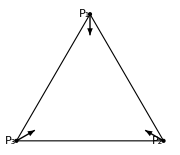

```mathematica
(* show bisectors computed from vertices for equilateral *)
showBisectors[Table[{Sin[a],Cos[a]},{a,0,2π-π/3,2π/3}]]
```

#### Nagel Point

```mathematica
getExtouchPoints[orbit_,exc_]:=MapThread[closestPerp[#1,#2,#3]&,{exc,orbit,RotateLeft[orbit]}];
```

```mathematica
Clear@getExcircleData;
getExcircleData[orbit_,exc_(*12,23,31*),npc_]:=Module[{excFeet,altLengths,tps,radii,feus,nagel,medians,mitten,mittenPedals,
mittenFeet,sides,cosABC,cosSum,cosProd,sideProd,altLengthsProd},
(* side touch points to sides: 12,23,31 *)
tps=getExtouchPoints[orbit,exc];
excFeet=getAltBases@@exc;
altLengths=MapThread[magn[#1-#2]&,{exc,excFeet}];
radii=MapThread[magn[#1-#2]&,{exc,tps}];
feus=MapThread[ray[#1,norm[npc-#1],#2]&,{exc,radii}];
(*nagel=interRays[orbit[[1]],tps[[2]]-orbit[[1]],orbit[[2]],tps[[3]]-orbit[[2]]];*)
(* MapThread[Line[{#1,ray[#1,norm[#2-#1],10]}]&,{exc,RotateRight@medians}]}],{}],*)
medians=getMedians@@orbit;
mitten=interRays[exc[[1]],medians[[3]]-exc[[1]],exc[[2]],medians[[1]]-exc[[2]]];
mittenPedals=MapThread[closestPerp[mitten,#1,#2]&,{orbit,RotateLeft@orbit}];
mittenFeet=MapThread[interRays[#1,#2-#1,#3,#4-#3]&,{exc,RotateRight@medians,RotateLeft@exc,RotateRight@exc}];
sides=RotateLeft[triLengths@exc];
cosABC=getTriCosines[exc];
cosSum=Total[cosABC];
cosProd=cosABC[[1]]*cosABC[[2]]*cosABC[[3]];
sideProd=sides[[1]]*sides[[2]]*sides[[3]];
altLengthsProd=altLengths[[1]]*altLengths[[2]]*altLengths[[3]];
{
"sides"->sides,
"perimeter"->Total[sides],
"cosABC"->cosABC,
"excFeet"->excFeet,
"altLengths"->altLengths,
"sumAltLengths"->Total@altLengths,
"prodAltLengths"->altLengthsProd,
"sumInvAltLengths"->Total[(1/#)&/@altLengths],
"cosSum"->cosSum,
"cosProd"->cosProd,
"sideProd"->sideProd,
"tps"->tps,(* extouchpoints*)
"radii"->radii,
"sumRadiiSqr"->Total[#^2&/@radii],
"sumInvRadiiSqr"->Total[(1/#^2)&/@radii],
"sumRadii"->Total@radii,
"sumInvRadii"->Total[(1/#)&/@radii],
"feus"->feus,
"mitten"->mitten,
"mittenPedals"->mittenPedals,
"mittenFeet"-> mittenFeet (* BAD choice: intersecao do segm Vi-MITTEN com o lado oposto do extriangulo *)
}
];
```

## Drawing Notables & Clrs

```mathematica
ptClrs={
"ell"->Black,
"med"->Black,
"bar"->Purple,
"inc"->Darker@Green,
"ort"->Orange,
"cir"->Lighter@Purple,
"npc"->RGBColor[1.,0.02,0.3],
"exc"->Darker@Green,
"ex12"->Darker@Green,
"ex23"->Darker@Green,
"ex31"->Darker@Green,
"feu"-> RGBColor[0.5,0.5,0.27],
"antifeu"->Orange,
"anticompl"->Blue,
"x88"->Cyan,
"nag"->Red,
"mit"->Red(*Lighter@Blue*),
"sym"->Red,
"ger"->Pink,
"spi"->Darker@Cyan,
"nap"->Red,
"hex"->Pink,
(* overrides *)
"red"->Red,
"green"->Green,
"blue"->Blue
};
```

```mathematica
Clear@plotEll;
plotEll[a_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
plotEllFill[a_,clrFill_,clr_:("ell"/.ptClrs)]:=Module[{int,ext},
int=ParametricPlot[r{N[a] Cos[u],Sin[u]},{u,0.0,2.0π},{r,0,1},
PlotStyle->clrFill,PerformanceGoal->"Quality"];
ext=plotEll[a,clr];
Show[{int,ext}]];
plotEllb[a_,b_,clr_:("ell"/.ptClrs)]:=ParametricPlot[{N[a] Cos[u],N[b]Sin[u]},{u,0.0,2.0π},
PlotStyle->clr,PerformanceGoal->"Quality"];
```

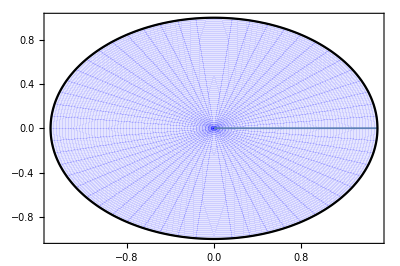

```mathematica
plotEllFill[1.5,Directive[Opacity@.1,Blue],Black]
```

```mathematica
drawArrow[p0_,phat_,l_]:=Arrow[{p0,ray[p0,phat,l]}];
```

```mathematica
Clear@txtSubscript;
txtSubscript[txt_,subscr_,size_,where_]:=Text[Style[Subscript[txt,subscr],size],where];
```

```mathematica
Clear@drawOrbit;
drawOrbit[orbitData_,lgt_:.25,drawNormals_:True,psize_:12]:=Module[{normals,orbit,halfAlpha},
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
halfAlpha="halfAlpha"/.orbitData;
Graphics[{
PointSize[Large],Arrowheads[Medium],
{Black,Point@orbit},
{FaceForm[GrayLevel[.95]],EdgeForm[{Thick,Black}],Polygon@orbit},
If[drawNormals,
{Black,
MapThread[drawArrow[#1,#2,lgt]&,{orbit,normals}],
Dashed,
drawArrow[orbit[[1]],"nRot"/.orbitData,lgt],
drawArrow[orbit[[1]],"nRotNeg"/.orbitData,lgt],
Text["α",ray[orbit[[1]],halfAlpha ,lgt*.5]]},{}],
MapThread[txtSubscript["P",ToString@#1,psize,ray[#2,-#3,lgt*.5]]&,
{{1,2,3},orbit,normals}]}]
];
```

```mathematica
Clear@drawOneNotable;drawOneNotable[clr_,at_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Point@at,Text[Style[txt,fntSize],at,{dx,dy}]};
circOneNotable[clr_,at_,rad_,txt_,dx_:1.5,dy_:0,fntSize_:12]:={clr,Circle[at,rad],Text[Style[txt,fntSize],at,{dx,dy}]};
Clear@drawNotableLines;drawNotableLines[notables_]:=Graphics@{Darker[Gray],Dashed,
(* euler line: cir,bar,npc,ort *)
Line[{"cir","ort"}/.notables],
(* npc to feuerbach: npc,inc,feu *)
Line[{"npc","feu"}/.notables],
(* mittenpunkt to symmedian: mit,inc,sym *)
Line[{"mit","sym"}/.notables],
(* gergonne to mit: ger,bar,mit *)
Line[{"mit","ger"}/.notables],
(* nagel line: nag,bar,spi,inc *)
Line[{"nag","inc"}/.notables]};
Clear@drawNotables;
drawNotables[notables_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
drawNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotables;
circNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@circNotablesSingleClr;
circNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"}}];
Clear@drawSomeNotables;
drawSomeNotables[notables_,nots_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[(#/.ptClrs),(#/.notables),prefix<>#]&/@nots}];
Clear@drawBasicNotables;
drawBasicNotables[notables_,prefix_:""]:=drawSomeNotables[notables,{"inc","bar","ort","cir","npc","mit","feu"},prefix];
Clear@drawBasicNotablesSingleClr;
drawBasicNotablesSingleClr[notables_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
drawOneNotable[clr,(#/.notables),prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotables;
circBasicNotables[notables_,rad_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[(#/.ptClrs),(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
Clear@circBasicNotablesSingleClr;
circBasicNotablesSingleClr[notables_,rad_,clr_,prefix_:""]:=Graphics[{PointSize[Large],
circOneNotable[clr,(#/.notables),rad,prefix<>#]&/@
{"inc","bar","ort","cir","npc","mit","feu"}}];
```

Formatting

```mathematica
nfn[v_,n_]:=ToString@NumberForm[v,{n+2,n}];
nf[v_]:=ToString@NumberForm[v,{3,2}];
nf1[v_]:=ToString@NumberForm[v,{3,1}];
nf0[v_]:=ToString@IntegerPart[v];
```

## Draw Orbits: Parametrize by x_1

```mathematica
Clear@drawSim;
drawSim[a_,x_,drLines_,opts:OptionsPattern[]]:=Module[{ellPlot,orbitData,orbit,normals,notables,lgt=.25},
ellPlot=plotEll[a];
orbitData=getOrbitData[N[a],N[x], FilterRules[{opts}, Options[getOrbitData]]];(* N for speed *)
(* half-angle to display α at bisector *)
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
notables=getNotables[orbit,normals];
Show[{
ellPlot,
drawOrbit[orbitData,lgt],
drawNotables[notables],
If[drLines,drawNotableLines[notables],{}]
},
ImageSize->Large,
AspectRatio->Automatic,
PlotRange->{{-2,2},{-1.1,1.1}},Frame->True,AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style["a="<>nf@a<>"; x="<>nf@x,20]]];
```

```mathematica
Module[{a=1.35},
Manipulate[drawSim[a,x,drLines,posY->thePosY],
{{x,.1},-a,a,.01},
{{thePosY,False},{False,True}},
{{drLines,False,"lines"},{False,True}},
SaveDefinitions->True]]
```

## Trilinears: X(1)~X(100)

```mathematica
Clear@getNewCenters;
getNewCenters[orbit_,{a_,b_,c_},singles_:{}]:=Module[{eqns,
cosA,cosB,cosC,sinA,sinB,sinC,
secA,secB,secC,cscA,cscB,cscC,
tanA,tanB,tanC,cotA,cotB,cotC,
cos2A,cos2B,cos2C,sin2A,sin2B,sin2C,
sec2A,sec2B,sec2C,csc2A,csc2B,csc2C,
cos3A,sin3A,cos3B,sin3B,cos3C,sin3C,
sec3A,sec3B,sec3C,csc3A,csc3B,csc3C,
cPi3=Cos[π/3.],sPi3=Sin[π/3.],cPi6=Cos[π/6.],sPi6=Sin[π/6.],
sinApPi3,sinBpPi3,sinCpPi3,sinAmPi3,sinBmPi3,sinCmPi3,
sinApPi6,sinBpPi6,sinCpPi6,sinAmPi6,sinBmPi6,sinCmPi6,
cscApPi3,cscBpPi3,cscCpPi3,cscAmPi3,cscBmPi3,cscCmPi3,
cscApPi6,cscBpPi6,cscCpPi6,cscAmPi6,cscBmPi6,cscCmPi6},
{cosA,cosB,cosC}={lawOfCosines[a,b,c],lawOfCosines[b,a,c],lawOfCosines[c,a,b]};
{sinA,sinB,sinC}=getSin/@{cosA,cosB,cosC};
{secA,secB,secC}=1./{cosA,cosB,cosC};
{cscA,cscB,cscC}=1./{sinA,sinB,sinC};
{tanA,tanB,tanC}={sinA,sinB,sinC}/{cosA,cosB,cosC};
{cotA,cotB,cotC}=1./{tanA,tanB,tanC};
{cos2A,cos2B,cos2C}=cosDoubleAngle/@{cosA,cosB,cosC};
{sec2A,sec2B,sec2C}=1./{cos2A,cos2B,cos2C};
{sin2A,sin2B,sin2C}=getSin/@{cos2A,cos2B,cos2C};
{csc2A,csc2B,csc2C}=1./{sin2A,sin2B,sin2C};
{sin3A,cos3A}=sinCosTripleAngle[sinA,cosA,sin2A,cos2A];
{sin3B,cos3B}=sinCosTripleAngle[sinB,cosB,sin2B,cos2B];
{sin3C,cos3C}=sinCosTripleAngle[sinC,cosC,sin2C,cos2C];
{sec3A,sec3B,sec3C}=1./{cos3A,cos3B,cos3C};
{csc3A,csc3B,csc3C}=1./{sin3A,sin3B,sin3C};
{sinApPi3,sinAmPi3}=getSinApmB[sinA,sPi3,cosA,cPi3];
{sinBpPi3,sinBmPi3}=getSinApmB[sinB,sPi3,cosB,cPi3];
{sinCpPi3,sinCmPi3}=getSinApmB[sinC,sPi3,cosC,cPi3];
{sinApPi6,sinAmPi6}=getSinApmB[sinA,sPi6,cosA,cPi6];
{sinBpPi6,sinBmPi6}=getSinApmB[sinB,sPi6,cosB,cPi6];
{sinCpPi6,sinCmPi6}=getSinApmB[sinC,sPi6,cosC,cPi6];
{cscApPi3,cscBpPi3,cscCpPi3}=1./{sinApPi3,sinBpPi3,sinCpPi3};
{cscAmPi3,cscBmPi3,cscCmPi3}=1./{sinAmPi3,sinBmPi3,sinCmPi3};
{cscApPi6,cscBpPi6,cscCpPi6}=1./{sinApPi6,sinBpPi6,sinCpPi6};
{cscAmPi6,cscBmPi6,cscCmPi6}=1./{sinAmPi6,sinBmPi6,sinCmPi6};
eqns=Get["data/x0001_0100.m"];
Chop[{
#[[1]],#[[3]],
trilinearToCartesian[orbit,{a,b,c},N@ReleaseHold[#[[2]]]]}&/@
(* if singles ≠ {}, use the list to only evaluate requested indices *)
If[Length[singles]>0,eqns[[singles]],eqns]]
];
```

```mathematica
List@@@Take[((Second@#)&/@Get["data/x0001_0100.m"]),3]
```

{{{1,1,1}},{{b c,a c,a b}},{{cosA,cosB,cosC}}}

```mathematica
centerEqns=TraditionalForm@First@First@#&/@List@@@((Second@#)&/@Get["data/x0001_0100.m"]);
centerNames=(#[[1]]<>": "<>#[[2]])&/@Quiet@getNewCenters[{{0,0},{1,0},{1,1}},RotateLeft@{1,1,Sqrt[2.]}];
```

```mathematica
Clear@newCenters;newCenters[a_,t_,singles_:{}]:=Module[{orbit,normals,sides},
{orbit,normals}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=RotateLeft[triLengths[orbit]];
getNewCenters[orbit,sides,singles]
];
```

```mathematica
Clear@newCentersAnticompl;
newCentersAnticompl[a_,t_,singles_:{}]:=Module[{orbit,normals,sides,act,sidesAct},
{orbit,normals}=orbitNormals[a,t];
orbit=Reverse@orbit;
sides=RotateLeft@triLengths[orbit];
act=anticomplementaryTriangle[orbit,sides];
sidesAct=RotateLeft@triLengths[act];
getNewCenters[act,sidesAct,singles]
];
```

```mathematica
Clear@newCentersExc;newCentersExc[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
sides=RotateLeft@triLengths[exc];
getNewCenters[exc,sides,singles]
];
```

```mathematica
Clear@newCentersOrthic;newCentersOrthic[a_,t_,singles_:{}]:=Module[{orbit,normals,feet,sides},
{orbit,normals}=orbitNormals[a,t];
feet=getAltBases@@orbit;
sides=RotateLeft@triLengths[feet]; (* rotate left? *)
getNewCenters[feet,sides,singles]
];
```

```mathematica
Clear@newCentersMedial;newCentersMedial[a_,t_,singles_:{}]:=Module[{orbit,normals,meds,sides},
{orbit,normals}=orbitNormals[a,t];
meds=getMedians@@orbit;
sides=RotateLeft@triLengths[meds]; (* rotate left? *)
getNewCenters[meds,sides,singles]
];
```

```mathematica
Clear@newCentersIntouch;newCentersIntouch[a_,t_,singles_:{}]:=Module[{orbit,normals,tps,sides},
{orbit,normals}=orbitNormals[a,t];
tps=getTouchPts[orbit,normals];
sides=RotateLeft@triLengths[tps]; (* rotate left? *)
getNewCenters[tps,sides,singles]
];
```

```mathematica
Clear@newCentersExtouch;newCentersExtouch[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,tps,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
tps=getExtouchPoints[orbit,exc];
sides=RotateLeft@triLengths[tps]; (* rotate left? *)
getNewCenters[tps,sides,singles]
];
```

```mathematica
Clear@newCentersExfeuer;newCentersExfeuer[a_,t_,singles_:{}]:=Module[{orbit,normals,exc,npc,excCircleData,feus,sides},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
feus=("feus"/.excCircleData);
sides=RotateLeft@triLengths[feus]; (* rotate left? *)
getNewCenters[feus,sides,singles]
];
```

## Loci Tables for X(1) ~ X(100)

```mathematica
Clear@getLociTable;
getLociTable[a_,ctrFn_,tmax_:π/1.2,step_:toRad[.1]]:=Module[{nc,pts,loci},
loci=Table[
nc=ctrFn[a,t]//Quiet;
pts=(#[[3]]&/@nc);
{t,pts},
{t,.5*step,tmax,step}];
Transpose[#[[2]]&/@loci]];
```

```mathematica
(*loci15t=getLociTable[1.5,newCenters];*)
```

```mathematica
doLociTables=False;
Module[{a=1.5,fname="data/loci15t.m"},
If[doLociTables,
loci15t=getLociTable[a,newCenters];
lociOrt15t=getLociTable[a,newCentersOrthic];
lociMed15t=getLociTable[a,newCentersMedial];
lociExc15t=getLociTable[a,newCentersExc,π/1.28];
lociIntouch15t=getLociTable[a,newCentersIntouch,π/1.2];
lociExtouch15t=getLociTable[a,newCentersExtouch,π/1.27];
lociAnticompl15t=getLociTable[a,newCentersAnticompl,π/1.28];
lociExfeuerbach15t=getLociTable[a,newCentersExfeuer];
Print@"saving..." ;
Save[fname,{loci15t,lociOrt15t,lociMed15t,lociExc15t,lociIntouch15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t}],
Print@"loading...";Get[fname]]];
```

loading...

*** GENERATES BILLIARD
X(100)  ANTICOMPLEMENT OF FEUERBACH POINT IS THE BILLIARD

*** GENERATES BILLIARD
X(88) = ISOGONAL CONJUGATE OF X(44)

X(44) = X(6)-LINE CONJUGATE OF X(1)
*** X(44) lies on these lines:
Trilinears       b + c - 2a : c + a - 2b : a + b - 2c
Barycentrics  a(b + c - 2a) : b(c + a - 2b) : c(a + b - 2c)
X(44) = (3r2 + 6rR + s2)*X(1) - 18rR*X(2) - 6r2*X(3)    (Peter Moses, April 2, 2013)

LINE-CONJUGATE: (looked up glossary)
Let P = p : q : r, U = u : v : w
The P-line conjugate of U is the point of intersection of line PU and the trilinear polar of the isogonal conjugate of U.

I.e., intersect line X(6)X(1) with the trilinear polar (TP) of the isog conjugate of X(1) which is X(1) itself.

The TP of X(1) is L1, the antiorthic axis, i.e., the orthic axis of the excentral triangle.

the orthic axis of a triangle are give by points (Oa, Ob,Oc) where each side of the orthic triangle meet the triangle sides (Oa, Ob, Oc)

-Graphics-
*** to summarize:

1) to get X(44) intersect the line connecting the incenter X(1) and the symmedian point X(6) with the orthic axis of the extriangle.
2) to get X(88) which generates the billiard, get the isogonal conjugate of X(44).

#### Order - Dependent has to change that

```mathematica
Clear@showLoci;
showLoci[locus_,a_,lociList_,
auto_,range_,imgSize_:400]:=Module[{ell,ellCaustic,ca,cb,name,lociMaxX,maxX,lociMaxY,maxY,pts,clrs,ncs,lls},
ell=plotEll[a,Black];
{ca,cb}=getTriCausticParams[a];
ellCaustic=plotEllb[ca,cb,{Dashed,Black}];
ncs=#[[locus]]&/@lociList;
clrs={
Black(* billiard *),
{Dashed,Black}(*caustic*),
Blue,(* orbit *)
Red,(* medial *)
"ort"/.ptClrs,(* orthic *)
"inc"/.ptClrs,(* intouch *)
{Dashed,Blue},(* excentral *)
{Dashed,"inc"/.ptClrs},(* extouch *)
{Dashed,Red},(* anticompl *)
"feu"/.ptClrs (* feuer *)
};
pts={PointSize@Medium,MapThread[{If[ListQ@#1,Second@#1,#1],Point@#2[[1]]}&,{Drop[clrs,2],ncs}]};
name=centerNames[[locus]];
(* NEED NOT DO THIS FOR ALL LOCI!!! *)
lociMaxX=clamp[#,10]&/@Table[Max[Select[Join[{a},Sequence@@((First/@(#[[l]]))&/@lociList)],NumberQ]],
{l,1,Length@lociList[[1]]}];
lociMaxY=clamp[#,10]&/@Table[Max[Select[Join[{1},(* b = 1 *) Sequence@@((Second/@(#[[l]]))&/@lociList)],NumberQ]],
{l,1,Length@lociList[[1]]}];
lls=MapThread[ListLinePlot[#1[[locus]],ClippingStyle->None,PlotStyle->#2]&,{lociList,Drop[clrs,2]}];
{maxX,maxY}=If[auto,
1.1{lociMaxX[[locus]],lociMaxY[[locus]]},
{range,range}];
Legended[Show[{ell,ellCaustic,Sequence@lls,Graphics@pts},
ImageSize->{imgSize,imgSize},
Axes->True,
PlotLabel->Style[name,Directive[{Black,14}]],
PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"billiard","caustic","orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]]];
```

```mathematica
lociList15t={loci15t,lociMed15t,lociOrt15t,lociIntouch15t,lociExc15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t};
```

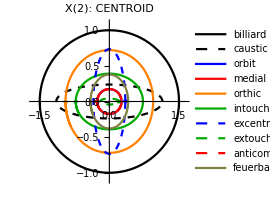

```mathematica
showLoci[2,1.5,lociList15t, True,2,200]
```

#### Feuerbach point of anticomplementary triangle sweeps the billiard just like the anticomplement of feuerbach of reference triangle.

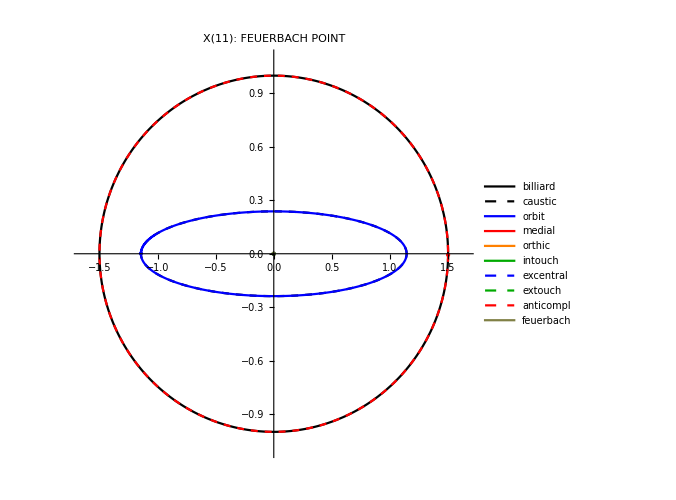

```mathematica
Module[{d=.001,loci0},
(* fake other empty loci *)
loci0=ConstantArray[{{-d,-d/2},{d,-d/2},{0,d/2}},100];
showLoci[11,1.5,{loci15t,loci0,loci0,loci0,loci0,loci0,lociAnticompl15t,loci0},
True,2,500]]
```

```mathematica
Manipulate[showLoci[locus,1.5,lociList15t,
auto,range,500],
{{locus,1},1,Length@loci15t,1,Appearance->"Open"},
{{auto,True},{True,False}},
{{range,2},{1,2,4,8,16}},SaveDefinitions->True]
```

#### Needs to show a picture of each triangle

```mathematica
(* {"billiard","caustic",
"orbit","medial","orthic","intouch","excentral","extouch","anticompl","exfeuer"} *)
```

```mathematica
showDerivedTris[a_,tDeg_]:=Module[{caustic,ell,ca,cb,ellCaustic,clrs,orbit,sides,tris,gr,maxX=2,maxY=2},
{ca,cb}=getTriCausticParams[a];
ell=plotEll[a,Black];
ellCaustic=plotEllb[ca,cb,{Dashed,Black}];
clrs={Black,{Dashed,Black},Blue,Red,"ort"/.ptClrs,"inc"/.ptClrs,{Dashed,Blue},{Dashed,"inc"/.ptClrs},{Dashed,Red},"feu"/.ptClrs};
orbit=orbitNormals[a,toRad@tDeg][[1]];
sides=RotateLeft@triLengths@orbit;
tris=(#[orbit,sides]&)/@{medialTriangle,orthicTriangle,intouchTriangle,
excentralTriangle,extouchTriangle,anticomplementaryTriangle,feuerbachTriangle};
gr=Graphics[{FaceForm@None,MapThread[{EdgeForm@{Thick,If[ListQ@#1,Sequence@@#1,#1]},Polygon@#2}&,
{Drop[clrs,2],Prepend[tris,orbit]}]}];
Legended[Show[{ell,ellCaustic,gr},
Frame->True,ImageSize->Large,PlotLabel->Style["Orbit and Derived Triangles",Directive[{Black,14}]],PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"billiard","caustic","orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]]];
```

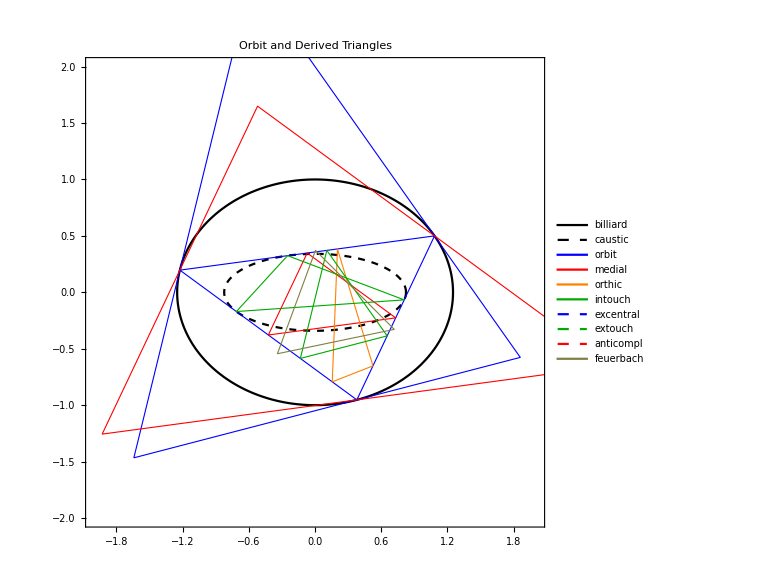

```mathematica
showDerivedTris[1.25,30]
```

```mathematica
Module[{a=1.5,caustic,ell,ca,cb,ellCaustic,clrs},
{ca,cb}=getTriCausticParams[a];
ell=plotEll[a,Black];
ellCaustic=plotEllb[ca,cb,{Dashed,Black}];
clrs={Black,{Dashed,Black},Blue,Red,"ort"/.ptClrs,"inc"/.ptClrs,{Dashed,Blue},{Dashed,"inc"/.ptClrs},{Dashed,Red},"feu"/.ptClrs};
Manipulate[Module[{orbit,sides,tris,gr,maxX=2,maxY=2},
orbit=orbitNormals[a,toRad@tDeg][[1]];
sides=RotateLeft@triLengths@orbit;
tris=(#[orbit,sides]&)/@{medialTriangle,orthicTriangle,intouchTriangle,
excentralTriangle,extouchTriangle,anticomplementaryTriangle,feuerbachTriangle};
gr=Graphics[{FaceForm@None,MapThread[{EdgeForm@{Thick,If[ListQ@#1,Sequence@@#1,#1]},Polygon@#2}&,
{Drop[clrs,2],Prepend[tris,orbit]}]}];
Legended[Show[{ell,ellCaustic,gr},
Frame->True,ImageSize->Large,PlotLabel->Style["Orbit and Derived Triangles",Directive[{Black,14}]],PlotRange->{{-maxX,maxX},{-maxY,maxY}}],
LineLegend[Directive[{Thickness@Large,#}]&/@clrs,
{"billiard","caustic","orbit",
"medial","orthic","intouch","excentral","extouch","anticompl","feuerbach"}]]],
{{tDeg,31},-180,180,1}]]
```

## Save Loci Frames to File

```mathematica
createLociFrames=False;
If[createLociFrames,showLociFrames=Table[Print@locus;showLoci[locus,1.5,lociList15t,
True,2,500],{locus,1,Length@loci15t,1}]; 
Length@showLociFrames];
```

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica

```mathematica
Clear@padZ;padZ[v_,n_:4]:=ToString@NumberForm[v,{n,0},NumberPadding->{"0",""},NumberPoint->""];
getLocusFname[i_]:="loci/locus_"<>padZ[i]<>".png";
```

```mathematica
createLociFrames=False;If[createLociFrames,
If[!DirectoryQ["loci"],CreateDirectory["loci"]];
MapIndexed[Export[getLocusFname[First[#2]],#1]&,showLociFrames]];
```

## Predict which loci are elliptic w/ least squares

```mathematica
Clear@findEllParams;
findEllParams[a_,i_,locus_,name_]:=Module[{m,b,c,lsc,causticC,ls,lsa,lsb,err,causticA,causticB,abRatio,causticRatio,lsRatio},
m=(#^2)&/@locus;(* { {x1^2,y1^2}, {x2^2,y2^2}, ... } *)
b=ConstantArray[1,Length@locus];
ls=LeastSquares[m,b];
{lsa,lsb}=Sqrt[1/#]&/@ls;
c=Sqrt@Abs[a^2-1];
lsc=Sqrt@Abs[lsa^2-lsb^2];
err=Norm[m.ls-b];
{causticA,causticB}=getTriCausticParams[a];
causticC=Sqrt@Abs[causticA^2-causticB^2];
lsRatio=lsa/lsb;
abRatio=a;
causticRatio=causticA/causticB;
<|"i"->i,
"name"->name,
"errNegl"->(Abs[err]<10^-6),
"ellSim"->negl[abRatio-lsRatio],
"ellSimInv"->negl[abRatio-1/lsRatio],
"ellEq"->(negl[a-lsa]&&negl[1-lsb]),
"ellEqInv"->(negl[1-lsa]&&negl[a-lsb]),
"causticSim"->negl[causticRatio-lsRatio],
"causticSimInv"->negl[causticRatio-1/lsRatio],
"causticEq"->(negl[causticA-lsa]&&negl[causticB-lsb]),
"causticEqInv"->(negl[causticB-lsa]&&negl[causticA-lsb]),
"confocal"->negl[c-lsc],
"err"->err,
"a"->a,"b"->1,"a/b"->abRatio,"b/a"->(1/abRatio),
"c"->c,"lsc2"->lsc,
"lsA"->lsa,"lsB"->lsb,"lsA/lsB"->lsRatio,"lsB/lsA"->(1/lsRatio),
"caustic_a"->causticA,"caustic_b"->causticB,"caustic_a/b"->causticRatio,"caustic_b/a"->(1/causticRatio),
"caustic_c"->causticC
|>];
```

```mathematica
ellParams=Quiet@Table[findEllParams[1.5,i,loci15t[[i]],centerNames[[i]]],{i,Length@loci15t}]//Sort[#,#1["err"]<#2["err"]&]&;
```

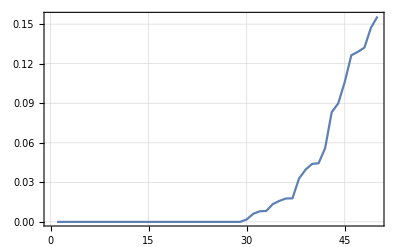

```mathematica
ListLinePlot[#["err"]&/@Take[ellParams,50],Frame->True,GridLines->Automatic]
```

```mathematica
ellParams[[1]][[Keys[ellParams[[1]]]]]
```

<|i→100,name→X(100): ANTICOMPLEMENT OF FEUERBACH POINT,errNegl→True,ellSim→True,ellSimInv→False,ellEq→True,ellEqInv→False,causticSim→False,causticSimInv→False,causticEq→False,causticEqInv→False,confocal→True,err→5.89234×10^-14,a→1.5,b→1,a/b→1.5,b/a→0.666667,c→1.11803,lsc2→1.11803,lsA→1.5,lsB→1.,lsA/lsB→1.5,lsB/lsA→0.666667,caustic_a→1.14307,caustic_b→0.23795,caustic_a/b→4.80384,caustic_b/a→0.208167,caustic_c→1.11803|>

```mathematica
ellParamsSorted=Sort[Select[ellParams,(#["errNegl"])&],#1["i"]<#2["i"]&];
```

#### Which are ellipses?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,ellParamsSorted]//TableForm
```

1 | X(1): INCENTER
2 | X(2): CENTROID
3 | X(3): CIRCUMCENTER
4 | X(4): ORTHOCENTER
5 | X(5): NINE-POINT CENTER
6 | X(7): GERGONNE POINT
7 | X(8): NAGEL POINT
8 | X(10): SPIEKER CENTER
9 | X(11): FEUERBACH POINT
10 | X(12): {X(1),X(5)}-HARMONIC CONJUGATE OF X(11)
11 | X(20): DE LONGCHAMPS POINT
12 | X(21): SCHIFFLER POINT
13 | X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
14 | X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER
15 | X(40): BEVAN POINT
16 | X(46): X(4)-CEVA CONJUGATE OF X(1)
17 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
18 | X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
19 | X(57): ISOGONAL CONJUGATE OF X(9)
20 | X(63): ISOGONAL CONJUGATE OF X(19)
21 | X(65): ORTHOCENTER OF THE INTOUCH TRIANGLE
22 | X(72): ISOGONAL CONJUGATE OF X(28)
23 | X(78): ISOGONAL CONJUGATE OF X(34)
24 | X(79): ISOGONAL CONJUGATE OF X(35)
25 | X(80): REFLECTION OF INCENTER IN FEUERBACH POINT
26 | X(84): ISOGONAL CONJUGATE OF X(40)
27 | X(88): ISOGONAL CONJUGATE OF X(44)
28 | X(90): X(3)-CROSS CONJUGATE OF X(1)
29 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### What are their trilinears

```mathematica
Module[{ell,notEll,both},
notEll=Sort[Select[ellParams,(!#["errNegl"])&],#1["i"]<#2["i"]&];
ell=Sort[Select[ellParams,(#["errNegl"])&],#1["i"]<#2["i"]&];
both=Join[ell,notEll];
Grid[Append[#,centerEqns[[#[[1]]]]]&/@MapIndexed[{First@#2,#1["name"]}&,both],ItemStyle->{Automatic,Join[ConstantArray[Blue,Length@ell],ConstantArray[Red,Length@notEll]]}, Alignment->Left]]
```

1 | X(1): INCENTER | 1
2 | X(2): CENTROID | b c
3 | X(3): CIRCUMCENTER | cosA
4 | X(4): ORTHOCENTER | secA
5 | X(5): NINE-POINT CENTER | cosB cosC+sinB sinC
6 | X(7): GERGONNE POINT | a
7 | X(8): NAGEL POINT | (b c)/(-a+b+c)
8 | X(10): SPIEKER CENTER | (-a+b+c)/a
9 | X(11): FEUERBACH POINT | -a+b+c
10 | X(12): {X(1),X(5)}-HARMONIC CONJUGATE OF X(11) | b c (b+c)
11 | X(20): DE LONGCHAMPS POINT | -cosB cosC-sinB sinC+1
12 | X(21): SCHIFFLER POINT | cosB cosC+sinB sinC+1
13 | X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36) | cscApPi3
14 | X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER | cscAmPi3
15 | X(40): BEVAN POINT | sinApPi3
16 | X(46): X(4)-CEVA CONJUGATE OF X(1) | sinAmPi3
17 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) | cscApPi6
18 | X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) | cscAmPi6
19 | X(57): ISOGONAL CONJUGATE OF X(9) | 1/(-a^2+b^2+c^2)
20 | X(63): ISOGONAL CONJUGATE OF X(19) | cosA-cosB cosC
21 | X(65): ORTHOCENTER OF THE INTOUCH TRIANGLE | (-a+b+c)/(b+c)
22 | X(72): ISOGONAL CONJUGATE OF X(28) | a (-a^4+b^4+c^4)
23 | X(78): ISOGONAL CONJUGATE OF X(34) | a (-a^4+b^4-b^2 c^2+c^4)
24 | X(79): ISOGONAL CONJUGATE OF X(35) | cos2A secA
25 | X(80): REFLECTION OF INCENTER IN FEUERBACH POINT | a/(-a^2+b^2+c^2)
26 | X(84): ISOGONAL CONJUGATE OF X(40) | a (a^2 (-cos2A)+b^2 cos2B+c^2 cos2C)
27 | X(88): ISOGONAL CONJUGATE OF X(44) | secA/(b+c)
28 | X(90): X(3)-CROSS CONJUGATE OF X(1) | tanA/(b+c)
29 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT | secA/(cosB+cosC)
30 | X(6): SYMMEDIAN / LEMOINE / GREBE POINT | cosA-2 cosB cosC
31 | X(9): MITTENPUNKT | a^2
32 | X(13): 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT) | a^3
33 | X(14): 2nd ISOGONIC CENTER | secA+1
34 | X(15): 1st ISODYNAMIC POINT | 1-secA
35 | X(16): 2nd ISODYNAMIC POINT | 2 cosA+1
36 | X(17): 1st NAPOLEON POINT | 1-2 cosA
37 | X(18): 2nd NAPOLEON POINT | b+c
38 | X(19): CLAWSON POINT | b^2+c^2
39 | X(22): EXETER POINT | a (b^2+c^2)
40 | X(23): FAR-OUT POINT | -cosA+cosB+cosC-1
41 | X(24): PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE | a^2 (-a+b+c)
42 | X(25): HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES | a (b+c)
43 | X(26): CIRCUMCENTER OF THE TANGENTIAL TRIANGLE | a b+a c-b c
44 | X(27): CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER | -2 a+b+c
45 | X(28): CEVAPOINT OF X(19) AND X(25) | -a+2 b+2 c
46 | X(29): CEVAPOINT OF INCENTER AND ORTHOCENTER | -cosA+cosB+cosC
47 | X(31): 2nd POWER POINT | cos2A
48 | X(32): 3rd POWER POINT | tanB+tanC
49 | X(33): PERSPECTOR OF THE ORTHIC AND INTANGENTS TRIANGLES | cos3A
50 | X(34): X(4)-BETH CONJUGATE OF X(4) | sin3A
51 | X(37): CROSSPOINT OF INCENTER AND CENTROID | a^2 (cosB cosC+sinB sinC)
52 | X(38): CROSSPOINT OF X(1) AND X(75) | cos2A (cosB cosC+sinB sinC)
53 | X(39): BROCARD MIDPOINT | tanA (cosB cosC+sinB sinC)
54 | X(41): X(6)-CEVA CONJUGATE OF X(31) | 1/(cosB cosC+sinB sinC)
55 | X(42): CROSSPOINT OF INCENTER AND SYMMEDIAN POINT | a (-a+b+c)
56 | X(43): X(6)-CEVA CONJUGATE OF X(1) | a/(-a+b+c)
57 | X(44): X(6)-LINE CONJUGATE OF X(1) | 1/(-a+b+c)
58 | X(45): X(9)-BETH CONJUGATE OF X(1) | a/(b+c)
59 | X(47): X(110)-BETH CONJUGATE OF X(34) | 1/(-cosB cosC-sinB sinC+1)
60 | X(48): CROSSPOINT OF X(1) AND X(63) | 1/(cosB cosC+sinB sinC+1)
61 | X(49): CENTER OF SINE-TRIPLE-ANGLE CIRCLE | cosA sPi6+cPi6 sinA
62 | X(50): X(74)-CEVA CONJUGATE OF X(184) | cPi6 sinA-cosA sPi6
63 | X(51): CENTROID OF ORTHIC TRIANGLE | cotA
64 | X(52): ORTHOCENTER OF ORTHIC TRIANGLE | 1/(cosA-cosB cosC)
65 | X(53): SYMMEDIAN POINT OF ORTHIC TRIANGLE | cosB+cosC
66 | X(54): KOSNITA POINT | (b c)/(-a^4+b^4+c^4)
67 | X(58): ISOGONAL CONJUGATE OF X(10) | (b c)/(-a^4+b^4-b^2 c^2+c^4)
68 | X(59): ISOGONAL CONJUGATE OF X(11) | cosA sec2A
69 | X(60): ISOGONAL CONJUGATE OF X(12) | cosA/a^2
70 | X(61): ISOGONAL CONJUGATE OF X(17) | (b c)/(a^2 (-cos2A)+b^2 cos2B+c^2 cos2C)
71 | X(62): ISOGONAL CONJUGATE OF X(18) | cosA (b+c)
72 | X(64): ISOGONAL CONJUGATE OF X(20) | cotA (b+c)
73 | X(66): ISOGONAL CONJUGATE OF X(22) | secB+secC
74 | X(67): ISOGONAL CONJUGATE OF X(23) | 1/(cosA-2 cosB cosC)
75 | X(68): PRASOLOV POINT | 1/a^2
76 | X(69): SYMMEDIAN POINT OF THE ANTICOMPLEMENTARY TRIANGLE | 1/a^3
77 | X(70): ISOGONAL CONJUGATE OF X(26) | 1/(secA+1)
78 | X(71): ISOGONAL CONJUGATE OF X(27) | 1/(1-secA)
79 | X(73): CROSSPOINT OF INCENTER AND CIRCUMCENTER | 1/(2 cosA+1)
80 | X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT | 1/(1-2 cosA)
81 | X(75): ISOTOMIC CONJUGATE OF INCENTER | 1/(b+c)
82 | X(76): 3rd BROCARD POINT | 1/(b^2+c^2)
83 | X(77): ISOGONAL CONJUGATE OF X(33) | (b c)/(b^2+c^2)
84 | X(81): CEVAPOINT OF INCENTER AND SYMMEDIAN POINT | 1/(-cosA+cosB+cosC-1)
85 | X(82): ISOGONAL CONJUGATE OF X(38) | (b^2 c^2)/(-a+b+c)
86 | X(83): CEVAPOINT OF CENTROID AND SYMMEDIAN POINT | (b c)/(b+c)
87 | X(85): ISOTOMIC CONJUGATE OF X(9) | 1/(a b+a c-b c)
88 | X(86): CEVAPOINT OF INCENTER AND CENTROID | 1/(-2 a+b+c)
89 | X(87): X(2)-CROSS CONJUGATE OF X(1) | 1/(-a+2 b+2 c)
90 | X(89): ISOGONAL CONJUGATE OF X(45) | 1/(-cosA+cosB+cosC)
91 | X(91): ISOGONAL CONJUGATE OF X(47) | sec2A
92 | X(92): CEVAPOINT OF INCENTER AND CLAWSON POINT | csc2A
93 | X(93): ISOGONAL CONJUGATE OF X(49) | sec3A
94 | X(94): ISOGONAL CONJUGATE OF X(50) | csc3A
95 | X(95): CEVAPOINT OF CENTROID AND CIRCUMCENTER | (b^2 c^2)/(cosB cosC+sinB sinC)
96 | X(96): ISOGONAL CONJUGATE OF X(52) | sec2A/(cosB cosC+sinB sinC)
97 | X(97): ISOGONAL CONJUGATE OF X(53) | cotA/(cosB cosC+sinB sinC)
98 | X(98): TARRY POINT | (b c)/(-a^2 b^2-a^2 c^2+b^4+c^4)
99 | X(99): STEINER POINT | (b c)/(b^2-c^2)

#### Which are similar to the billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellSim"]||#["ellSimInv"])&]]//TableForm
```

1 | X(2): CENTROID
2 | X(4): ORTHOCENTER
3 | X(7): GERGONNE POINT
4 | X(10): SPIEKER CENTER
5 | X(40): BEVAN POINT
6 | X(57): ISOGONAL CONJUGATE OF X(9)
7 | X(63): ISOGONAL CONJUGATE OF X(19)
8 | X(88): ISOGONAL CONJUGATE OF X(44)
9 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### Which are identical to the billiard?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["ellEq"]||#["ellEqInv"])&]]//TableForm
```

1 | X(88): ISOGONAL CONJUGATE OF X(44)
2 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

#### Which are similar to the caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticSim"]||#["causticSimInv"])&]]//TableForm
```

1 | X(3): CIRCUMCENTER
2 | X(11): FEUERBACH POINT
3 | X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
4 | X(84): ISOGONAL CONJUGATE OF X(40)

#### Which are identical to the caustic?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["causticEq"]||#["causticEqInv"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT

#### Which are confocal?

```mathematica
MapIndexed[{First@#2,#1["name"]}&,Select[ellParamsSorted,(#["confocal"])&]]//TableForm
```

1 | X(11): FEUERBACH POINT
2 | X(88): ISOGONAL CONJUGATE OF X(44)
3 | X(100): ANTICOMPLEMENT OF FEUERBACH POINT

```mathematica
Clear@tab2TeX;tab2TeX[ellParams_,test_]:=TeXForm@MapIndexed[{First@#2,#1["name"]}&,Select[ellParams,test]];
```

```mathematica
allTeXtables=Module[{texEll,texBilSim,texBilEq,texCauSim,texCauEq,texConf},
MapThread[{#1,tab2TeX[ellParamsSorted,#2]}&,
Transpose@{
{"00_ell",True&},
{"01_billSim",(#["ellSim"]||#["ellSimInv"])&},
{"02_billEq",(#["ellEq"]||#["ellEqInv"])&},
{"03_causSim",(#["causticSim"]||#["causticSimInv"])&},
{"04_causEq",(#["causticEq"]||#["causticEqInv"])&},
{"05_confoc",(#["confocal"])&}
}]];
```

```mathematica
Export["tex/tex_"<>#[[1]]<>".txt",#[[2]]]&/@allTeXtables
```

{tex/tex_00_ell.txt,tex/tex_01_billSim.txt,tex/tex_02_billEq.txt,tex/tex_03_causSim.txt,tex/tex_04_causEq.txt,tex/tex_05_confoc.txt}

#### Export to XLS

```mathematica
Export["ellParams.xlsx",{Keys[ellParams[[1]]],
Sequence@@(Values/@Sort[Select[ellParams,#["errNegl"]&],#1["i"]<#2["i"]&])}]
```

ellParams.xlsx

## Circularity of Some Paths

```mathematica
Clear@getCircularity;getCircularity[locus_]:=Module[{rads,ctr,mean,sd},
(* assume it's zero since points may not be evenly distributed so "mean" won't work and RegionCentroid is too slow *)
ctr={0,0};
rads=magn[#-ctr]&/@locus;
mean=Mean@rads;
sd=StandardDeviation@rads;
{
"ctr"->ctr;
"min"->Min@rads,
"max"->Max@rads,
"mean"->mean,
"sd"->sd,
"zscore"->sd/mean
}];
```

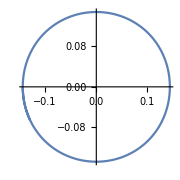

```mathematica
ListLinePlot[{lociMed15t[[37]]},AspectRatio->1,ImageSize->Small]
```

```mathematica
Clear@getMinCircularity;getMinCircularity[loci_]:=Module[{l,imin},
l=Select["zscore"/.Quiet@(getCircularity/@loci),NumberQ];
imin=First@First@Position[l,Min[l]];
{l[[imin]],centerNames[[imin]]}]
```

```mathematica
Clear@getMinCircularity2;getMinCircularity2[loci_,n_:2]:=Module[{l,best},
l=Select[Quiet@(getCircularity/@loci),(NumberQ["zscore"/.#])&];
best=Ordering[l,n,("zscore"/.#1)<("zscore"/.#2)&];
{{"zscore","mean"}/.l[[best]],best,centerNames[[best]]}]
```

### Mittenpunkt of Exfeuerbach is the champ in circularity

```mathematica
getMinCircularity2[lociExfeuerbach15t,5]
```

{{{0.00244425,0.426511},{0.00273639,0.414592},{0.00438448,0.451804},{0.00554663,0.41123},{0.00720571,0.422622}},{9,34,75,21,74},{X(9): MITTENPUNKT,X(34): X(4)-BETH CONJUGATE OF X(4),X(75): ISOTOMIC CONJUGATE OF INCENTER,X(21): SCHIFFLER POINT,X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT}}

```mathematica
Sort[MapThread[Prepend[getMinCircularity2[#1,5],#2]&,{{loci15t,lociExc15t,lociOrt15t,lociMed15t,lociIntouch15t,lociExtouch15t,lociAnticompl15t,lociExfeuerbach15t},
{"orbit","excentral","orthic","medial","intouch","extouch","anticompl","exfeuer"}}],#1[[2]]<#2[[2]]&]//TableForm
```

orbit | 0.0218696 | 1.15658
0.0270572 | 3.58902
0.0273765 | 1.12807
0.0339526 | 2.46278
0.0387964 | 1.16609 | 24
42
32
34
27 | X(24): PERSPECTOR OF ABC AND ORTHIC-OF-ORTHIC TRIANGLE
X(42): CROSSPOINT OF INCENTER AND SYMMEDIAN POINT
X(32): 3rd POWER POINT
X(34): X(4)-BETH CONJUGATE OF X(4)
X(27): CEVAPOINT OF ORTHOCENTER AND CLAWSON CENTER
excentral | 0.00712099 | 0.417493
0.0102432 | 15.4321
0.0218634 | 0.22998
0.0338591 | 0.646175
0.0375188 | 0.754846 | 54
22
39
71
46 | X(54): KOSNITA POINT
X(22): EXETER POINT
X(39): BROCARD MIDPOINT
X(71): ISOGONAL CONJUGATE OF X(27)
X(46): X(4)-CEVA CONJUGATE OF X(1)
orthic | 0.0164528 | 1.18048
0.0200192 | 1.24832
0.0205052 | 1.15185
0.0219454 | 1.15539
0.0226849 | 1.1678 | 50
25
78
56
55 | X(50): X(74)-CEVA CONJUGATE OF X(184)
X(25): HOMOTHETIC CENTER OF ORTHIC AND TANGENTIAL TRIANGLES
X(78): ISOGONAL CONJUGATE OF X(34)
X(56): EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
X(55): INSIMILICENTER(CIRCUMCIRCLE, INCIRCLE)
medial | 0.00574276 | 0.900746
0.0090297 | 0.189593
0.0106149 | 0.146182
0.0163687 | 0.334897
0.0286508 | 0.434392 | 34
36
35
44
45 | X(34): X(4)-BETH CONJUGATE OF X(4)
X(36): INVERSE-IN-CIRCUMCIRCLE OF INCENTER
X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(44): X(6)-LINE CONJUGATE OF X(1)
X(45): X(9)-BETH CONJUGATE OF X(1)
intouch | 0.0187845 | 3.45649
0.0307168 | 0.575889
0.0700364 | 0.883514
0.0709116 | 0.872128
0.0755588 | 0.540968 | 23
67
51
46
89 | X(23): FAR-OUT POINT
X(67): ISOGONAL CONJUGATE OF X(23)
X(51): CENTROID OF ORTHIC TRIANGLE
X(46): X(4)-CEVA CONJUGATE OF X(1)
X(89): ISOGONAL CONJUGATE OF X(45)
extouch | 0.0454967 | 1.12326
0.0725566 | 0.496094
0.0857645 | 1.04275
0.101938 | 0.687205
0.110837 | 0.83729 | 16
70
92
13
14 | X(16): 2nd ISODYNAMIC POINT
X(70): ISOGONAL CONJUGATE OF X(26)
X(92): CEVAPOINT OF INCENTER AND CLAWSON POINT
X(13): 1st ISOGONIC CENTER (FERMAT / TORRICELLI POINT)
X(14): 2nd ISOGONIC CENTER
anticompl | 0.00579187 | 1.37606
0.0169826 | 4.25792
0.0216879 | 0.415769
0.0291614 | 6.52586
0.030407 | 0.868307 | 70
35
21
43
78 | X(70): ISOGONAL CONJUGATE OF X(26)
X(35): {X(1),X(3)}-HARMONIC CONJUGATE OF X(36)
X(21): SCHIFFLER POINT
X(43): X(6)-CEVA CONJUGATE OF X(1)
X(78): ISOGONAL CONJUGATE OF X(34)
exfeuer | 0.00244425 | 0.426511
0.00273639 | 0.414592
0.00438448 | 0.451804
0.00554663 | 0.41123
0.00720571 | 0.422622 | 9
34
75
21
74 | X(9): MITTENPUNKT
X(34): X(4)-BETH CONJUGATE OF X(4)
X(75): ISOTOMIC CONJUGATE OF INCENTER
X(21): SCHIFFLER POINT
X(74): ISOGONAL CONJUGATE OF EULER INFINITY POINT

```mathematica
getCircularity[lociExfeuerbach15t[[9]]]
```

{min→0.425063,max→0.427964,mean→0.426511,sd→0.0010425,zscore→0.00244425}

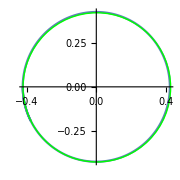

```mathematica
Show[{ListLinePlot[{lociExfeuerbach15t[[9]]},AspectRatio->1,ImageSize->Small],
Graphics[{Green,Circle[{0,0},.426511]}]},ImageSize->Small]
```

```mathematica
Clear@getDerivedTriPoint;getDerivedTriPoint[a_,t_,triFn_,pointFn_]:=Module[{o,s,tri,p},
o=orbitNormals[a,t][[1]];
s=RotateLeft@triLengths@o;
tri= triFn[o,s];
p=pointFn[tri,RotateLeft@triLengths@tri];
p];
```

```mathematica
Clear@getDerivedTriCircularity;
getDerivedTriCircularity[a_,triFn_,pointFn_,stepDeg_:1]:=Module[{locus,circ},
locus=Table[getDerivedTriPoint[a,toRad@tDeg,triFn,pointFn],{tDeg,0,359,stepDeg}];
circ=getCircularity@locus;
circ];
```

```mathematica
Clear@getFeuerbachTriMitten;
getFeuerbachTriMitten[a_,t_]:=getDerivedTriPoint[a,t,feuerbachTriangle,getMittenTrilin];
```

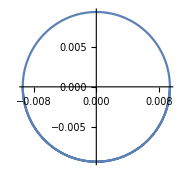

```mathematica
Quiet@ParametricPlot[getFeuerbachTriMitten[1.01,t],{t,0,π},ImageSize->Small]
```

#### There' s a minimum of the circularity error for the mittenpunkt of the feuerbach triangle

```mathematica
getDerivedTriCircularity[2,feuerbachTriangle,getMittenTrilin]
```

{min→0.753409,max→0.758943,mean→0.756866,sd→0.00204829,zscore→0.00270628}

```mathematica
(* not working ... *)
```

```mathematica
(* FindMinimum[{"zscore"/.getDerivedTriCircularity[a,feuerbachTriangle,getMittenTrilin],1.4<a<2},{a,1.4,1.5}]*)
```

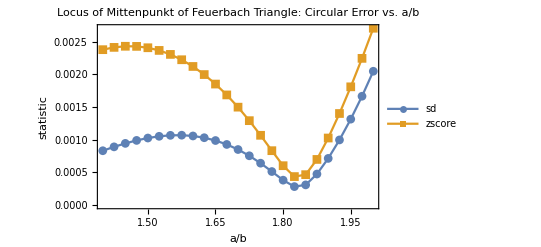

```mathematica
Module[{as,circs},
as=Range[1.4,2,.025];
circs=getDerivedTriCircularity[#,feuerbachTriangle,getMittenTrilin]&/@as;
ListLinePlot[Transpose@MapThread[{{#1,"sd"/.#2},{#1,"zscore"/.#2}(*,{#1,"mean"}/.#2*)}&,{as,circs}],PlotLegends->{"sd","zscore"(*,"mean rad"*)},PlotLabel->"Locus of Mittenpunkt of Feuerbach Triangle:\nCircular Error vs. a/b",PlotMarkers->Automatic,Frame->True,FrameLabel->{"a/b","statistic"},FrameStyle->Medium]]
```

### X(56) = EXSIMILICENTER(CIRCUMCIRCLE, INCIRCLE) = a/(b + c - a) : b/(c + a - b) : c/(a + b - c) NEARLY CIRCULAR

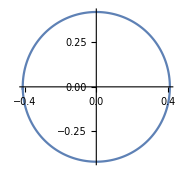

```mathematica
ListLinePlot[{lociExc15t[[56]]},AspectRatio->1,ImageSize->Small]
```

```mathematica
getCircularity[lociExc15t[[56]]]
```

{min→0.412388,max→0.420736,mean→0.417493,sd→0.00297297,zscore→0.00712099}

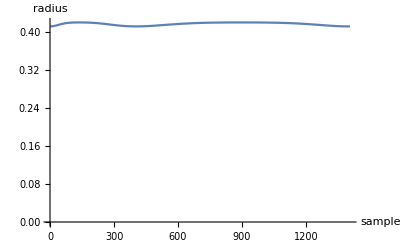

```mathematica
ListLinePlot[magn/@lociExc15t[[56]],AxesOrigin->{0,0},AxesLabel->{"sample","radius"}]
```

## Draw Loci: w/ and without lobes

```mathematica
Clear@medianLocus;
medianLocus[a_,tmax_,ps_:("med"/.ptClrs)]:=Module[{orbit,normals,meds},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
meds=getMedians@@orbit;
meds[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@incenterLocus;
incenterLocus[a_,tmax_,ps_:("inc"/.ptClrs)]:=Module[{orbit,normals},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@baricenterLocus;
baricenterLocus[a_,tmax_,ps_:("bar"/.ptClrs)]:=Module[{orbit,normals},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
(*getCentroid[orbit,triLengths@orbit]*)
getBaricenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@orthocenterLocus;
orthocenterLocus[a_,tmax_,ps_:("ort"/.ptClrs)]:=Module[{orbit,normals},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
getOrthocenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@circumcenterLocus;
circumcenterLocus[a_,tmax_,ps_:("cir"/.ptClrs)]:=Module[{orbit,normals},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
getCircumcenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@ninepointcenterLocus;
ninepointcenterLocus[a_,tmax_,ps_:("npc"/.ptClrs)]:=Module[{orbit,normals},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
getNinepointcenter@@orbit,
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@excenterLocus;
excenterLocus[a_,tmax_,ps_:("exc"/.ptClrs)]:=Module[{orbit,normals},
Quiet@ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
getExcenters[orbit,normals][[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@feuerbachcenterLocus;
feuerbachcenterLocus[a_,tmax_,ps_:("feu"/.ptClrs)]:=Module[{orbit,normals,npc,inc,inradius,feu},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
npc=getNinepointcenter@@orbit;
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
inradius=inRadius0[inc,orbit[[1]],orbit[[2]]];
getFeuerbachpoint[npc,inc,inradius],
{t,0,tmax},PlotStyle->ps]
];
```

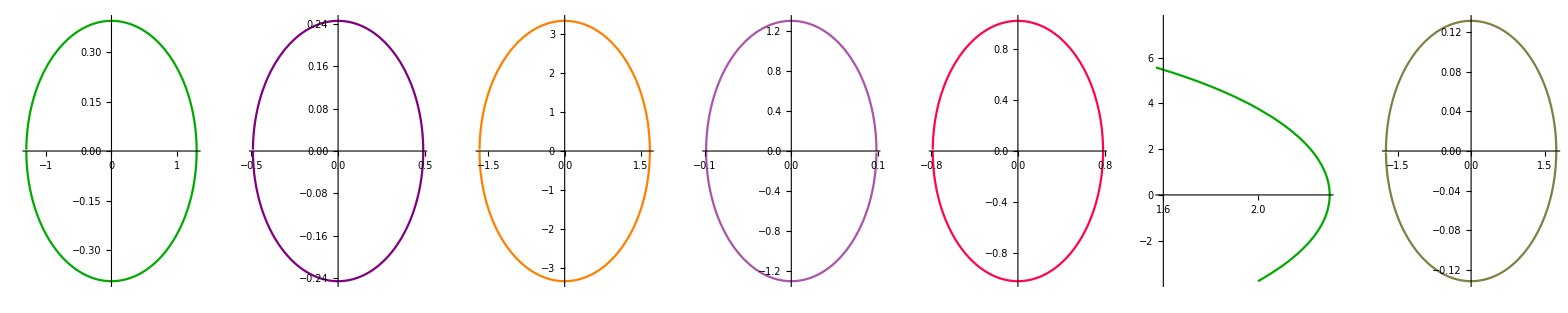

```mathematica
GraphicsRow[{
incenterLocus[2,π/1.2]//Quiet,
baricenterLocus[2,π/1.2]//Quiet,
orthocenterLocus[2,π/1.2]//Quiet,
circumcenterLocus[2,π/1.2]//Quiet,
ninepointcenterLocus[2,π/1.2]//Quiet,
excenterLocus[2,π]//Quiet,
feuerbachcenterLocus[2,π/1.2]//Quiet}
]
```

```mathematica
Clear@precompLoci;
precompLoci[a_]:=Module[{ell,tmax=π/1.2},
Show[{
incenterLocus[a,tmax]//Quiet,
baricenterLocus[a,tmax]//Quiet,
orthocenterLocus[a,tmax]//Quiet,
circumcenterLocus[a,tmax]//Quiet,
ninepointcenterLocus[a,tmax]//Quiet,
(* note excenters require full 2π *)
excenterLocus[a,2π]//Quiet,
feuerbachcenterLocus[a,tmax]//Quiet
}]];
```

```mathematica
Clear@exFeuerbachcenterLocus;
exFeuerbachcenterLocus[a_,tmax_,ps_:("feu"/.ptClrs)]:=Module[{orbit,normals,npc,exc,excCircleData},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
exc=getExcenters[orbit,normals];(*12,23,31*)
npc=getNinepointcenter@@orbit;
excCircleData=getExcircleData[orbit,exc,npc];
("feus"/.excCircleData)[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
Clear@getIntouchLocus;
getIntouchLocus[a_,tmax_,ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,tps},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
tps=getTouchPts[orbit,normals];
tps[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

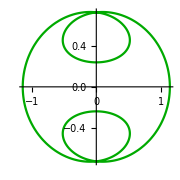

```mathematica
Show[getIntouchLocus[1.5,2π]//Quiet,ImageSize->Small]
```

```mathematica
Clear@getFeuLoci;getFeuLoci[a_,showExFeu_:False]:=Show[{
plotEll[a],
feuerbachcenterLocus[a,π/1.2]//Quiet,
If[showExFeu,exFeuerbachcenterLocus[a,2π]//Quiet,{}]}];
```

```mathematica
Clear@getDashedFeuLoci;
getDashedFeuLoci[a_]:=feuerbachcenterLocus[a,π/1.2,{Dashed,"feu"/.ptClrs}]//Quiet
```

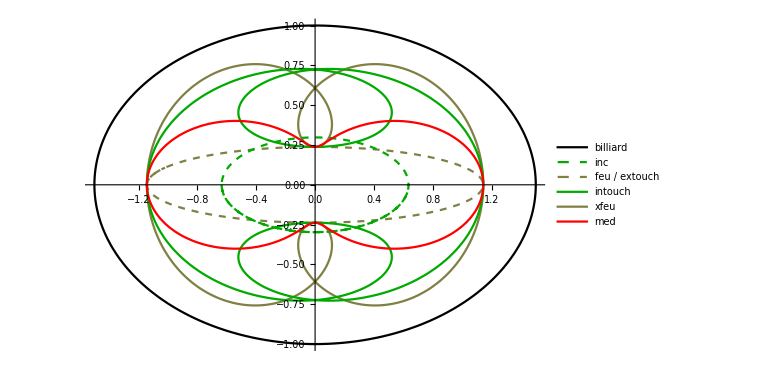

```mathematica
Module[{a=1.5,orbitData,lgt=.2},
orbitData=getOrbitData[a,toRad[30.]];
Legended[Show[{
(*drawOrbit[orbitData,lgt],*)
plotEll[a],
feuerbachcenterLocus[a,π/1.2,{Dashed,"feu"/.ptClrs}],
exFeuerbachcenterLocus[a,2π],
getIntouchLocus[a,2π],
incenterLocus[a,π,{Dashed,"exc"/.ptClrs}],
medianLocus[a,2π,Red]}, ImageSize->Large],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell","inc","feu","inc","feu","red"},
{{},Dashed,Dashed,{},{},{}}}],
{"billiard","inc","feu / extouch","intouch","xfeu","med"}]]]//Quiet
```

#### The locus of the Outer Napoleon Point is not particularly interesting

```mathematica
Clear@outerNapoleonLocus;
outerNapoleonLocus[a_,tmax_,ps_:("nap"/.ptClrs)]:=Module[{orbit,normals,sides,nap},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
sides=RotateLeft[triLengths@orbit];
nap=outerNapoleonTriangle[orbit,sides];
nap[[1]],
{t,0,tmax},PlotStyle->ps]
];
```

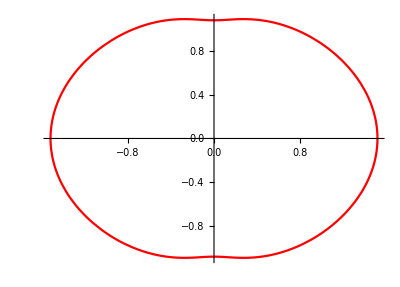

```mathematica
outerNapoleonLocus[1.5,2π]//Quiet
```

#### Path of First Morley Center Just outside Incenter' s

```mathematica
Clear@morleyIncenterLocus;
morleyIncenterLocus[a_,tmax_]:=Module[{orbit,normals,sides,mor1,mor2,mor3,inc},
ListLinePlot[Transpose@Table[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
sides=RotateLeft[triLengths@orbit];
mor1=getFirstMorleyTrilin[orbit,sides];
mor2=getSecondMorleyTrilin[orbit,sides];
mor3=getThirdMorleyTrilin[orbit,sides];
inc=getIncenterTrilin[orbit,sides];
{inc,mor1,mor2,mor3},
{t,0,tmax,tmax/100}],PlotStyle->{Darker@Green,Automatic,Automatic,Automatic},
PlotLegends->{"inc","morley 1","morley 2","morley 3"},ImageSize->Large]
];
```

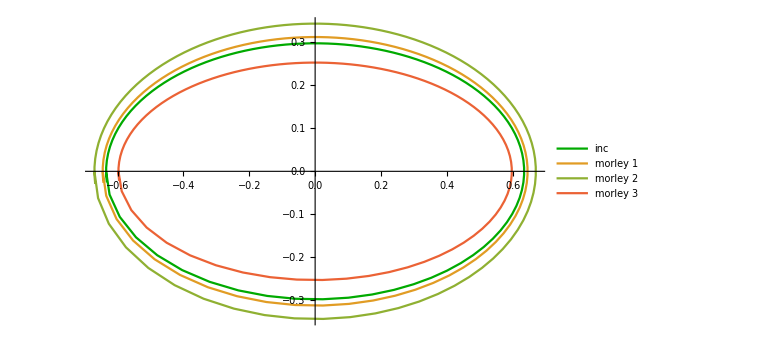

```mathematica
Quiet@morleyIncenterLocus[1.5,π/1.27]
```

```mathematica
Clear@orthicIncenterLocus;
orthicIncenterLocus[a_,tmax_,ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,feet,ortInc},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
feet=getAltBases@@orbit;
ortInc=getIncenterTrilin[feet,RotateLeft[triLengths@feet]];
ortInc,
{t,0,tmax},PlotStyle->ps]
];
```

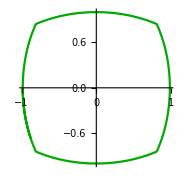

```mathematica
Show[orthicIncenterLocus[1.5,π/1.2]//Quiet,ImageSize->Small]
```

```mathematica
(* using anticomplementary triangle, but needs higher frequency *)
Clear@orthicIntouchTriangleIncenterLocus;
orthicIntouchTriangleIncenterLocus[a_,tmax_,ps_:Red]:=Module[{orbit,normals,orthic},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"intouchAnticomplOrtInc"/.orthic,
{t,0,tmax},PlotStyle->ps]
];
```

#### Shows orthic' s orthocenter (dashed) too

```mathematica
getOrthicIncOrt[a_,t_]:=Module[{orbit,normals,orthic,ort,inc},
{orbit,normals}=orbitNormals[a,t];
orthic=getOrthicData@orbit;
inc="orthicInc"/.orthic;
ort="ort"/.orthic;
{inc,ort}];
```

```mathematica
Clear@orthicsOrthicIncenterLocus2;
orthicsOrthicIncenterLocus2[a_,tmax_:π/1.2,ps_:Blue]:=
ParametricPlot[
Evaluate@List@@getOrthicIncOrt[a,t],{t,0,tmax},
PlotStyle->({ps,{Dashed,ps}}),
PlotRange->All];
```

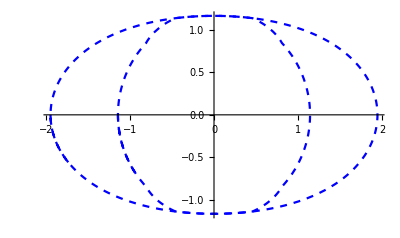

```mathematica
orthicsOrthicIncenterLocus2[1.5]//Quiet
```

```mathematica
Clear@orthicsOrthicIncenterLocus;
orthicsOrthicIncenterLocus[a_,tmaxInc_:π/1.2,tmaxOrt_:π/1.2,psOrthicOrt_:{Dashed,Blue},psOrtOrtInc_:Blue]:=Module[{orbit,normals,orthic,ppInc,ppOrt,mr=8},
ppInc=ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"orthicInc"/.orthic,
{t,0,tmaxInc},PlotStyle->Directive[Thick,psOrtOrtInc],PerformanceGoal->"Quality",MaxRecursion->mr];
ppOrt=ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"ort"/.orthic,
{t,0,tmaxOrt},PlotStyle->psOrthicOrt,PerformanceGoal->"Quality",MaxRecursion->mr];
Show[{ppOrt,ppInc},PlotRange->All]
];
```

```mathematica
Clear@orthicsOrthicAnticomplIncenterLocus;
orthicsOrthicAnticomplIncenterLocus[a_,tmax_,ps_:Pink]:=Module[{orbit,normals,orthic},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
orthic=getOrthicData@orbit;
"orthicAnticomplInc"/.orthic,
{t,0,tmax},PlotStyle->ps]
];
```

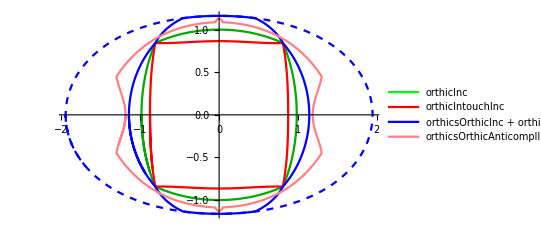

```mathematica
Legended[Show[{
orthicIncenterLocus[1.5,π/1.2],
orthicIntouchTriangleIncenterLocus[1.5,π/1.2],
orthicsOrthicIncenterLocus[1.5,π/1.2],
orthicsOrthicAnticomplIncenterLocus[1.5,π/1.2]},PlotRange->All
]//Quiet,
LineLegend[Directive[{Thickness@Large,#}]&/@{Green,Red,Blue,Pink},
{"orthicInc","orthicIntouchInc","orthicsOrthicInc + orthicOrthocenter (dashed)","orthicsOrthicAnticomplInc"}]]
```

```mathematica
Clear@getAntiComplementaryVertexLocus;getAntiComplementaryVertexLocus[a_,tmax_:2π,ps_:{Dashed,Blue}]:=Module[{orbit,normals,act},
Quiet@ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
act=anticomplementaryTriangle[orbit,RotateLeft@triLengths[orbit]];
act[[1]],
{t,0,tmax},PlotStyle->ps]];
```

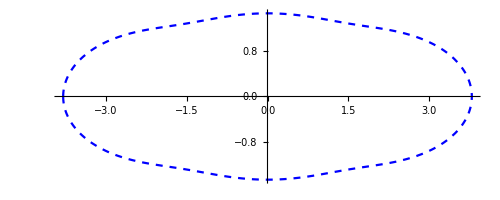

```mathematica
getAntiComplementaryVertexLocus[1.5]
```

```mathematica
Clear@getBilliardAngle;
getBilliardAngle[a_,b_,{px_,py_}]:=
ArcTan[px/a,py/b];
```

```mathematica
getBilliardAngle[1.5,1,{0,1}]
```

1.5708

```mathematica
Clear@getAngularProgress;
getAngularProgress[a_]:=Module[{ts,os,osSides,
p1ths,p2ths,p3ths,
causticA,causticB,
osFs,osFths,
etts,ettTpths1,ettTpths2,ettTpths3,
acts,actSides,
actFs,actFths,
actTps,actTpths1,actTpths2,actTpths3},
ts=Range[0,359,1];
os=First[orbitNormals[a,toRad@#]]&/@ts;
p1ths=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@os;
p2ths=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@os;
p3ths=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@os;
osSides=RotateLeft/@(triLengths/@os);
(* these move along caustic *)
{causticA,causticB}=getTriCausticParams[a];
osFs=MapThread[getFeuerbachTrilin[#1,#2]&,{os,osSides}];
osFths=toDeg[getBilliardAngle[causticA,causticB,#]]&/@osFs;
etts=MapThread[extouchTriangle[#1,#2]&,{os,osSides}];
ettTpths1=toDeg[getBilliardAngle[causticA,causticB,#[[1]]]]&/@etts;
ettTpths2=toDeg[getBilliardAngle[causticA,causticB,#[[2]]]]&/@etts;
ettTpths3=toDeg[getBilliardAngle[causticA,causticB,#[[3]]]]&/@etts;

(* these sweep billiard {a Cos[t], Sin[t]} *)
acts=MapThread[anticomplementaryTriangle[#1,#2]&,{os,osSides}];
actSides=RotateLeft/@(triLengths/@acts);
actFs=MapThread[getFeuerbachTrilin[#1,#2]&,{acts,actSides}];
actTps=MapThread[intouchTriangle[#1,#2]&,{acts,actSides}];
actFths=toDeg[getBilliardAngle[a,1,#]]&/@actFs;
actTpths1=toDeg[getBilliardAngle[a,1,#[[1]]]]&/@actTps;
actTpths2=toDeg[getBilliardAngle[a,1,#[[2]]]]&/@actTps;
actTpths3=toDeg[getBilliardAngle[a,1,#[[3]]]]&/@actTps;
{p1ths,p2ths,p3ths,
osFths,ettTpths1,ettTpths2,ettTpths3,
actFths,actTpths1,actTpths2,actTpths3}];
```

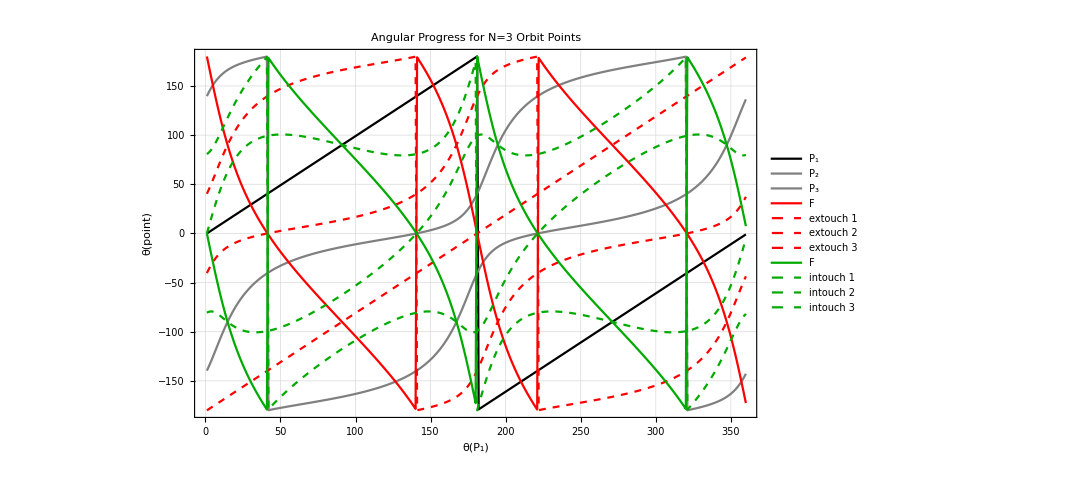

```mathematica
ListLinePlot[getAngularProgress[1.5],
PlotLegends->LineLegend[{
"P_1","P_2","P_3",
"F","extouch 1","extouch 2","extouch 3",
OverBar["F"],"intouch 1","intouch 2","intouch 3"
},LegendLayout->{"Column",1}],
PlotStyle->{
{Thick,Black},Sequence@@ConstantArray[Gray,2],
Red,Sequence@@ConstantArray[{Dashed,Red},3],
Darker@Green,Sequence@@ConstantArray[{Dashed,Darker@Green},3]},
ImageSize->800,Frame->True,GridLines->Automatic,FrameStyle->Medium,
FrameLabel->(Style[#,Large]&/@{"θ(P_1)","θ(point)"}),
PlotLabel->Style["Angular Progress for N=3 Orbit Points",{Black,Large}]]
```

## Loci w/ Convex Combinations

```mathematica
convexPts[p_,q_,t_]:=(1-t)p+t q;
```

#### Incenter with First Intouch Point

```mathematica
Clear@getConvexIntouchLocus;
getConvexIntouchLocus[a_,tmax_,s_,(* 0 = incenter, 1 = intouch *)
ps_:("inc"/.ptClrs)]:=Module[{orbit,normals,tps,inc},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
tps=getTouchPts[orbit,normals];
inc=getIncenter[orbit[[1]],normals[[1]],orbit[[2]],normals[[2]]];
convexPts[inc,tps[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convIncTps[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
incenterLocus[a,π,{"exc"/.ptClrs}],
getConvexIntouchLocus[a,2π,s,{Dashed,"inc"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"inc","inc"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"incenter","incenter-to-pedal"}]]]//Quiet
```

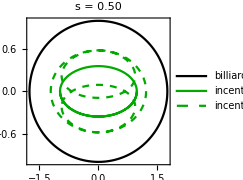

```mathematica
Show[convIncTps[1.75,.5],ImageSize->Small]
```

#### Baricenter with First Median

```mathematica
Clear@getConvexMedianLocus;
getConvexMedianLocus[a_,tmax_,s_,(* 0 = baricenter, 1 = median *)
ps_:("bar"/.ptClrs)]:=Module[{orbit,normals,meds,bar},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
meds=getMedians@@orbit;
bar=getBaricenter@@orbit;
convexPts[bar,meds[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convBariMed[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
baricenterLocus[a,π/1.2,{"bar"/.ptClrs}],
getConvexMedianLocus[a,2π,s,{Dashed,"bar"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"bar","bar"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"baricenter","baricenter-to-median"}]]]//Quiet
```

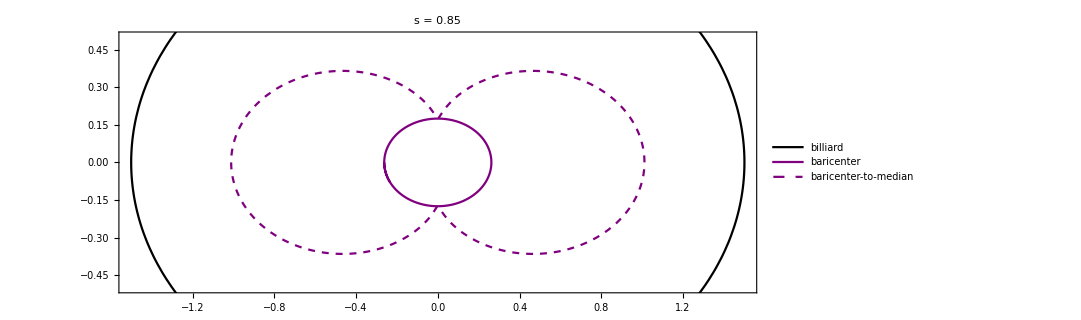

```mathematica
Show[convBariMed[1.5,0.85],ImageSize->800,PlotRange->{{-1.5,1.5},{-.5,.5}}]
```

```mathematica
Clear@combineConvexBarInc;combineConvexBarInc[a_,s_,imgSize_:800]:=Row[{convBariMed[a,s],convIncTps[a,s]}];
```

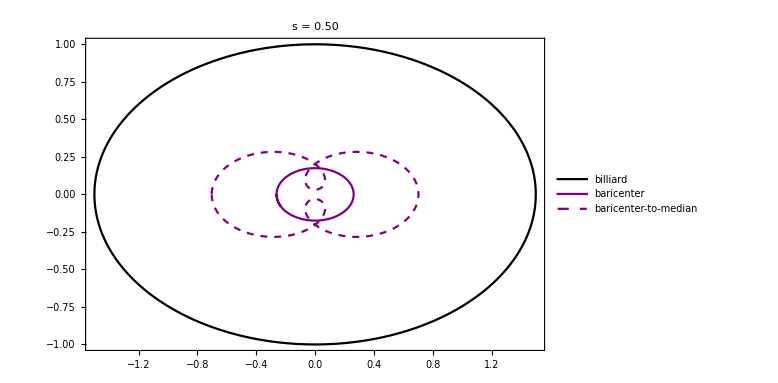
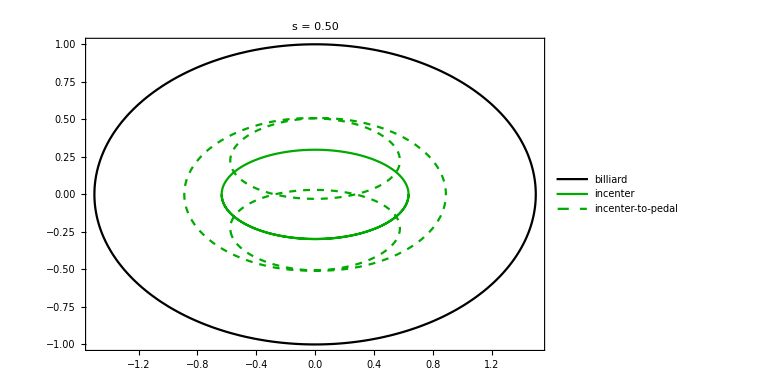

```mathematica
combineConvexBarInc[1.5,.5,800]
```

#### First Excenter with First Extouch

```mathematica
Clear@getConvexExtouchLocus;
getConvexExtouchLocus[a_,tmax_,s_,(* 0 = excenter, 1 = extouch *)
ps_:("exc"/.ptClrs)]:=Module[{orbit,normals,exc,tps},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
(*&&&*)
exc=getExcenters[orbit,normals];
tps=getExtouchPoints[orbit,exc];
convexPts[exc[[1]],tps[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convExcTps[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
excenterLocus[a,2π,{"exc"/.ptClrs}],
getConvexExtouchLocus[a,2π,s,{Dashed,"exc"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
Placed[LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"exc","exc"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"excenter","exc-to-extouch"}],Below]]]//Quiet
```

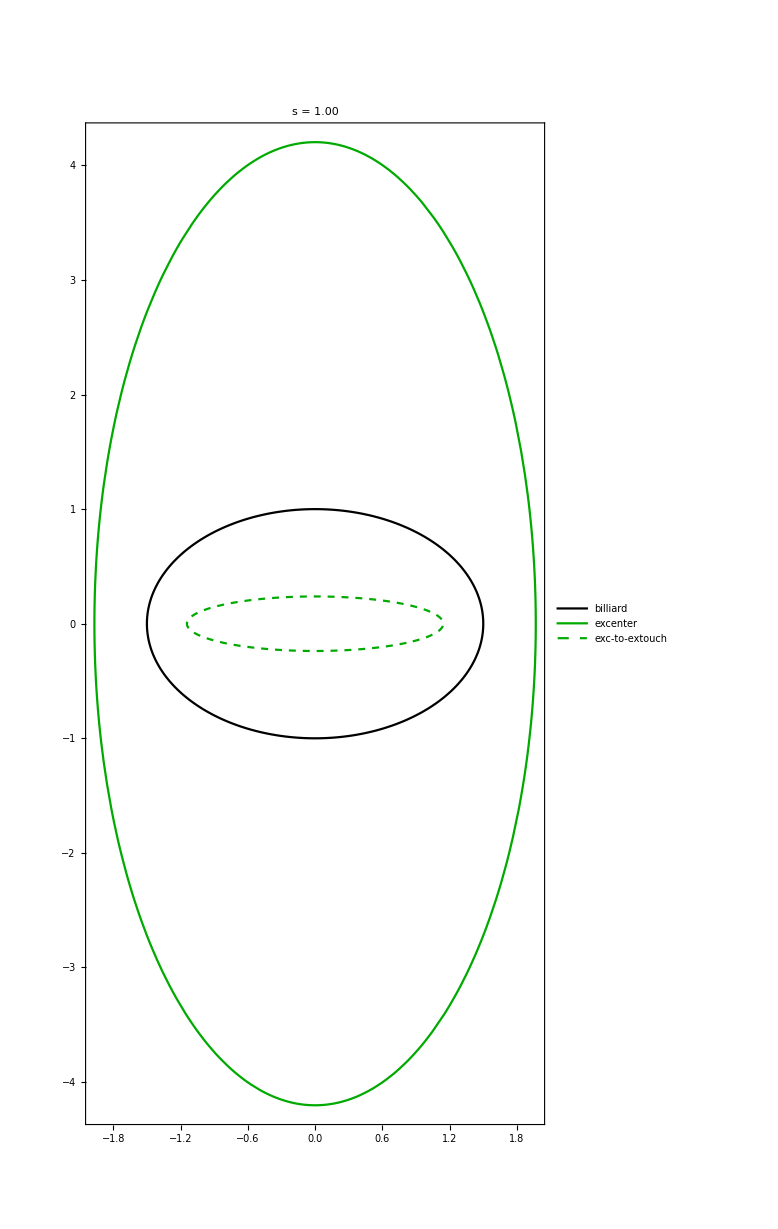

```mathematica
convExcTps[1.5,1]
```

#### Orthocenter to First Foot

```mathematica
Clear@getConvexOrtLocus;
getConvexOrtLocus[a_,tmax_,s_,(* 0 = orthocenter, 1 = foot *)
ps_:("ort"/.ptClrs)]:=Module[{orbit,normals,ort,feet},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
ort=getOrthocenter@@orbit;
feet=getAltBases@@orbit;
convexPts[ort,feet[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convOrtFoot[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
orthocenterLocus[a,π/1.2,{"ort"/.ptClrs}],
getConvexOrtLocus[a,2π,s,{Dashed,"ort"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"ort","ort"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"orthocenter","ort-to-foot"}]]]//Quiet
```

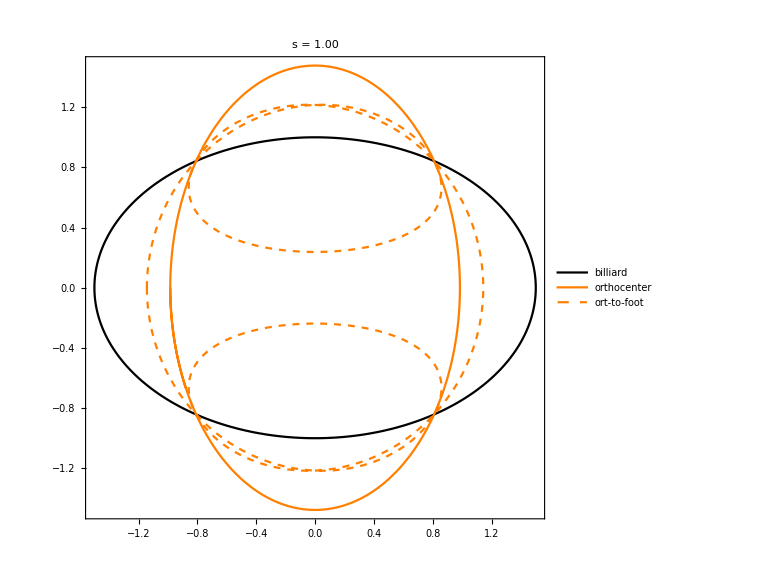

```mathematica
convOrtFoot[1.5,1]
```

#### Circumcenter to First Vertex

```mathematica
Clear@getConvexCirLocus;
getConvexCirLocus[a_,tmax_,s_,(* 0 = circumcenter, 1 = vertex *)
ps_:("cir"/.ptClrs)]:=Module[{orbit,normals,cir},
ParametricPlot[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
(*&&&*)
cir=getCircumcenter@@orbit;
convexPts[cir,orbit[[1]],s],
{t,0,tmax},PlotStyle->ps]
];
```

```mathematica
convCirVtx[a_,s_]:=Module[{lgt=.2},
Legended[Show[{
plotEll[a],
circumcenterLocus[a,π/1.2,{"cir"/.ptClrs}],
getConvexCirLocus[a,2π,s,{Dashed,"cir"/.ptClrs}]},
ImageSize->Large,Frame->True,AxesStyle->Lighter@Gray,PlotRange->All,
PlotLabel->Style["s = "<>nf[s],20]],
LineLegend[MapThread[
Directive[{Thickness@Large,#2,#1/.ptClrs}]&,
{{"ell",(*"feu",*)"cir","cir"},
{{},(*{},*){},Dashed}}],
{"billiard",(*"caustic",*)"circumcenter","circ-to-vertex"}]]]//Quiet
```

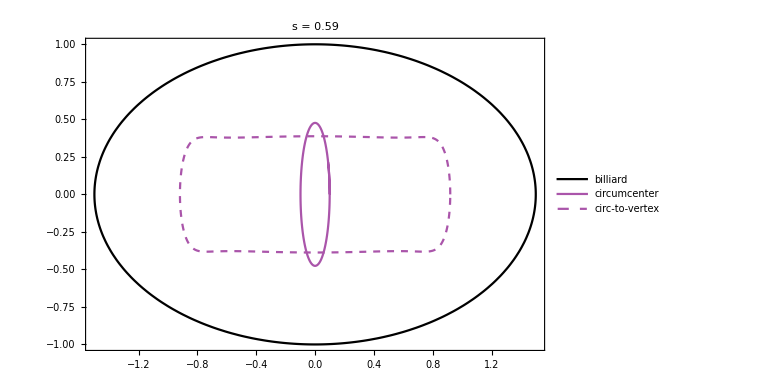

```mathematica
convCirVtx[1.5,.585]
```

```mathematica
Clear@combineConvexOrtCir;combineConvexOrtCir[a_,s_,imgSize_:800]:=
Grid[{{},
{convOrtFoot[a,s],convCirVtx[a,s]}}
];
```

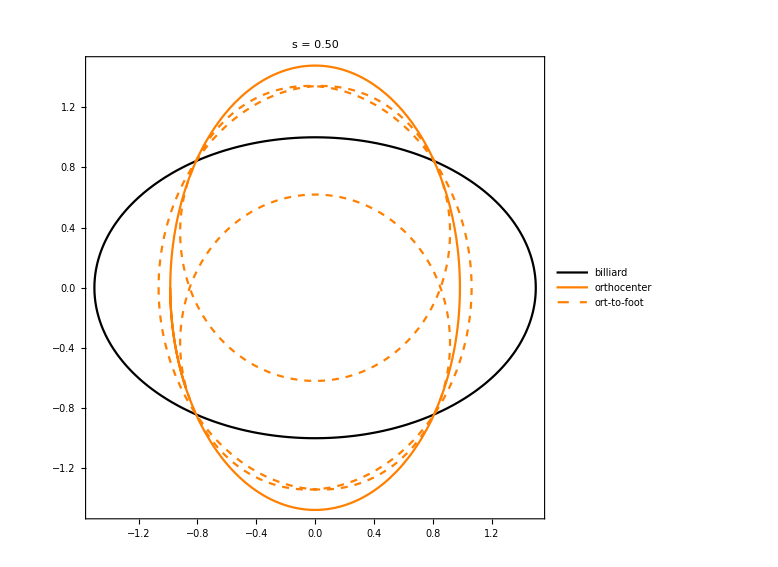
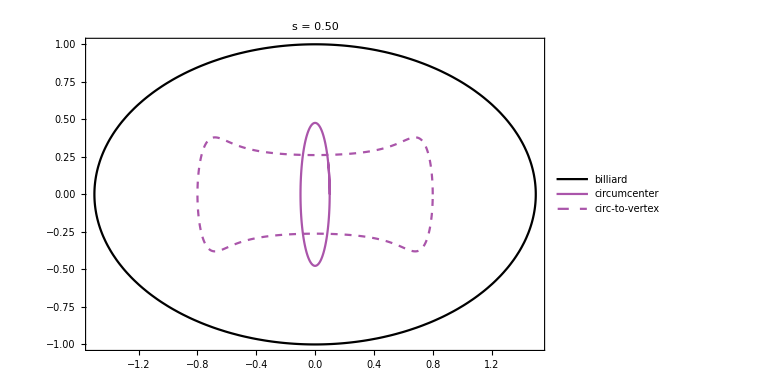
| 
-Graphics- | -Graphics-

```mathematica
combineConvexOrtCir[1.5,.5]
```

## Circumbilliard II (using linear algebra)

```mathematica
ellExtremum[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_},t_]=Module[{xt,yt},
xt=mx+t vx;
yt=my+t vy;
Collect[1+c1 xt+c2 yt+c3 xt yt+c4 xt^2+c5 yt^2,t]]
```

1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2+t (c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy)+t^2 (c4 vx^2+c3 vx vy+c5 vy^2)

```mathematica
(* by symmetry, b=0 of the quadratic*)
Clear@ellExtremumSym;
ellExtremumSym[{mx_,my_},{vx_,vy_},{c1_,c2_,c3_,c4_,c5_}]:=Module[{a,c,d,sqrtd,sol},
a=c4 vx^2+c3 vx vy+c5 vy^2;
(* b=c1 vx+2 c4 mx vx+c3 my vx+c2 vy+c3 mx vy+2 c5 my vy; *)
c=1+c1 mx+c4 mx^2+c2 my+c3 mx my+c5 my^2;
(*(-b + sqrt(b2-4ac)/(2a)) => sqrt(-4ac)/(2a) => sqrt(-ac)/a*)  
sol=Sqrt[-c/a];(*Sqrt[-a*c]/a;*)(* sqrt(-a)*sqrt(c)/a => sqrt(c/a) *)
{sol,-sol}];
```

```mathematica
Clear@getCircumII;
getCircumII[orbit_]:=Module[{mit,mtx123,mtx45,mtx,rhs,ls,hess,vals,vects,lengths,lgt1,lgt2},
mit=getMittenTrilin[orbit,RotateLeft@triLengths@orbit];
mtx123={#[[1]],#[[2]],#[[1]]*#[[2]],#[[1]]^2,#[[2]]^2}&/@orbit;
mtx45={
{1,0,mit[[2]],2mit[[1]],0},
{0,1,mit[[1]],0,2mit[[2]]}};
mtx=Join[mtx123,mtx45];
rhs={-1,-1,-1,0,0};
ls=LinearSolve[mtx,rhs];
hess={{2ls[[4]],ls[[3]]},{ls[[3]],2ls[[5]]}};
{vals,vects}=Eigensystem@hess;
lgt1=Abs[First@ellExtremumSym[mit,vects[[1]],ls]];
(*lgt1=Abs@First[zzz/.Solve[ellExtremum[mit,vects[[1]],ls,zzz]==0,zzz]];*)
lgt2=lgt1*Sqrt[vals[[1]]/vals[[2]]];
(*lengths=(Abs@First[zzz/.Solve[ellExtremum2[mit,#,ls,zzz]==0,zzz]])&/@vects;*)
lengths={lgt1,lgt2};
<|"ctr"->mit,"coeffs"->Chop@ls,"vals"->Chop@vals,"axes"->Chop@vects,"lengths"->lengths|>];
```

```mathematica
getCircumII[orbitNormals[1.5,π/3.][[1]]]
```

<|ctr→{0.,-6.24567×10^-16},coeffs→{0,0,0,-0.444444,-1.},vals→{-2.,-0.888889},axes→{{0,1.},{-1.,0}},lengths→{1.,1.5}|>

```mathematica
Clear@drawCircumII;
Options@drawCircumII={ctrLab->"M",drTri->False,ps->Black};
drawCircumII[tri_,OptionsPattern[]]:=Module[{cII,o,vl,v,ul,u,mit,pp,ax1,ax2,gr},
cII=getCircumII[tri];
o=cII["ctr"];
vl=cII["lengths"][[1]];
v=cII["axes"][[1]];
ul=cII["lengths"][[2]];
u=cII["axes"][[2]];
mit=cII["ctr"];
pp=ParametricPlot[o+vl Cos[t]v+ul Sin[t] u,{t,0,2π},PlotStyle->OptionValue@ps];
ax1=ParametricPlot[(o+vl v)t+(o-vl v)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];
ax2=ParametricPlot[(o+ul u)t+(o-ul u)(1-t),{t,0,1},PlotStyle->{Dashed,OptionValue@ps}];
gr=Graphics[{OptionValue@ps,PointSize@Large,Point@mit,Text[Style[OptionValue@ctrLab,16],mit,{0,-1.5}],If[OptionValue@drTri,{FaceForm@{OptionValue@ps,Opacity@.1},EdgeForm@OptionValue@ps,Polygon@tri},{}]}];
Show[{pp,ax1,ax2,gr}]];
```

```mathematica
Module[{tri,act},
Manipulate[
tri={P1,P2,P3};
act=anticomplementaryTriangle[tri,RotateLeft@triLengths@tri];
Show[{drawCircumII[tri,drTri->True,ctrLab->"M"],
drawCircumII[act,drTri->True,ps->Blue]},Frame->True(*,PlotLabel->Grid[Transpose@{{P1},{P2},{P3}}]*),
PlotRange->{{-2,3},{-2,3}}],
{{P1,{0.0,0.001}},Locator},
{{P2,{1,0}},Locator},
{{P3,{1.5,1.5}},Locator}
]]
```

```mathematica
CloudDeploy[%,Permissions->"Public"]
```

CloudObject[]

## *** Viz Preliminaries

```mathematica
adjExcName[name_]:=StringDrop[name,1]//ToLowerCase;
```

```mathematica
Clear@getShowable;getShowable[str_,showables_]:=ListQ@FirstPosition[showables,str];(* when not found returns "Missing[]"*)
```

```mathematica
Clear@drawSimT;
(* precompute loci *)
Options@drawSimT={ImageSize->800,labExtra->"",showablesOpt->{}};
drawSimT[a_,t_,ellPlot_,causticPlot_,loci_,opt:OptionsPattern[]]:=Module[{showables,incPlot,ellP,orbitData,orbit,normals,notables,exc,npc,
excNormals,excNotables,excCircleData,excOrtFeet,medians,excTps,orthic,
sides,pl,actData,lgt=.33},
showables=OptionValue@showablesOpt;
ellP={N@a * Cos[N@t],Sin[N@t]};
orbitData=getOrbitData[N[a],ellP[[1]],posY->(ellP[[2]]>0)];
orbit="orbit"/.orbitData;
sides=RotateLeft[triLengths@orbit];
normals="normals"/.orbitData;
notables=getNotables[orbit,normals];
exc="exc"/.notables;
medians="medians"/.notables;
npc="npc" /.notables;
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excOrtFeet=getAltBases@@exc;
excCircleData=getExcircleData[orbit,exc(*12,23,31*),npc];
excTps="tps"/.excCircleData;
orthic=getOrthicData[orbit];
actData=getAnticomplData[orbit,sides];
pl=OptionValue@labExtra<>"a="<>nf@a<>"; t="<>nf0@toDeg[t]<>"°";
Show[{
ellPlot,
If[getShowable["orbit",showables],drawOrbit[orbitData,lgt,getShowable["normals",showables]],{}],
If[getShowable["caustic",showables],causticPlot,{}],
If[getShowable["loci",showables],loci,{}],
If[getShowable["notablelines",showables],drawNotableLines@notables,{}],(* remove excenters from here *)
If[getShowable["basicnotables",showables],drawBasicNotables@notables,{}],(* remove excenters from here *)
If[getShowable["notables",showables],drawNotables@notables,{}],(* remove excenters from here *)
If[getShowable["feuerbachline",showables],Graphics[{Black,Dashed,Line[{"feu"/.notables,"npc"/.notables}]}],{}],
If[getShowable["baricenter",showables],Graphics[{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.notables,"B",0,-2,16]}],{}],
If[getShowable["incircle",showables],Graphics[{"inc"/.ptClrs,PointSize@Large,Point["inc"/.notables],
{Thick,Circle["inc"/.notables,"incRadius"/.notables]},
drawOneNotable["inc"/.ptClrs,"inc"/.notables,"I",0,-1.5,16]}],{}],
If[getShowable["circumcircle",showables],Graphics[{"cir"/.ptClrs,PointSize@Large,Point["cir"/.notables],
{Thick,Circle["cir"/.notables,"cirRadius"/.notables]},
drawOneNotable["cir"/.ptClrs,"cir"/.notables,"C",0,-1.5,16]}],{}],
If[getShowable["intouchpts",showables],Graphics[{PointSize@Large,"inc"/.ptClrs,Point["tps"/.notables]}],{}],
If[getShowable["excircles" ,showables],Graphics[{"exc"/.ptClrs,
{PointSize@Large,Point@exc},
{Thick,MapThread[Circle[#1,#2]&,{exc,"radii" /.excCircleData}]}
}],{}],
If[getShowable["ninepointcircle",showables],Graphics[{"npc"/.ptClrs,PointSize@Large,Point["npc"/.notables],
{Thick,Circle["npc"/.notables,"npcRadius"/.notables]},
drawOneNotable["npc"/.ptClrs,"npc"/.notables,"9",0,-1.5,16]}],{}],
If[getShowable["medians",showables],Graphics[{"med"/.ptClrs,PointSize@Medium,Point@medians}],{}],
If[getShowable["nagel",showables],Graphics[{PointSize@Large,drawOneNotable["nag"/.ptClrs,"nag"/.notables,"N"]}],{}],
If[getShowable["feuerbach",showables],Graphics[{PointSize@Large,
drawOneNotable["feu"/.ptClrs,"feu"/.notables,"F",0,-1.5,16]}],{}],
If[getShowable["inc2nagel",showables],Graphics[{"nag"/.ptClrs,Line[{"nagel"/.excCircleData,"inc"/.notables}]}],{}],
If[getShowable["mittenpunkt",showables],Graphics[{("mit"/.ptClrs),PointSize@Large,Point["mitten"/.excCircleData],
drawOneNotable["mit"/.ptClrs,"mitten"/.excCircleData,"M",0,-2,16]}],{}],
If[getShowable["mittenfeet",showables],Graphics[{("mit"/.ptClrs),Thickness@Medium,Dashed,
MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]}],{}],
(* exc objects *)
If[getShowable["extriangle",showables],Graphics[{FaceForm[None],EdgeForm[{Thick,("exc"/.ptClrs)}],Polygon@exc,("exc"/.ptClrs),PointSize@Large,Point@exc}],{}],
If[getShowable["exbisectors",showables],Graphics[{("exc"/.ptClrs),FaceForm[None],Arrowheads[Medium],MapThread[Arrow[{#1,ray[#1,#2,.5]}]&,{exc,excNormals}]}],{}],
If[getShowable["exnotablelines",showables],drawNotableLines@excNotables,{}],
If[getShowable["exnotables",showables],drawNotables[excNotables,"x"],{}],
If[getShowable["extouchpts" ,showables],Graphics[{("exc"/.ptClrs),PointSize@Large,Point@excTps}],{}],
If[getShowable["extouchtri" ,showables],Graphics[{FaceForm@None,EdgeForm@{Thick,"exc"/.ptClrs},Polygon@excTps}],{}],
If[getShowable["extouchpts" ,showables]&&getShowable["excircles",showables],Graphics[{("exc"/.ptClrs),Dashed,Thick,MapThread[Line@{#1,#2}&,{exc,excTps}]}],{}],
If[getShowable["extouchptlabels" ,showables],Graphics[MapThread[drawOneNotable[("exc" /.ptClrs),#1,#2]&,
{excTps,Subscript["t",#]&/@{"12","23","31"}}]],{}],
If[getShowable["extouchtriangle" ,showables],Graphics[{EdgeForm[{Black}],Polygon@excTps}],{}],
If[getShowable["exfeuerbach" ,showables],
Graphics[{PointSize@Medium,("npc"/.ptClrs),Point["feus"/.excCircleData](*drawOneNotable[("npc" /.ptClrs),#,"xFeu"]&/@("feus"/.excCircleData)*)}],{}],
If[getShowable["exbaricenter",showables],Graphics[{PointSize@Large,drawOneNotable["bar"/.ptClrs,"bar"/.excNotables,"xB"]
}],{}],
If[getShowable["exnpc",showables],Graphics[{("npc"/.ptClrs),Thick,Circle[npc,"npcRadius"/.excNotables]}],{}],
If[getShowable["hexyltriangle",showables],Module[{hex},
hex=hexylTriangle[orbit,sides];
Graphics[{FaceForm@None,EdgeForm["hex"/.ptClrs],Polygon@hex,PointSize@Medium,"hex"/.ptClrs,Point@hex}]],{}],
If[getShowable["outernapoleon",showables],Module[{nap},
nap=outerNapoleonTriangle[orbit,sides];
Graphics[{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@nap,PointSize@Medium,"nap"/.ptClrs,Point@nap}]],{}],
If[getShowable["morleytriangle",showables],Module[{morley,c1},
morley=firstMorleyTriangle[orbit,sides];
c1=getFirstMorleyTrilin[orbit,sides];
Graphics[{FaceForm@None,EdgeForm["nap"/.ptClrs],Polygon@morley,PointSize@Medium,"nap"/.ptClrs,Point@morley,Black,Point@c1}]],{}],
If[getShowable["orthictriangle",showables],
Graphics[{
{EdgeForm@Black,FaceForm[{"ort"/.ptClrs,Opacity@.3}],Polygon["feet"/.orthic]},
{EdgeForm["inc"/.ptClrs],FaceForm[{Lighter@Green,Opacity@.3}],Polygon["intouch"/.orthic],Gray,Circle["inc"/.orthic,"inradius"/.orthic]},
{FaceForm@None,EdgeForm@Red,Polygon["intouchOrt"/.orthic],Red,Point["intouchOrtInc"/.orthic]},
{PointSize@Medium,"ort"/.ptClrs,Point["feet"/.orthic],PointSize@Large,Point["ort"/.notables](*,drawOneNotable["ort"/.ptClrs,"ort"/.notables,"O"]*)},
(*{Dashed,Gray,MapThread[Line[{#1,#2}]&,{orbit,ortFeet}]},*)
{Dashed,Gray,Line[{#,"ort"/.notables}]&/@orbit},
{PointSize@Large,"inc"/.ptClrs,Point["inc"/.orthic]}}],{}],
If[getShowable["anticompl",showables],
Graphics[{FaceForm@None,
{EdgeForm[{Thick,"anticompl"/.ptClrs}],Polygon@actData["tri"]},
{PointSize@Large,"anticompl"/.ptClrs,Point@actData["tri"]}}],{}],
If[getShowable["anticomplcircs",showables],
Graphics[{FaceForm@None,PointSize@Large,
{{"inc"/.ptClrs,Point@actData["inc"],drawOneNotable["inc"/.ptClrs,actData["inc"],OverBar["I"],0,-1.5,16],
{PointSize@Large,Point@actData["tps"]},Dashed,Line[{actData["inc"],#}]&/@actData["tps"]},
{"npc"/.ptClrs,Point@actData["npc"],drawOneNotable["npc"/.ptClrs,actData["npc"],OverBar["9"],0,-1.5,16]}},
{Thick,"inc"/.ptClrs,Circle[actData["inc"],actData["incR"]],"npc"/.ptClrs,Circle[actData["npc"],actData["npcR"]]}
}],{}],
If[getShowable["anticomplincirc",showables],
Graphics[{FaceForm@None,PointSize@Large,
{{"inc"/.ptClrs,Point@actData["inc"],drawOneNotable["inc"/.ptClrs,actData["inc"],OverBar["I"],0,-1.5,16],
{PointSize@Large,Point@actData["tps"]},Dashed,Line[{actData["inc"],#}]&/@actData["tps"]}},
{Thick,"inc"/.ptClrs,Circle[actData["inc"],actData["incR"]]}
}],{}],
If[getShowable["anticomplcircumb",showables],drawCircumII[actData["tri"],ctrLab->OverBar["M'"]],{}],
If[getShowable["darbouxpt",showables],Module[{p1,p2,dbx},
{p1,p2}=Take[actData["tri"],2];
dbx=interRays[p1,excTps[[2]]-p1,p2,excTps[[3]]-p2];
Graphics[{Thick,Dashed,PointSize@Large,Red,
MapThread[Line@{#1,ray[#1,#2-#1,5]}&,{actData["tri"],RotateLeft@excTps}],
drawOneNotable[Red,dbx,"D",0,-1.5,16],Point@dbx,Cyan,Point@getX144Trilin[orbit,sides]}]],{}],
If[getShowable["antifeuerbach",showables],Graphics[{
{Dashed,Gray,Line[{"antifeu","feu"}/.notables]},
PointSize@Large,drawOneNotable["feu"/.ptClrs,"antifeu"/.notables,OverBar["F"],0,-1.5,16]}],{}],
If[getShowable["experimental",showables],Module[{cir="cir"/.notables,rad,equi,xfeus,xfeusCir,xtpsCir,cirClr,medsCir},
cirClr="cir"/.ptClrs;
rad="cirRadius"/.notables;
xfeus=("feus"/.excCircleData);
equi=(cir+#)&/@(rad getEquilateral[0.]);
xfeusCir=getCircumcenter@@xfeus;
xtpsCir=getCircumcenter@@excTps;
medsCir=getCircumcenter@@medians;
Graphics[{FaceForm@None,PointSize@Large,
{cirClr,EdgeForm@cirClr,Polygon@equi,Polygon[flipX/@equi]},
(*{EdgeForm@cirClr,Polygon[ray[cir,norm[#-cir],rad]&/@xfeus]},
{EdgeForm["exc"/.ptClrs],Polygon[ray[cir,norm[#-cir],rad]&/@excTps]},*)
(* o circulo pelos xfeus (ou medianas) tb  por feu e é o 9-point-circle! *)
(*{"feu"/.ptClrs,Point@xfeusCir,Dashed,Circle[xfeusCir,magn[xfeus[[1]]-xfeusCir]]},
{"med"/.ptClrs,Point@medsCir,Dashed,Circle[medsCir,magn[medians[[1]]-medsCir]]},*)
{"exc"/.ptClrs,Point@xtpsCir,Dashed,Thick,Circle[xtpsCir,magn[excTps[[1]]-xtpsCir]]}
(*{"med"/.ptClrs,PointSize@Large,Point@medians}*)
}]],{}]},
(*drawOneNotable[Red,#,"xFoot"]&/@excOrtFeet*)
AspectRatio->Automatic,Frame->True,Axes->True,
AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style[pl,{Black,20}],FilterRules[{opt},Options@Plot]]];
```

```mathematica
orthocenterMaxY[a_,tmax_]:=Module[{orbit,normals,orthocenter,theY},
(* FindMaximum[] pukes *)
Table[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
orthocenter=getOrthocenter@@orbit;
theY=orthocenter[[2]];
theY,{t,0,tmax,π/360}]
]//Max;
```

```mathematica
anticomplMax[a_,tmax_]:=Module[{orbit,normals,act,acts},
(* FindMaximum[] pukes *)
acts=Table[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
act=anticomplementaryTriangle[orbit,RotateLeft@triLengths[orbit]];
act[[1]],
{t,0,tmax,π/360}];
{Max[Abs/@First/@acts],Max[Abs/@Second/@acts]}];
```

```mathematica
Clear@excenterMax;
excenterMax[a_]:=Module[{orbit,normals,excenter,theX,coords},
(* FindMaximum[] pukes *)
coords=Table[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
getExcenters[orbit,normals][[1]],
{t,0,2π,2π/360}];
{Max[First/@coords],Max[Take[#,2]&/@coords]}
];
```

```mathematica
excenterMax[1.5]
```

{1.96837,4.20221}

known results, verified below: incenter = orthocenter (ex - triangle), and circumcenter = npc (ex - triangle)
http://mathworld.wolfram.com/ExcentralTriangle.html

```mathematica
Options@drawSimT
```

{ImageSize→800,labExtra→,showablesOpt→{}}

```mathematica
Clear@movieFrame;
Options@movieFrame={labExtra->"",showablesOpt->{},ImageSize->800};
movieFrame[a_,t_,ellPlot_,causticPlot_,loci_,excenterLims_,clip_,opts:OptionsPattern[]]:=Module[{prX,prY,maxX,maxY,maxYort,actMax},
maxX=Round[excenterLims[[1]]+.1,.1];
maxYort=Round[orthocenterMaxY[a,π/1.2]+.1,.1];
maxY=Round[excenterLims[[2]]+.1,.1];
(*Print[FilterRules[{opts},Options@Show]];*)
actMax=anticomplMax[a,π];
prX=Switch[clip,
"anticompl",{-actMax[[1]],actMax[[1]]},
"anticompl2",{-actMax[[1]],actMax[[1]]},
_,{-maxX,maxX}];
prY=Switch[clip,
"ell",{-1.1,1.1},
"ort",{-maxYort,maxYort},
"ortHalf",.5{-(1.1+maxYort),(1.1+maxYort)},
"excHalf",{-maxY,maxY}*.5,
"anticompl",{-actMax[[2]],actMax[[2]]},
"anticompl2",1.5{-actMax[[2]],actMax[[2]]},
_,{-maxY,maxY}];
Show[drawSimT[a,t,ellPlot,causticPlot,loci,FilterRules[{opts},Options@drawSimT]],
PlotRange->{prX,prY},
FilterRules[{opts},Options@Plot]]];
```

```mathematica
showablesAll={
(*00*)"orbit",
(*01*)"loci",
(*02*)"normals",
(*03*)"medians",
(*04*)"baricenter",
(*05*)"mittenpunkt",
(*06*)"caustic",
(*07*)"notables",
(*08*)"notablelines",
(*09*)"incircle",
(*10*)"intouchpts",
(*11*)"ninepointcircle",
(*12*)"feuerbach",
(*13*)"feuerbachline",
(*14*)"extriangle",
(*15*)"excircles",
(*16*)"exnotables",
(*17*)"exnotablelines",
(*18*)"extouchpts",
(*19*)"exbaricenter",
(*20*)"exfeuerbach",
(*21*)"antifeuerbach",
(*22*)"circumcircle",
(*23*)"experimental",
(*24*)"orthictriangle",
(*25*)"basicnotables",
(*26*)"outernapoleon",
(*27*)"hexyltriangle",
(*28*)"morleytriangle",
(*29*)"anticompl",
(*30*)"mittenfeet",
(*31*)"anticomplcircumb",
(*32*)"anticomplcircs",(* incircle and 9pt *)
(*33*)"extouchtri",
(*34*)"anticomplincirc",
(*35*)"darbouxpt"
};
showablesExp={
{"manual",{}},
{"all",showablesAll},
{"none",{}},
{"mitten",{"medians","extriangle","mittenpunkt","mittenfeet","excircles"}},
{"caustic",{"medians","extriangle","excircles","extouchpts","intouchpts","incircle","ninepointcircle","feuerbach","feuerbachline","exfeuerbach"}},
{"exfeuer",{"ninepointcircle","extriangle","excircles","extouchpts","exfeuerbach","feuerbach","incircle"}},
{"touchpts",{"medians","incircle","intouchpts","extriangle","excircles","extouchpts"}},
{"antifeuer",{"ninepointcircle","incircle","feuerbach","baricenter","antifeuerbach"}},
{"feuerall",{"medians","incircle","caustic" ,"extriangle","excircles","extouchpts","ninepointcircle","feuerbach","baricenter","antifeuerbach","exfeuerbach"}},
{"orthicinc",{"orthictriangle"}},
{"anticomplSimple",{"caustic","baricenter","feuerbach","antifeuerbach","anticompl","mittenpunkt","anticomplcircumb","anticomplcircs"}},{"anticompl",{"caustic","baricenter","feuerbach","antifeuerbach","incircle","ninepointcircle","excircles","extouchpts","anticompl","mittenpunkt"}},
{"darboux",{"caustic","baricenter","anticompl","extouchpts","extouchtri","anticomplincirc","darbouxpt","feuerbach","antifeuerbach"}}
};
```

```mathematica
getExpShowables[exp_]:=showablesExp[[FirstPosition[First/@showablesExp,exp]//First]][[2]];
```

## *** Main Viz App

```mathematica
assign[symbols_,idx_,val_]:=symbols[[{idx}]]/._[x_]:>(x=val);
```

```mathematica
makeCtrlCol[ctrls_]:=Column[{Style[First@ctrls,Bold,Medium],Sequence@@Rest[ctrls]},Alignment->Right,BaselinePosition->1];
```

```mathematica
Module[{a=1.5,ellPlot,causticPlot,loci,excenterLims,showables,showableItems,ctrList,symbols},
ellPlot=plotEll[a];
causticPlot=plotEllb[Sequence@@getTriCausticParams[a],"feu"/.ptClrs];
loci=precompLoci[a];
excenterLims=excenterMax[a];
Manipulate[
(* this must be in the same order as showablesAll *)
ctrList=Hold[drOrbit,drLoci,drNormals,drMedians,drBaricenter,drMitten,drCaustic,drNotables,drNotableLines,
drIncircle,drIntouchpts,drNpc,drFeuerbach,drFeuerLine,
drExtriangle,drExcircles,drExcNotables,drExcNotableLines,drExtouchpts,drExcBar,drExcFeuer,
drAntiFeuerbach,drCircumcircle,drExperimental,drOrthicTri,drBasicNotables,drOuterNapoleonTri,drHexylTri,drMorleyTri,drAntiComplTri,drMittenFeet,drAntiComplCircumb,drAntiComplCircs,drExtouchTri,drAntiComplIncirc,drDarbouxPt];
(* &&& FIX *)
showables=If[exp!="manual",
showableItems=Prepend[getExpShowables[exp],"orbit"];
MapIndexed[assign[ctrList,First@#2,Count[showableItems,#1]>0]&,showablesAll];
exp="manual";
showableItems,
(* else *)
Pick[showablesAll,Evaluate[List@@ctrList]]];
(*movieFrame[a_,t_,ellPlot_,loci_,excenterLims_,clip_,opt:OptionsPattern[]]*)
movieFrame[a,toRad@tDeg,ellPlot,causticPlot,loci,excenterLims,clip,showablesOpt->showables,ImageSize->600],
{{tDeg,0},-360,360,1,Appearance->"Labeled"},
Row[{Control[{{clip,"ort",""},{"ell","ort","ortHalf","excHalf","exc","anticompl","anticompl2"}}],
Control[{{exp,"manual",""},First/@showablesExp}]}],
(*Sequence@@MapThread[{{#1,False,#2},{False,True}}&,{ctrList,showablesAll}]*)
Column[{Row[makeCtrlCol/@{
{"basic",
Control[{{drOrbit,True, "orbit"},{False,True}}],
Control[{{drCaustic,False, "caustic"},{False,True}}],
Control[{{drLoci,False, "loci"},{False,True}}],
Control[{{drNormals,False,"normals"},{False,True}}]
},
{"notables",
Control[{{drBasicNotables,False,"basicnotables"},{False,True}}],
Control[{{drNotables,False,"notables"},{False,True}}],
Control[{{drBaricenter,False,"baricenter"},{False,True}}],
Control[{{drFeuerbach,False,"feuerbach"},{False,True}}],
Control[{{drAntiFeuerbach,False,"antifeuerbach"},{False,True}}],
Control[{{drMitten,False,"mittenpunkt"},{False,True}}]
},
{"circles",
Control[{{drIncircle,False,"incircle"},{False,True}}],
Control[{{drCircumcircle,False,"circumcircle"},{False,True}}],
Control[{{drNpc,False,"ninepointcircle"},{False,True}}],
Control[{{drExcircles,False,"excircles"},{False,True}}]
},
{"lines",
Control[{{drNotableLines,False,"notablelines"},{False,True}}],
Control[{{drFeuerLine,False,"feuerbachLine"},{False,True}}]
}},Spacer[10],Alignment->{Right,Top}],
Row[makeCtrlCol/@{
{"triads",
Control[{{drMedians,False,"medians"},{False,True}}],
Control[{{drIntouchpts,False,"intouchpts"},{False,True}}],
Control[{{drExtouchpts,False,"extouchpts"},{False,True}}],
Control[{{drExcFeuer,False,"exfeuerbach"},{False,True}}]
},
{"ex",
Control[{{drExcBar,False,"exbaricenter"},{False,True}}],
Control[{{drExcNotables,False,"exnotables"},{False,True}}],
Control[{{drExcNotableLines,False,"exnotablelines"},{False,True}}]
},
{"tris",
Control[{{drExtriangle,False,"excentral"},{False,True}}],
Control[{{drOrthicTri,False,"orthic"},{False,True}}],
(*Control[{{drHexylTri,False,"hexyl"},{False,True}}],
Control[{{drOuterNapoleonTri,False,"outernapoleon"},{False,True}}],*)
Control[{{drMorleyTri,False,"morley"},{False,True}}],
Control[{{drAntiComplTri,False,"anticompl"},{False,True}}],
Control[{{drExtouchTri,False,"extouchtri"},{False,True}}]
},
{"misc",
Control[{{drMittenFeet,False,"mittenfeet"},{False,True}}],
Control[{{drAntiComplIncirc,False,"anticomplincirc"},{False,True}}],
Control[{{drAntiComplCircs,False,"anticomplcircs"},{False,True}}],
Control[{{drAntiComplCircumb,False,"anticomplcircumb"},{False,True}}],
Control[{{drDarbouxPt,False,"darbouxpt"},{False,True}}],
Control[{{drExperimental,False,"experimental"},{False,True}}]
}},Spacer[10],Alignment->{Right,Top}]},
Spacings->{2.5,.5},Frame->True,Alignment->Right],
SaveDefinitions->True,ControlPlacement->Left]]
```

## Study Angular Momentum

https : // mobile.twitter.com/gregegansf/status/1037963743517261829

```mathematica
getMomentum[p1_,p2_]:=Module[{lgt,d},
lgt=magn[p2-p1];
d=magn[closestPerp[{0,0},p1,p2]];
(*d=magn[(p1+p2)/2];*)
{lgt,d}];
getMomentumTri[p1_,p2_,p3_]:=#[[1]]*#[[2]]&/@{getMomentum[p1,p2],getMomentum[p2,p3],getMomentum[p3,p1]};
```

```mathematica
{x1,y1,0}×{x2,y2,0}
```

{0,0,-x2 y1+x1 y2}

```mathematica
crossProduct[{x1_,y1_},{x2_,y2_}]:=-x2 y1 + x1 *y2
```

```mathematica
getMomentumFoci[f1_,f2_,p1_,p2_]:=Module[{edge,d1,d2},
edge=norm[p2-p1];
d1=crossProduct[edge,p1-f1];
d2=crossProduct[edge,p1-f2];
d1*d2];
```

```mathematica
Clear@getMomenta;
getMomenta[a_]:=Module[{orbit,normals},
Table[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
{t,getMomentum[orbit[[1]],orbit[[2]]]},{t,0,2.π,toRad[1.]}]
];
```

```mathematica
Clear@getMomentaFoci;
getMomentaFoci[a_]:=Module[{orbit,normals,c,f1,f2},
c=focalDistance[a,1];
f1={c,0};
f2={-c,0};
Table[
{orbit,normals}=Evaluate[orbitNormals[a,t]];
{t,{getMomentumFoci[f1,f2,orbit[[1]],orbit[[2]]],
getMomentumFoci[f1,f2,orbit[[2]],orbit[[3]]],
getMomentumFoci[f1,f2,orbit[[3]],orbit[[1]]]}},{t,0,2.π,toRad[1.]}]
];
```

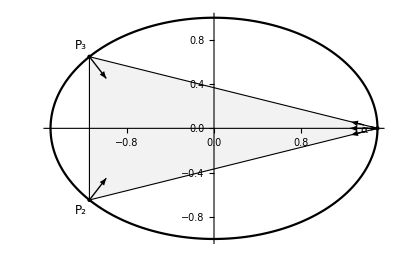

```mathematica
Show[{plotEll[1.5],drawOrbit[getOrbitData[1.5,1.5]]}]
```

#### Sum of products of distance is *not* conserved

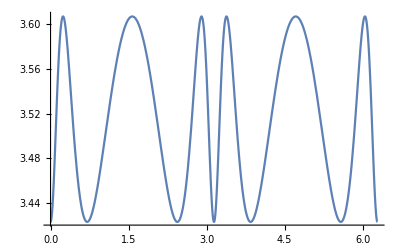

```mathematica
Plot[Total@Module[{o,n},
{o,n}=orbitNormals[1.5,t];
getMomentumTri@@o],{t,0,2π}]
```

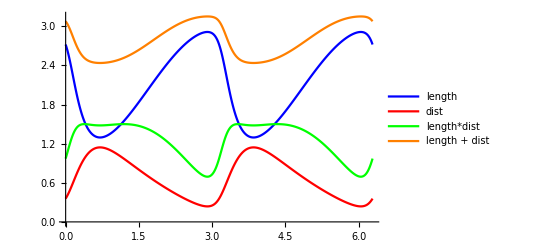

```mathematica
Module[{ms,ts,ls,ds,mults,sums,clrs={Blue,Red,Green,Orange}},
ms=getMomenta[1.5];
ts=First/@ms;
ls=First/@(Second/@ms);
ds=Second/@(Second/@ms);
mults=ls*ds;
sums=ls+ds;
Legended[ListLinePlot[Transpose/@{{ts,ls},{ts,ds},{ts,mults},{ts,sums}},PlotStyle->clrs],
LineLegend[clrs,{"length","dist","length*dist","length + dist"}]]]
```

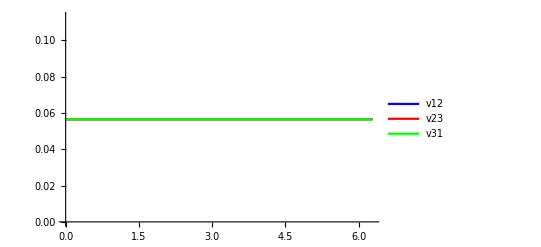

```mathematica
Module[{ms,ts,v12,v23,v31,clrs={Blue,Red,Green}},
ms=getMomentaFoci[1.5];
ts=First/@ms;
v12=First/@(Second/@ms);
v23=Second/@(Second/@ms);
v31=Third/@(Second/@ms);
Legended[ListLinePlot[Transpose/@{{ts,v12},{ts,v23},{ts,v31}},PlotStyle->clrs],
LineLegend[clrs,{"v12","v23","v31"}]]]
```

```mathematica
showTangentToEllipse[a_,t_]:=Module[{c,f1,f2,cl1,cl2,d1,d2,m1,m2,p,gr,bisector,bisectorPerp,lab,lgt=.5},
p={a Cos[t],Sin[t]};
c=focalDistance[1.5,1];
{f1,f2}={{-c,0},{c,0}};
bisector=norm[norm[p-f1]+norm[p-f2]];
bisectorPerp=perp[bisector];
cl1=closestPerp[f1,p,p+bisectorPerp];
cl2=closestPerp[f2,p,p+bisectorPerp];
m1=(f1+cl1)/2;
m2=(f2+cl2)/2;
d1=magn[cl1-f1];
d2=magn[cl2-f2];
lab=Style["d_1d_2="<>nfn[d1*d2,2],{Black,16}];
gr=Graphics[{PointSize@Large,Point@{f1,f2},
{Blue,Dotted,Point@p,Line[{f1,p}],Line[{f2,p}],Arrow[{p,p-bisector*lgt}]},
{Darker@Green,Thick,Line[{p,p+2bisectorPerp}],Line[{p,p-2bisectorPerp}]},
{Dashed,Line[{f1,cl1}],Line[{f2,cl2}]},
MapThread[Text[Style[#1,12],#2,{1.5,-1}]&,{{"d_1","d_2"},{m1,m2}}],
MapThread[Text[Style[#1,12],#2,{0,1.5}]&,{{"F_1","F_2"},{f1,f2}}]}];
Show[{plotEll[1.5,Lighter@Gray],gr},PlotLabel->lab,Frame->True,PlotRange->{{-2,2},{-1.5,1.5}}]];
```

```mathematica
Manipulate[
showTangentToEllipse[1.5,t],
{{t,π/2.},-2π,2π,toRad[.1],Appearance->"Labeled"}]
```

## Study Orbit, Excentral, Orthic Invariants

#### Perimeter invariants 1) orbit: P 2) excentral (r’/R’)P’ = P 3) orthic: P’’ = (r/R)*P: A=r*P/2=R*P’’/2 P’’(R/r) = P [[only works for acute orbits]]

```mathematica
Clear@excPerimeterInvariants;
excPerimeterInvariants[a_,wiggle_:.1]:=Module[{darboux,orbit,normals,per,orbitData,exc,excData,ort,ortData,ortPer,ratioExc,excPer,ratioOrtPer,ortExc,ortExcData,ortExcPer,ratioOrtPerPreImage,excessPerPreImage,ratioOrtPerPreImageAdj},
darboux=darbouxP[a];
Table[
{orbit,normals}=orbitNormals[a,t];
orbitData=getTriData[orbit];
per="perimeter"/.orbitData;
exc=excentralTriangle[orbit,"sides"/.orbitData];
excData=getTriData[exc];
excPer="perimeter"/.excData;
ort=orthicTriangle[orbit,"sides"/.orbitData];
ortData=getTriData[ort];
ortPer="perimeter"/.ortData;
ortExc=excentralTriangle[ort,"sides"/.ortData];
(* acute pre image *)
ortExcData=getTriData[ortExc];
ortExcPer="perimeter"/.ortExcData;
ratioExc=excPer*("rOvR"/.excData);
ratioOrtPer=ortPer/("rOvR"/.orbitData);
ratioOrtPerPreImage=ortPer/("rOvR"/.ortExcData);
excessPerPreImage=ortExcPer-per;
ratioOrtPerPreImageAdj=ratioOrtPerPreImage-excessPerPreImage;
{t,
darboux, (* P (darboux) *)
ratioExc+wiggle, (* P'(r'/R') *)
ratioOrtPerPreImageAdj-wiggle, (* P''*(Subscript[R, acute]/Subscript[r, acute]) - (Subscript[P, acute]-P) *)
ratioOrtPer, (* P''*(R/r) *)
ratioOrtPerPreImage ,(* P''*(Subscript[R, acute]/Subscript[r, acute]) *)
excessPerPreImage (* (Subscript[P, acute]-P) *)
},{t,0,2π,π/100.}]];
```

```mathematica
Clear@showExcPerInvariants;
showExcPerInvariants[a_,wiggle_:.1]:=Module[{pers,tr,ts,clrs={Red,Green,Blue,Orange,Cyan,Purple}},
pers=excPerimeterInvariants[a,wiggle];
tr=Transpose[pers];
ts=tr[[1]];
Legended[
ListLinePlot[
(MapThread[Function[{l1,l2},{l1,l2}],{ts,#}])&/@Rest[tr]
,PlotStyle->clrs,Frame->True,FrameStyle->Medium,ImageSize->Large,FrameLabel->{"t","length"},PlotLabel->Style["a = "<>nfn[a,2],16],PlotRange->All],
LineLegend[Directive/@({#,Thick}&/@clrs),
Style[#,16]&/@{
"P",
"P'(r'/R')",
"P''*(R_acute/r_acute) - (P_acute-P)",
"P''*(R/r)",
"P''*(R_acute/r_acute)",
"(P_acute-P)"
}]]];
```

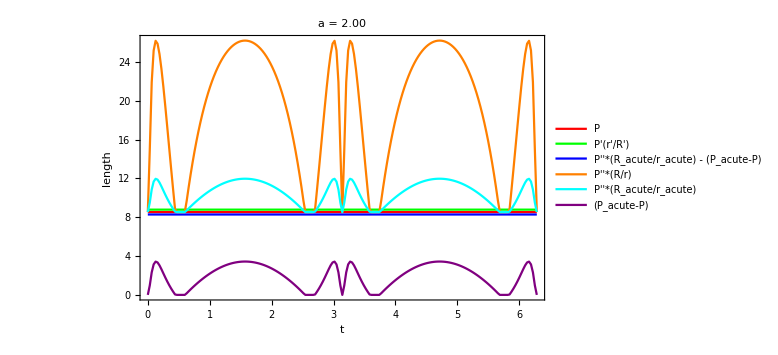

```mathematica
showExcPerInvariants[2,.25]
```

#### Angular Invariants : 1) orbit : sum of cosines = 1 + r/R 2) excentral : product of cosines or - (sum of sines of double angles) = 1 + r/R 3) orthic : sum of sines of half angles = 1 + r/R [[only for acute orbits]]

```mathematica
Clear@excAngleInvariants;
excAngleInvariants[a_]:=Module[{normals,rOvRp1,
orbit,orbitData,orbitCosines,orbitSum,
exc,excData,excCosines,excSum,excProd,
ort,ortData,ortCosines,ortSum},
Table[
{orbit,normals}=orbitNormals[a,t];
orbitData=getTriData[orbit];
rOvRp1=(1+("rOvR"/.orbitData))*.99;
orbitCosines="cosines"/.orbitData;
exc=excentralTriangle[orbit,"sides"/.orbitData];
excData=getTriData[exc];
excCosines="cosines"/.excData;
ort=orthicTriangle[orbit,"sides"/.orbitData];
ortData=getTriData[ort];
ortCosines="cosines"/.ortData;
orbitSum=1.01*Total@orbitCosines;
(* hack: double angle works w/ sin or cos as arg *)
excSum=-.98*Total[cosDoubleAngle/@excCosines];
excProd=1+4*excCosines[[1]]*excCosines[[2]]*excCosines[[3]];
ortSum=Total[sinHalfAngle/@ortCosines];
{t,rOvRp1,orbitSum,excSum,excProd,ortSum},{t,0,2π,toRad[1.]}]];
```

```mathematica
Clear@showExcAngleInvariants;
showExcAngleInvariants[a_]:=Module[{pers,tr,ts,clrs={Red,Green,Blue,Orange,Pink}},
pers=excAngleInvariants[a];
tr=Transpose[pers];
ts=tr[[1]];
Legended[
ListLinePlot[
(MapThread[Function[{l1,l2},{l1,l2}],{ts,#}])&/@Rest[tr],
PlotStyle->clrs,Frame->True,FrameStyle->Medium,ImageSize->Large,FrameLabel->{"t","length"},PlotLabel->Style["a = "<>nfn[a,2],16],PlotRange->{All,{0,2}}],
LineLegend[Directive/@({#,Thick}&/@clrs),
Style[#,16]&/@{
"rOvRp1","orbitSum","excSum","excProd","ortSum"}]]]
```

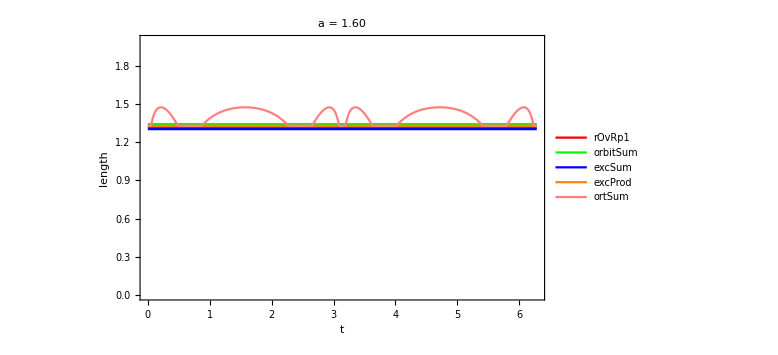

```mathematica
showExcAngleInvariants[1.6]
```

So:
(a/a') = Sin[A/2]
(b/b') = Sin[B/2]
(b/c') = Sin[C/2]

Sin[θ/2]=Sqrt[(1-Cos[θ])/2]
Sin[θ/2]^2=(1-Cos[θ])/2

(a/a')^2+(b/b')^2+(c/c')^2=(1-Cos[A])/2+(1-Cos[B])/2+(1-Cos[C])/2=
(3-Cos[A]-Cos[B]-Cos[C])/2 =should be constant!

Since (proven below): cos[A] + cos[B]+ cos[C] = 1+r/R

(3-Cos[A]-Cos[B]-Cos[C])/2 = (3-1-r/R)/2 = 1-r/(2R)

```mathematica
Clear@showTriExc;showTriExc[a_,t_,test_:False]:=Module[{orbit,normals,exc,excNormals,excNotables,excNpc,excCircleData,orbitSides,excSides,orbitMeds,excMeds,
txts,txtsExc,txtsSides,txtsSidesExc},
{orbit,normals}=orbitNormals[a,t];
(* 23, 13, 12 *) orbitMeds=RotateRight[getMedians@@orbit];
(* 12, 23, 31 *) orbitSides=triSides@orbit;
exc=getExcenters[orbit,normals];
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excMeds="medians"/.excNotables;
excSides="sides"/.excNotables;
excNpc="npc"/.excNotables;
excCircleData=getExcircleData[orbit,exc,excNpc];
(*txts=MapThread[txtSubscript["P",#3,12,ray[#1,-norm@#2,.2]]&,{orbit,normals,{"1","2","3"}}];*)
txts=MapThread[Style[Text[#1,ray[#2,-#3,0.2]],16]&,{{"A","B","C"},orbit,normals}];
txtsExc=MapThread[Style[Text[#1,ray[#2,-#3,0.2]],16]&,{{"C'","A'","B'"},exc,excNormals}];
(*txtsExc=MapThread[txtSubscript["E",#3,12,ray[#1,-norm@#2,.2]]&,{exc,"xNormals"/.excData,{"1","2","3"}}];*)
txtsSides=MapThread[Style[Text[#1,ray[#2,norm[perpNeg[#3]],0.15]],14]&,{{"a","b","c"},orbitMeds,orbitSides}];
txtsSidesExc=MapThread[Style[Text[#1,ray[#2,norm[perpNeg[#3]],0.15]],14]&,{{"a'","b'","c'"},excMeds,RotateLeft@excSides}];
Show[{plotEll[a],
Graphics[{
FaceForm@None,PointSize@Medium,
{EdgeForm@Black,Polygon@orbit,Point@orbit,txts (*,txtsSides*)},
{EdgeForm["exc"/.ptClrs],"exc"/.ptClrs,Polygon@exc,Point@exc,
Point["medians"/.excNotables],Point["tps"/.excCircleData],txtsExc(*,txtsSidesExc*)},
{Point["mitten"/.excCircleData],Point@orbitMeds,Dashed,
MapThread[Line[{#1,#2}]&,{exc,"mittenFeet"/.excCircleData}]},
{Red,Point["mittenPedals"/.excCircleData],Line[{"mitten" /.excCircleData,#}]&/@("mittenPedals" /.excCircleData),Blue,Point["mittenFeet"/.excCircleData]},
(* verify if symmedian of extriangle A'B'C' is the same as mitten of ABC *)
{Red,Point["sym"/.excNotables]},
If[test,{Blue,Point["bar"/.excNotables],"mit"/.ptClrs,Point["mit"/.excNotables]},{}]}]},
PlotRange->{{-2,2},{-3,3}},AspectRatio->Automatic,Frame->False,Ticks->False,AxesStyle->Directive[{Dashed,GrayLevel[.7]}]]
];
```

```mathematica
Manipulate[showTriExc[1.5,t,test],
{{t,π/4},0,2π,toRad[.1]},
{{test,False},{True,False}},SaveDefinitions->True]
```

#### Adjust Trilinear to get real distances

```mathematica
getTrilinearK[a_,b_,c_]:=Module[{num,den},
num=2*triAreaHeron[{a,b,c}];
den={a,b,c}.{b+c-a,a+c-b,a+b-c};
num/den];
```

```mathematica
FullSimplify[(getTrilinearK[a,b,c]^2)(*/.c->P-b-a*),a>0&&b>0&&c>0&&P>0]
```

-((a-b-c) (a+b-c) (a-b+c) (a+b+c))/(4 (a^2+(b-c)^2-2 a (b+c))^2)

#### Soma dos comprimentos dos pedais do Mittenpunk é constante?

```mathematica
Clear@mittenPedalLengths;
mittenPedalLengths[a_,t_]:=Module[{orbit,triK,sideLengths,normals,exc,excNormals,excNotables,excNpc,excCircleData,mitten,mittenPedals},
{orbit,normals}=orbitNormals[a,t];
sideLengths=triLengths@orbit;
triK=getTrilinearK@@sideLengths;
exc=getExcenters[orbit,normals];
excNormals=getTriBisectors@@exc;
excNotables=getNotables[exc,excNormals];
excNpc="npc"/.excNotables;
excCircleData=getExcircleData[orbit,exc,excNpc];
mitten="mitten"/.excCircleData;
mittenPedals="mittenPedals"/.excCircleData;
triK*(magn[mitten-#]&/@mittenPedals)
];
```

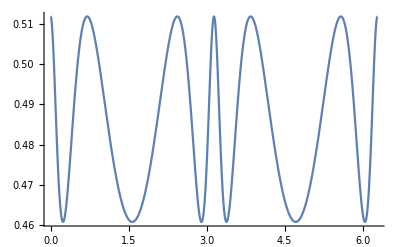

```mathematica
Plot[Total@mittenPedalLengths[1.5,t],{t,0,2π}]
```

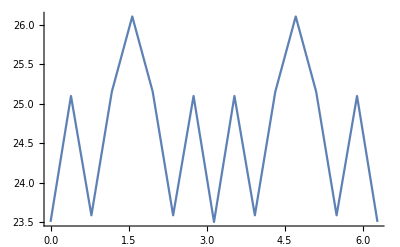

```mathematica
ListLinePlot@Module[{pl},
Table[{t,pl=mittenPedalLengths[1.5,t];(1/pl[[1]]+1/pl[[2]]+1/pl[[3]])},{t,0,2π,toRad[22.5]}]]
```

#### Sum of cos double angle of extriangle: cos(2A’)+cos(2B’)+cos(2C’) = -cos(A)-cos(B)-cos(C) = constant = 1 - r/R

```mathematica
Clear@excDoubleCos;excDoubleCos[a_,t_]:=Module[{orbit,normals,exc},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
{Total[getTriCosines@orbit],getTriDoubleCosineSum@exc}
];
```

```mathematica
Table[excDoubleCos[3,t],{t,0,2π,toRad[1]}]//Mean
```

{1.1075,-1.1075}

```mathematica
Table[excDoubleCos[1.5,t],{t,0,2π,toRad[1]}]//StandardDeviation//Chop
```

{0,0}

(a/a')^2 + (b/b')^2 + (c/c')^2 =(3 - Cos[A] - Cos[B] - Cos[C])/2 = 1-r/(2R) = constant!

```mathematica
Clear@triRatioSums;triRatioSums[a_,t_]:=Module[{orbit,normals,exc,p12,p23,p31,e12,e23,e31,notables,r,R,const},
{orbit,normals}=orbitNormals[a,t];
exc=getExcenters[orbit,normals];
{p12,p23,p31}=triLengths[orbit];
{e12,e23,e31}=triLengths[exc];
notables=getNotables[orbit,normals];
r="incRadius"/.notables;
R="cirRadius"/.notables;
const=(2-r/R)/2;
{(p12/e23)^2+(p23/e31)^2+(p31/e12)^2,const}
];
```

```mathematica
Table[triRatioSums[1.5,t],{t,0,2π,2π/360}]//Mean
```

{0.81867,0.81867}

```mathematica
Table[triRatioSums[1.5,t],{t,0,2π,2π/360}]//StandardDeviation//Chop
```

{0,0}

## Circumbilliard (Old)

```mathematica
getRho[a_]:=Module[{z,num,denom},
z=Sqrt[a^4-a^2+1];
num=2(z-1);
denom=(a^2-1)(a^2+z);
num/denom];
```

```mathematica
Limit[getRho[a],a->1]
```

1/2

```mathematica
getRho[1.5]
```

0.36266

#### Find the axis ratio which can be placed around a triangle with given ρ = r/R ratio

```mathematica
rhoSols[ρ_]=FullSimplify[a/.Solve[getRho[a]==ρ,a],ρ>0]
```

{-√((2+ρ^2-2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ))),√((2+ρ^2-2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ))),-√((2+ρ^2+2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ))),√((2+ρ^2+2 √(1-2 ρ) (1+ρ))/(ρ (4+ρ)))}

```mathematica
rhoD1[a_]=FullSimplify[D[getRho[a],a],a>0]
```

(2 a (-5-5 a^4+4 √(1-a^2+a^4)+a^2 (2+4 √(1-a^2+a^4))))/((-1+a^2)^3 √(1-a^2+a^4))

```mathematica
rhoD2[a_]=FullSimplify[D[D[getRho[a],a],a],a>0]
```

-(2 (-5+4 √(1-a^2+a^4)+a^2 (-19-15 a^8+28 √(1-a^2+a^4)+4 a^2 (3-4 √(1-a^2+a^4))+a^6 (5+12 √(1-a^2+a^4))+a^4 (-26+20 √(1-a^2+a^4)))))/((-1+a^2)^4 (1-a^2+a^4)^(3/2))

```mathematica
rhoD2[.5]
```

0.54851

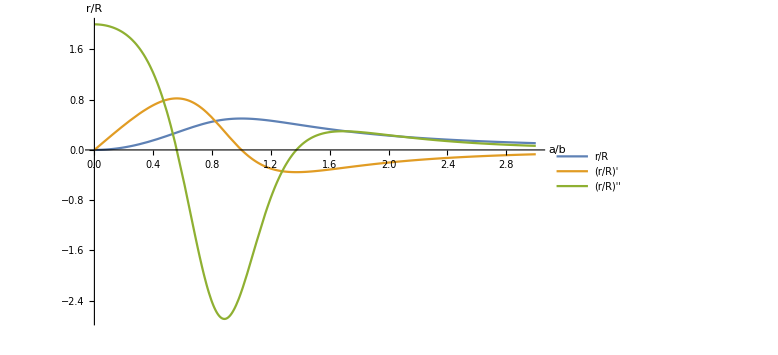

```mathematica
Plot[{getRho[a],rhoD1[a],rhoD2[a]},{a,0,3},PlotLegends->(Style[#,20]&/@{"r/R","(r/R)'","(r/R)''"}),
AxesStyle->20,PlotRange->All,AxesLabel->{"a/b","r/R"},ImageSize->Large]
```

```mathematica
a/.FindRoot[rhoD1[a],{a,1.1}]
```

1.

```mathematica
a/.FindRoot[rhoD2[a],{a,#}]&/@{.5,1.5}
```

{0.559964,1.37285}

```mathematica
FindRoot[rhoD2[a],{a,.5}]
```

{a→0.559964}

```mathematica
rhoSols[1/3.]
```

{-0.629016,0.629016,-1.58978,1.58978}

```mathematica
rhoSols[ρ][[4]]//TeXForm
```

\sqrt{\frac{\rho ^2+2 \sqrt{1-2 \rho } (\rho +1)+2}{\rho  (\rho +4)}}

TODO: Solution : get the axis ratio. get the mittenpunk. draw ellipse with center on mittenpunkt, passing thru all vertices. but how to rotate it? over constrained?

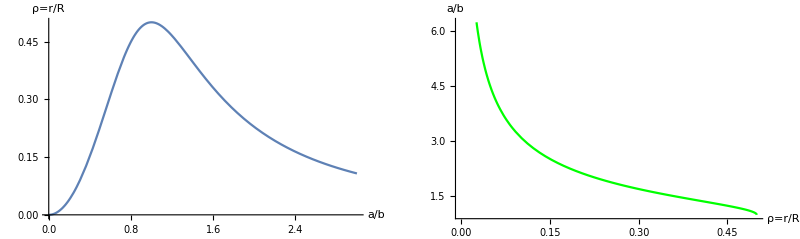

```mathematica
Module[{pA,pR},
pA=Plot[getRho[a],{a,0,3},AxesLabel->{"a/b","ρ=r/R"},AxesStyle->16];
pR=Plot[{rhoSols[ρ][[4]]},{ρ,0,.5},AxesLabel->{"ρ=r/R","a/b"},AxesStyle->16,PlotStyle->{Red,Green}];
GraphicsRow[{pA,pR},ImageSize->800]]
```

### Draw It

```mathematica
Clear@drawCB;
drawCB[a_,{x0_,y0_},theta_,x_,opts:OptionsPattern[]]:=Module[{ellPlot,orbitData,orbit,normals,comb,origin,lgt=.5},
ellPlot=plotEll[a];
orbitData=getOrbitData[N[a],N[x], FilterRules[{opts}, Options[getOrbitData]]];(* N for speed *)
(* half-angle to display α at bisector *)
orbit="orbit"/.orbitData;
normals="normals"/.orbitData;
origin=Graphics@{PointSize@Large,Blue,Point@{0,0},Rotate[Text[Style["M",20],{0,0},{-1.5,-1}],-theta],Dashed,Line[{{-a,0},{a,0}}],Line[{{0,-1},{0,1}}]};
comb=Show[{ellPlot,drawOrbit[orbitData,lgt,False,20],origin}];
Show[Graphics@Translate[Rotate[comb[[1]],theta],{x0,y0}],
ImageSize->Medium,
AspectRatio->Automatic,
Axes->True,
PlotRange->{{-2,3},{-1,2}},Frame->True,AxesStyle->Directive[RGBColor[.66,.66,.66]],
PlotLabel->Style["a="<>nf@a<>"; x="<>nf@x,20]]];
```

```mathematica
drawCB[1.5,{1,.5},toRad[30.],.3]
```

-Graphics-

-Graphics-

```mathematica
Clear@circumSystem;(*solve for b,t*)
circumSystem[P1_,P2_,A_]:=Module[{ct,st,P1p,P2p,eqn1,eqn2},
st=Sin@t;ct=Cos@t;
P1p=rot[P1,-st,ct];
P2p=rot[P2,-st,ct];
eqn1=P1p[[1]]^2+(A P1p[[2]])^2==(A b)^2;
eqn2=P2p[[1]]^2+(A P2p[[2]])^2==(A b)^2;
(* eqn3=FullSimplify[P2p[[1]]^2+(A P2p[[2]])^2-(A b)^2==0,A>0&&b>0]; *)
{eqn1,eqn2}];circumSystem[{x1,y1},{x2,y2},A](*//FullSimplify[#,A>1&&b∈Reals]&*)
```

{A^2 (y1 Cos[t]-x1 Sin[t])^2+(x1 Cos[t]+y1 Sin[t])^2==A^2 b^2,A^2 (y2 Cos[t]-x2 Sin[t])^2+(x2 Cos[t]+y2 Sin[t])^2==A^2 b^2}

```mathematica
Clear@solveCircum;
solveCircum[orbit_]:=Module[{sides,mit,cos123,rhoCos,A,sols0,sols,ts,bs,as,circSys},
sides=triLengths@orbit;
mit=getMittenTrilin[orbit,RotateLeft@sides];
cos123=getTriCosines[orbit];
rhoCos=Total@cos123-1;(*r/R=cosA+cosB+cosC-1*)
(*Print["rhoCos: " ,rhoCos,", r/R: " ,getInradius[sides]/getCircumradius[sides]];*)
A=rhoSols[rhoCos][[4]];
circSys=circumSystem[orbit[[1]]-mit,orbit[[2]]-mit,A];
sols0=NSolve[circSys,{t,b}]//Quiet;
sols=Select[{t,b}/.sols0,(First[#]∈Reals&&Second[#]∈Reals)&];
ts=(#[[1]]&/@sols);
bs=(#[[2]]&/@sols);
as=A*bs;
(* keep only those sols which pass through P3 *)
Module[{P3ps,P3ok,errors},
P3ps=rot[orbit[[3]]-mit,-Sin@#,Cos@#]&/@ts;
errors=MapThread[ellError[#1,#2,#3]&,{as,bs,P3ps}];
(*Print["errors: ",errors];*)
P3ok=(Abs[#]<10^-6)&/@errors;
sols=Pick[sols,P3ok];
ts=Pick[ts,P3ok];
as=Pick[as,P3ok];
bs=Pick[bs,P3ok];
];
{
"rhoCos"->rhoCos,
"A"->A,
"mit"->mit,
"sols"->sols,
"ts"->ts,
"as"->A*bs,
"bs"->bs
}];
```

```mathematica
tbSols=solveCircum[{{0,0},{1.,0},{.5,Sqrt[3]/1.25}}]
```

{rhoCos→0.448429,A→1.25291,mit→{0.5,0.551208},sols→{{-1.5708,-0.665994},{1.5708,-0.665994},{-1.5708,0.665994},{1.5708,0.665994}},ts→{-1.5708,1.5708,-1.5708,1.5708},as→{-0.834433,-0.834433,0.834433,0.834433},bs→{-0.665994,-0.665994,0.665994,0.665994}}

```mathematica
Clear@transfGr;
transfGr[gr_,scale_,theta_,trans_]:=Graphics@Translate[Rotate[Scale[gr[[1]],scale],theta],trans];
```

```mathematica
Clear@drawSolCB;drawSolCB[tri_,showCtrs_:False]:=Module[{cbs,t,a,b,x0,y0,ell,rotEll,gr,inc,cir,mit,axes,rotAxes},
cbs=solveCircum[tri];
{x0,y0}="mit"/.cbs;
a=First["as"/.cbs];
b=First["bs"/.cbs];
t=First["ts"/.cbs];
ell=plotEll[1];
mit="mit"/.cbs;
rotEll=transfGr[ell,{a,b},t,mit];
(*rotEll=MapThread[transfGr[ell,{#1,#2},#3,mit]&,{"as"/.cbs,"bs"/.cbs,"ts"/.cbs}];*)
axes=Graphics@{Red,Dashed,Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]};
rotAxes=transfGr[axes,{a,b},t,mit];
inc="inc"/.cbs;
cir="cir"/.cbs;
gr=Graphics[{
PointSize@Large,FaceForm@None,
{Red,Point@mit,Text[Style["M",16],mit,{-1.5,-1.5}]},
{Black,Point@tri,EdgeForm@Black,Polygon@tri},
If[showCtrs,{{Darker@Green,Dashed,Circle[inc,"inradius"/.cbs],Point@inc},
{Blue,Dashed,Circle[cir,"circumradius"/.cbs],Point@cir}},{}]
}];
Show[{rotEll,rotAxes,gr},
Axes->True,Frame->True,AspectRatio->Automatic,PlotRange->{{-3,3},{-3,3}}]];
```

```mathematica
drawSolCB[{{.1,.2},{1.1,.3},{1.5,2.3}}]
```

-Graphics-

```mathematica
Manipulate[drawSolCB[{P1,P2,P3}],
{{P1,{2.,0}},Locator},
{{P2,{-1,2}},Locator},
{{P3,{1,-2}},Locator}
]
```

#### Circumbilhar Ronaldo

```mathematica
circRon[a_,b_,x_,y_]=-b^2*(a+Sqrt[a^2+b^2])x^2+b(a^2+a*Sqrt[(a-1)^2+b^2]+a*Sqrt[a^2+b^2]-b^2+Sqrt[(a-1)^2+b^2]Sqrt[a^2+b^2]-a-Sqrt[a^2+b^2])*x*y+(-a^2*Sqrt[(a-1)^2+b^2]+b^2*a-a*Sqrt[(a-1)^2+b^2]*Sqrt[a^2+b^2]-b^2)*y^2+b^2(a+Sqrt[a^2+b^2])*x+b^3*y;
```

```mathematica
Collect[circRon[a,b,x,y],{x,y}]
```

-b^2 (a+√(a^2+b^2)) x^2+b^3 y+(-b^2+a b^2-a^2 √((-1+a)^2+b^2)-a √((-1+a)^2+b^2) √(a^2+b^2)) y^2+x (b^2 (a+√(a^2+b^2))+b (-a+a^2-b^2+a √((-1+a)^2+b^2)-√(a^2+b^2)+a √(a^2+b^2)+√((-1+a)^2+b^2) √(a^2+b^2)) y)

## Diagram of (u,v) arm constant r/R

#### Plot Simple Triangle Arm For Constant r/R

```mathematica
armrOvR[u_,v_]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Total[getTriCosines@tri]-1];
```

```mathematica
showArm[u_,v_]:=Module[{tri},
tri={{0,0},{1,0},{u,v}};
Graphics[{PointSize@Large,Thickness@Large,FaceForm@None,EdgeForm@Red,Polygon@tri,Blue,Point@tri}]]
```

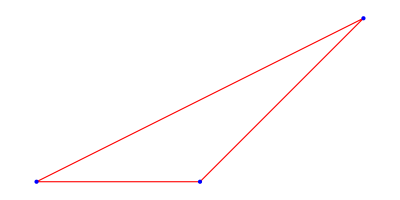

```mathematica
showArm[2,1]
```

```mathematica
Maximize[(1+v)/Sqrt[1+v^2]-1,v]
```

{-1+√2,{v→1}}

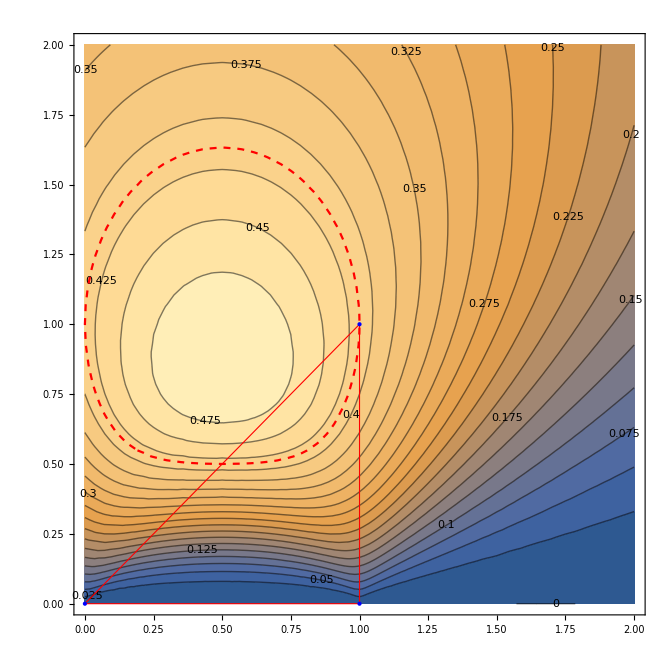

```mathematica
Module[{cc,ccObt},
cc=ContourPlot[armrOvR[u,v],{u,0,2},{v,0,2},ContourLabels->True,Contours->Table[x,{x,0,5,.025}],
Epilog->{Sequence@@showArm[1,1]}];
ccObt=ContourPlot[armrOvR[u,v]==Sqrt[2]-1,{u,0,2},{v,0,2},ContourLabels->True,Contours->{Sqrt[2]-1.},ContourStyle->{Dashed,Red}];
Show[{cc,ccObt}]]
```

#### At which a/b will the orthic become obtuse?

Before we must ask, at which triangle height (say the base is = 1) does its orthic become obtuse?

```mathematica
baseCosOrt[d_]:=Module[{tri,ort,ortH,ortD,eqn,cosHalf},
tri={{-1/2,0},{1/2,0},{0,d}};
ort=getAltBases@@tri;
ortD=Sqrt[ort[[1]].ort[[1]]];
ortH=ort[[1,2]];
cosHalf=ortH/ortD;
cosDoubleAngle[cosHalf]
]
```

```mathematica
baseCosOrt[d]
```

-1.+d^2/(2 (1/4+d^2)^2 (d^2/(4 (1/4+d^2)^2)+(1/2-1/(4 (1/4+d^2)))^2))

## Study of Orthic

#### Desenha órtico

```mathematica
Clear@drawOrthic;
drawOrthic[u_,v_,op_,clrs_:{Blue,Red,Darker@Green}]:=Module[{tri,gr,xmax=2,ymax=1.5,sides,orthic,sidesOrt,excOrt,ort,tris},
tri={{-.5,0},{.5,0},{u,v}};
sides=RotateLeft@triLengths[tri];
ort=getOrthocenterTrilin[tri,sides];
orthic=orthicTriangle[tri,sides];
sidesOrt=RotateLeft@triLengths[orthic];
excOrt=excentralTriangle[orthic,sidesOrt];
tris={tri,orthic,excOrt};
gr=Graphics[{
MapThread[{
{Opacity@.15,FaceForm@#2,EdgeForm@#2,Thick,Polygon@#1},
{PointSize@Medium,#2,Point@#1}
}&,Reverse/@{tris,clrs}],
{Blue,PointSize@Large,Point@ort,Text[Style["H",16],ort,{-3,0}]}}];
Legended[Show[{gr,op},
ImageSize->Medium,Frame->False,FrameStyle->Medium,
PlotRange->{{-xmax,xmax},{-ymax,ymax}},AspectRatio->Automatic],LineLegend[Directive[Thick,#]&/@clrs,
Style[#,16]&/@{"reference","orthic","orthic's excentral"}]]];
```

```mathematica
Clear@ortPath;ortPath[xmin_,xmax_,y_,ps_:{Dotted,Orange}]:=Module[{tri,sides,ort},
ParametricPlot[
tri={{-.5,0},{.5,0},{x,y}};
sides=RotateLeft@triLengths[tri];
ort=getOrthocenterTrilin[tri,sides],
{x,xmin,xmax},PlotStyle->ps]
];
```

```mathematica
Module[{op},
op=ortPath[-1.5,1.5,1.2];
Manipulate[
drawOrthic[x,1.2,If[drOrtPath,op,{}]],
{{x,.1},-2,2},
{{drOrtPath,True},{True,False}}]]
```

### When is it obtuse

#### Um triangulo isoceles ABC, | AB | = 1, height = d, produz um ortico obtuso se (1) d < (Sqrt[2] - 1)/2 = .207 ou se (2) d > (Sqrt[2] + 1)/2 = 1.207 Ou seja, o cosseno da base do órtico é positivo

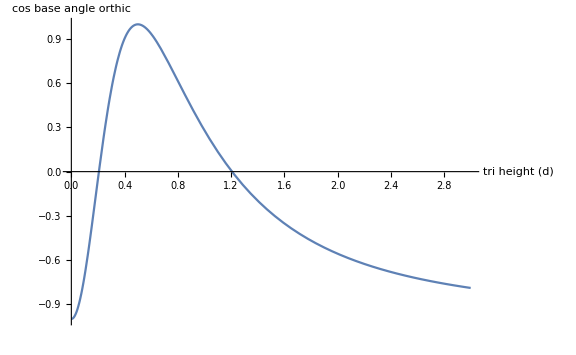

```mathematica
Plot[baseCosOrt[d],{d,0,3},AxesLabel->{"tri height (d)","cos base angle orthic"},AxesStyle->Medium,ImageSize->Large]
```

```mathematica
calcOrt[d_]:=Module[{tri,ort,ortW,eqn},
tri={{-1/2,0},{1/2,0},{0,d}};
ort=getAltBases@@tri;
ortW=2ort[[1,1]];
eqn=ortW^2==2ort[[1]].ort[[1]];
Select[d/.Solve[eqn,d],#>0&]
]
```

```mathematica
ortOpts=calcOrt[d]
```

{1/2 (-1+√2),1/2 (1+√2)}

```mathematica
ortOpts//N
```

{0.207107,1.20711}

```mathematica
Clear@showOrt;showOrt[d1_,d2_]:=Module[{tris,orts,gr},
tris={{-1/2,0},{1/2,0},{0,#}}&/@ortOpts;
orts=getAltBases@@#&/@tris;
orts[[2]]=(#+{0,0.0})&/@orts[[2]];(* perturb just to see *)
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm@Blue,Polygon/@tris,Blue,Point/@tris},
{EdgeForm@Red,Polygon/@orts,Red,Point/@orts}
}];
Show[gr,AspectRatio->Automatic,Frame->True,ImageSize->Small]
];
```

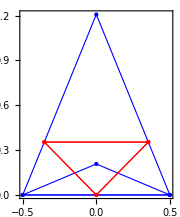

```mathematica
showOrt@@ortOpts
```

Do paper: (basic orbits)

-Graphics-

#### 1) When orbit is horizontal :

```mathematica
orbitW[a_]:=Sqrt[2 deltaA[a]-a^2+1]/(a^2-1);
```

```mathematica
orbitHeightHoriz[a_]:=a^3/(deltaA[a]+1);
(* a>1 *)
orbitBaseHoriz[a_]:=orbitW[a];
```

```mathematica
horizD[a_]=FullSimplify[orbitHeightHoriz[a]/orbitBaseHoriz[a],a>1]
```

(a^3 (-1+a^2))/((1+√(1-a^2+a^4)) √(1-a^2+2 √(1-a^2+a^4)))

```mathematica
posReal[x_]:=If[negl[Im[x]],(Re[x]>0),False];
```

```mathematica
(a/.Solve[horizD[a]==ortOpts[[1]],a])^2
```

{Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,2}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,3}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,4}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,5}],Root[{-2+#1^2&,-51+36 #1-110 #2+72 #1 #2+117 #2^2-76 #1 #2^2-144 #2^3+96 #1 #2^3+40 #2^4-16 #1 #2^4-32 #2^5+16 #2^6&},{2,6}]}

```mathematica
posReal/@N@(a/.Solve[horizD[a]==ortOpts[[1]],a])
```

{True,False,False,False,False}

```mathematica
(a/.Solve[horizD[a]==ortOpts[[2]],a])^2
```

{Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,2}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,3}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,4}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,5}],Root[{-2+#1^2&,-51-36 #1-110 #2-72 #1 #2+117 #2^2+76 #1 #2^2-144 #2^3-96 #1 #2^3+40 #2^4+16 #1 #2^4-32 #2^5+16 #2^6&},{2,6}]}

```mathematica
posReal/@N@(a/.Solve[horizD[a]==ortOpts[[2]],a])
```

{True,False,False,False,False}

```mathematica
{#,First@Select[N[a/.Solve[horizD[a]==#,a]],posReal]}&/@ortOpts//Prepend[#,{"critical d","a/b"}]&//Grid[#,Frame->All]&
```

critical d | a/b
1/2 (-1+√2) | 1.18565
1/2 (1+√2) | 1.61645

#### Plot Orthic' s Orthocenter, and Orthic' s orthic' s Incenter.

```mathematica
nfn[1.2,3]
```

1.200

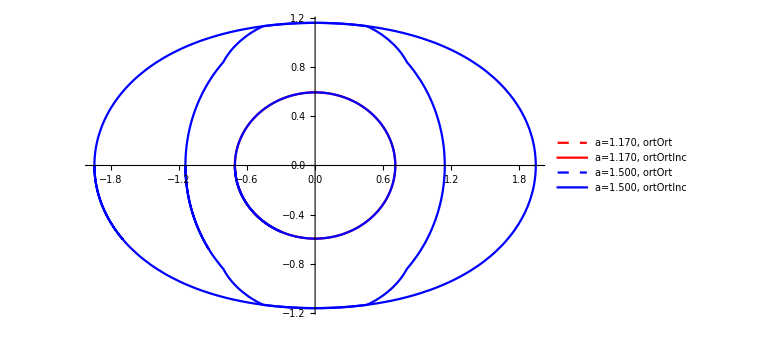

```mathematica
Module[{as={1.17,1.5},clrs={Red,Blue}},
Legended[
Show[MapThread[orthicsOrthicIncenterLocus[#1,π/1.2,π/1.2,#2]&,{as,clrs}]//Quiet,
ImageSize->Large,PlotRange->All],
LineLegend[Directive[{Thickness@Large,#}]&/@(Sequence@@{{Dashed,#},#}&/@clrs),
Flatten[{"a="<>nfn[#,3]<>", ortOrt","a="<>nfn[#,3]<>", ortOrtInc"}&/@as]]]]
```

```mathematica
(* FAZER VIDEO variando a *)
```

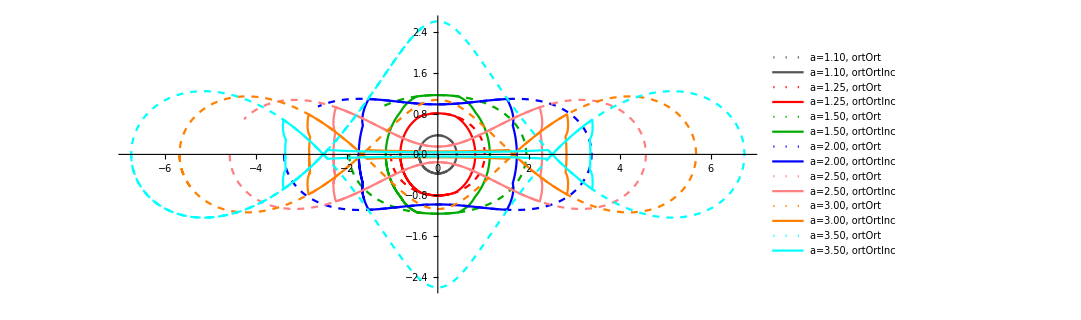

```mathematica
Module[{as={1.1,1.25,1.50,2.00,2.50,3,3.5},clrs={Darker@Gray,Red,Darker@Green,Blue,Pink,Orange,Cyan}},
Legended[
Show[MapThread[orthicsOrthicIncenterLocus[#1,π/1.1,π/1.9*Sqrt[#1],{Dashed,#2},#2]&,{as,clrs}]//Quiet,
ImageSize->800,PlotRange->All],
LineLegend[Directive[{Thickness@Large,#}]&/@(Sequence@@{{Dotted,#},#}&/@clrs),
Flatten[{"a="<>nf[#]<>", ortOrt","a="<>nf[#]<>", ortOrtInc"}&/@as]]]]
```

```mathematica
getOneOrthicOrtIncFrame[a_]:=Module[{styles={Darker@Gray,Orange,Green,Blue,Red},xmax=6.5,ymax=2.5},
Legended[Show[Quiet@{
plotEll[a,styles[[1]]],
orthocenterLocus[a,π,styles[[2]]],
orthicIncenterLocus[a,π,styles[[3]]],
orthicsOrthicIncenterLocus[a,π/1.1,2π,styles[[4]],styles[[5]]]
},
PlotLabel->Style["a/b = "<>nfn[a,2],16],
AspectRatio->Automatic,
AxesStyle->16,
ImageSize->800,
PlotRange->{{-xmax,xmax},{-ymax,ymax}}],
LineLegend[Directive/@styles,
{"billiard","orbit orthocenter","orthic incenter","orthic orthocenter","orthic orthic's incenter"}]]];
```

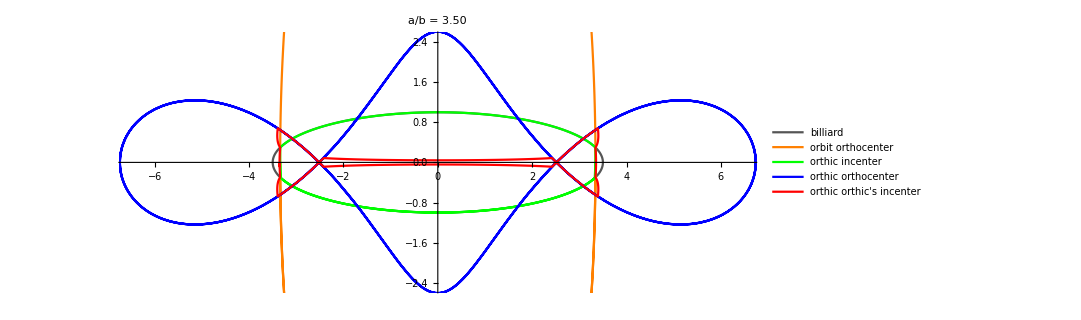

```mathematica
getOneOrthicOrtIncFrame[3.5]
```

#### 2) When orbit is vertical (no real solutions!)

```mathematica
orbitHeightVert[a_]:=1+1/(a^2+deltaA[a]);
orbitBaseVert[a_]:=2*a^2orbitW[a];
```

```mathematica
horizW[a_]=FullSimplify[orbitHeightVert[a]/orbitBaseVert[a],a>1]
```

((-1+a^2) (1+1/(a^2+√(1-a^2+a^4))))/(2 a^2 √(1-a^2+2 √(1-a^2+a^4)))

```mathematica
Select[N[a/.Solve[horizW[a]==#,a]],posReal]&/@ortOpts
```

{{1.45643+1.31564×10^-17 ⅈ,1.99296+9.61452×10^-18 ⅈ},{}}

## Epitrochoid

```mathematica
Clear@epitrochoid;
epitrochoid[r_,d_,th_]:=Module[{arg},
arg=th(1/r+1);
{(1+r)Cos[th]-d Cos[arg],(1+r)Sin[th]-d Sin[arg]}]
```

#### What (1, b) ellipse produces an ellipse whose eccentricity is the same as (1.5, 1)

```mathematica
Solve[eccentricity[1.5,1]==eccentricity[1,b],b]
```

{{b→-0.666667},{b→0.666667}}

```mathematica
eccentricity[1.5,1]
```

0.745356

```mathematica
1./(2/3)
```

1.5

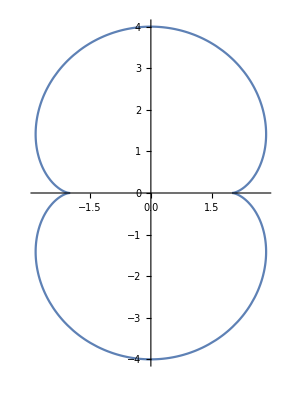

```mathematica
Manipulate[
ParametricPlot[epitrochoid[r,r*d,th],{th,0,ThMult*2π},PlotStyle->{Thick,Red},PerformanceGoal->"Quality",Frame->True],
{{r,.25},.01,3,.01,Appearance->"Labeled"},
{{d,2.5},0,5,Appearance->"Labeled"},
{{ThMult,2},1,10,1,Appearance->"Labeled"}]
```

## Is Mitten preserved via affine?

```mathematica
Clear@affineMtx;affineMtx[dx_,dy_,sx_,sy_,th_]:=Module[{sth,cth,rotMtx,scaleMtx,displMtx},
sth=Sin@th;
cth=Cos@th;
rotMtx={{cth,-sth,0},{sth,cth,0},{0,0,1}};
scaleMtx={{sx,0,0},{0,sy,0},{0,0,1}};
displMtx={{1,0,dx},{0,1,dy},{0,0,1}};
displMtx.(scaleMtx.rotMtx)]
```

```mathematica
homogProd[mtx_,p_]:=Most[mtx.Append[p,1]];
```

```mathematica
homogProd[affineMtx[0,0,1,1,0],{1,0}]
```

{1,0}

```mathematica
Clear@tryAff;tryAff[dx_,dy_,sx_,sy_,th_,tri_:{{0,0},{2,0},{.5,Sqrt[3]/2}}]:=Module[{normals,notables,sides,aff,triAff,sidesAff,normalsAff,notablesAff,notablesThruAff,notableNames,
meds,medsAff,medsThruAff},
meds=getMedians@@tri;
sides=RotateLeft@triLengths[tri];(*{L,1+L^2+2L Cos[th],1};*)
normals=getTriBisectors@@tri;
notables=getNotables[tri,normals];
aff=affineMtx[dx,dy,sx,sy,th];
triAff=homogProd[aff,#]&/@tri;
medsAff=homogProd[aff,#]&/@meds;
sidesAff=RotateLeft@triLengths[triAff];
normalsAff=getTriBisectors@@triAff;
notablesAff=getNotables[triAff,normalsAff];
notableNames={"inc","bar","ort","cir","npc","feu","ex12","ex23","ex31","sym","mit","ger","nag","spi","antifeu","x88"};
(*notableNames={"inc","bar","ort","cir","npc","mit","feu","ex12","ex23","ex31"};*)
notablesThruAff=(#->homogProd[aff,#/.notables])&/@notableNames;
medsThruAff=homogProd[aff,#]&/@meds;
{"tri"->tri,
"sides"->sides,
"mitt"->"mit"/.notables,
"affine"->MatrixForm[aff],
"triAff"->triAff,
"sidesAff"->sidesAff,
"mittAff"->"mit"/.notablesAff,
"mitt0ThruAff"->"mit"/.notablesThruAff,
"notables"->notables,
"notablesAff"->notablesAff,
"notablesThruAff"->notablesThruAff,
"meds"->meds,
"medsAff"->medsAff,
 "medsThruAff"->medsThruAff
}
];
```

```mathematica
Module[{aff,gr,nots,notsAff,notsThru,dr,circ,rad=.035,clrs={"ref"->Blue,"aff"->Darker@Green,"thru"->Red}},
Manipulate[
aff=tryAff[dx,dy,sx,sy,th,{{0,0},{1,0},{p3x,p3y}}];
gr=Graphics[{FaceForm@None,PointSize@Medium,
{EdgeForm["ref"/.clrs],Polygon["tri"/.aff],"ref"/.clrs,Point["meds"/.aff]},
{EdgeForm["aff"/.clrs],Polygon["triAff"/.aff],"aff"/.clrs,Point["medsAff"/.aff]}}];
{dr,circ}=If[basic,
{drawBasicNotablesSingleClr[#1,#3,#2]&,circBasicNotablesSingleClr[#1,rad,#3,#2]&},
{drawNotablesSingleClr[#1,#3,#2]&,circNotablesSingleClr[#1,rad,#3,#2]&}];
nots=dr["notables"/.aff,"","ref"/.clrs];
notsAff=dr["notablesAff"/.aff,"","aff"/.clrs];
notsThru=circ["notablesThruAff"/.aff,"","thru"/.clrs];
nots=dr["notables"/.aff,"","ref"/.clrs];
notsAff=dr["notablesAff"/.aff,"","aff"/.clrs];
notsThru=circ["notablesThruAff"/.aff,"","thru"/.clrs];
Show[{gr,nots,notsAff,notsThru},PlotRange->{{-xmax*.25,xmax},{-xmax*.25,xmax}},ImageSize->Large],
{{xmax,3},{1,1.5,2,3,4}},
{{dx,0},-3,3},
{{dy,0},-3,3},
{{th,π/4},-π,π},
{{sx,1.5},-2,2},
{{sy,2},-2,2},
{{p3x,1.5},-3,3},
{{p3y,1},-3,3},
{{basic,True},{True,False}}]]
```

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {tryAff[0, 0, 1.5, 2, π/4, {{0, 0}, {1, 0}, {1.5, 1}}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {clrs$1539512} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

## Make Movies I

```mathematica
Clear@doMovieFrames;
Options@doMovieFrames=Join[Options@movieFrame,{step->toRad@1.}];
doMovieFrames[a_,exp_,lociFn_,view_:"excHalf",opts:OptionsPattern[]]:=Module[{loci,ellPlot,causticPlot,excenterLims,showables},
ellPlot=plotEllFill[1.5,Directive[Blue,Opacity@.1],{Thick,Black}];
causticPlot=plotEllb[Sequence@@getTriCausticParams[a],"feu"/.ptClrs];
(*loci=precompLoci[a];*)
loci=lociFn[a];
excenterLims=excenterMax[a];
showables=Join[getExpShowables[exp],{"loci","orbit"}];
(*Print["a=",a,",t=",0,",ellPlot=",ellPlot,",loci=",loci,",excL=",excenterLims,",view=",view,",opts=",FilterRules[{opts,showablesOpt->showables},Options@movieFrame]];*)
Table[movieFrame[a,t,ellPlot,causticPlot,loci,excenterLims,view,FilterRules[{opts,showablesOpt->showables},Options@movieFrame]],{t,0,2π,OptionValue@step}]];
```

```mathematica
Clear@makeMovie;
makeMovie[fname_,frames_,repeats_:3]:=Module[{framesConcat},
framesConcat=Flatten@ConstantArray[frames,repeats];
Print["Exporting "<>ToString@Length[framesConcat]<>" frames to "<>fname];
Export[fname,framesConcat,"VideoEncoding"->"MPEG-4 Video"];
];
```

### Ronaldo Hi-Quality Demo

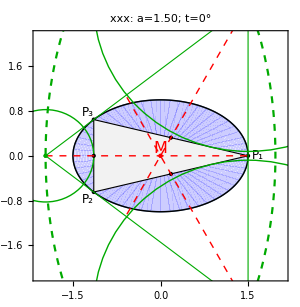

```mathematica
doMovieFrames[1.5,"mitten",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,"excHalf",labExtra->"xxx: ",step->toRad@120,ImageSize->300][[1]]
```

```mathematica
imgACTtop=doMovieFrames[1.5,"feuerall",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,"anticompl",step->toRad@120,ImageSize->600][[2]];
imgACTbot=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@120,ImageSize->600][[2]];
```

```mathematica
feuerbachImg=-Graphics-;
```

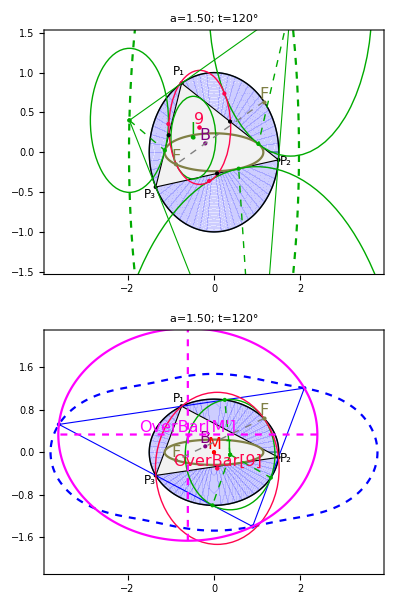

```mathematica
Grid[{{imgACTtop},{imgACTbot}}]
```

```mathematica
doImgsDarbouxPt=True;
If[doImgsDarbouxPt,Module[{imgs},
imgs=doMovieFrames[1.5,"darboux",Function[a,{}],"anticompl2",step->toRad@.5,ImageSize->1200];
makeMovie["darboux point v1.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 2884 frames to darboux point v1.mov

```mathematica
doImgsDerivedTris=True;
If[doImgsDerivedTris,Module[{a=1.5,imgs},
imgs=Table[Show[showDerivedTris[a,tDeg],ImageSize->800],{tDeg,0,359,.5}];
makeMovie["derived tris v3.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 2876 frames to derived tris v3.mov

```mathematica
doImgsAnticomplBoth=False;
If[doImgsAnticomplBoth,Module[{imgsTop,imgsBot,imgs},
imgsTop=doMovieFrames[1.5,"feuerall",excenterLocus[#,2π,{Dashed,"exc"/.ptClrs}]&,
"anticompl",step->toRad@.25,ImageSize->800];
imgsBot=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,
"anticompl",step->toRad@.25,ImageSize->800];
imgs=MapThread[Grid[{{#1},{#2}}]&,{imgsTop,imgsBot}];
makeMovie["anticompl triangle v3.mov",Join[imgs,Reverse@imgs],3]]];
```

Exporting 8646 frames to anticompl triangle v3.mov

```mathematica
doImgsAnticomplSimple=True;
If[doImgsAnticomplSimple,Module[{imgs},
imgs=doMovieFrames[1.5,"anticomplSimple",getAntiComplementaryVertexLocus,"anticompl2",step->toRad@1,ImageSize->800];
makeMovie["anticompl triangle circII.mov",Join[imgs,Reverse@imgs],2]]];
```

Exporting 1444 frames to anticompl triangle circII.mov

```mathematica
(* combo - "ell" *)
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"ell",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"feuerall"},
{getDashedFeuLoci},
{"Feuerbach+Extouch+Anti-Complement\n"}}];
makeMovie["ronaldo combo.mov",imgs,1]]];
```

Exporting 2881 frames to ronaldo combo.mov

```mathematica
(* mitten tall - "exc" *)
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"excHalf",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"mitten"},
{Function[a,{}]},
{"Mittenpunkt is Stationary\n"}}];
makeMovie["ronaldo mitten.mov",imgs,1]]];
```

Exporting 2881 frames to ronaldo mitten.mov

```mathematica
doImgsDemo=False;
If[doImgsDemo,Module[{imgs,fr,a=1.5,step0=toRad@.25},
imgs=Join@MapThread[(fr=doMovieFrames[a,#1,#2,"ort",step->step0,labExtra->#3,ImageSize->800];Join[Most@fr,Reverse@fr])&,
{{"antifeuer","caustic","feuerall"},
{Function[a,{}],getDashedFeuLoci,getDashedFeuLoci},
{"Anti-Complement of Feuerbach Point Sweeps Billiard\n",
"Feuerbach and ExtouchPoints Sweep Caustic\n",
"Feuerbach+Extouch+Anti-Complement\n"}}];
makeMovie["ronaldo combo feuer.mov",imgs,1]]];
```

Exporting 8643 frames to ronaldo combo feuer.mov

### Circumbilliard

```mathematica
doImgCircs=False;
If[doImgCircs,
Module[{imgs,ts},
ts=Table[{-2+4t/(2π),-2Cos[t]},{t,0,2π,toRad[1.]}];
imgs=drawSolCB[{{-1.5,2},{2,0},#}]&/@ts;
makeMovie["circumbilliard_hires3.mov",imgs]]];
```

### Study Maxima Locus of Orthocenter and Orthic Triangle

#### Orthic Incenter

#### Valor critico de "a" para o ortocentro encostar no bilhar por cima e por baixo (orbita = triangulo retangulo, cos (a) = 1/Sqrt[2]

```mathematica
doOrtInc=False;If[doOrtInc,ortIncFrames=doMovieFrames[1.5,"orthicinc",
Show[{
orthocenterLocus[#,π/1.2]//Quiet,
orthicIncenterLocus[#,π/1.2,{"inc"/.ptClrs}]
}]&,"ortHalf",toRad@1.]//Quiet;doOrtInc=False];
```

#### Whats the "a" such that the orthocenter locus y maximum is a: approx. 1.4854

```mathematica
cosAlphaX0[a_]=FullSimplify[cosAlpha[a,0],a>0]
```

(√(-1-a^2+2 √(1-a^2+a^4)))/(-1+a^2)

```mathematica
ortMaxA=Module[{theRay,eqn,ssol,interEll,eqn2},
theRay=ray[{0,1},{Sqrt[1-ca^2],-ca},s];
eqn=ellEqn[a,theRay[[1]],theRay[[2]]];
ssol=FullSimplify[(s/.Solve[eqn==0,s]),a>1&&ca≥0];
ssol=ssol[[2]];(* first is zero *)
(* eliminates s and ca *)
interEll=FullSimplify[(theRay/.s->ssol)/.ca->cosAlphaX0[a],a>1&&ca≥0];
Print@interEll;
Print["example: a=1.5, inter at: ",(interEll/.a->1.5)];
(* ERRO: tem q achar um a q gera o ortocentro correto at (0,a) *)
eqn2=FullSimplify[(a-interEll[[2]])/interEll[[1]]==(Sqrt[1-ca^2]/ca)/.ca->cosAlphaX0[a],a>1];
Solve[eqn2,{a}]];
```

{(a^2 √(3 a^2-a^6+2 a^4 (-2+√(1-a^2+a^4))+6 (-1+√(1-a^2+a^4))))/((-1+a^2) (-1+√(1-a^2+a^4))),-1/(a^2+√(1-a^2+a^4))}

example: a=1.5, inter at: {1.45692,-0.23795}

```mathematica
ortMaxA=a/.N@{a->Root[-1-#1^2-4 #1^3+#1^4+#1^6&,2]}
```

1.50997

#### Since the ortho locus is elliptic, what is its x max at ortMaxA? It’s exactly 1!!!

```mathematica
Module[{orbit,n,ort},
{orbit,n}=orbitNormals[ortMaxA,0];
Chop[getOrthocenter@@orbit]]
```

{-1.,0}

### Other Points : Mitten, Feuer, ExFeuer

#### Mittenpunkt Frames

```mathematica
doMitten=False;If[doMitten,mittenFrames=doMovieFrames[1.5,"mitten",precompLoci];doMitten=False];
```

#### Feuer and Extouch Frames (internal caustic)

```mathematica
doCaustic=False;If[doCaustic,causticFrames=doMovieFrames[1.5,"caustic",getFeuLoci];doCaustic=False];
```

```mathematica
Export["caustic30a.png",causticFrames[[31]]]
```

Part::partd: Part specification causticFrames ⟦ 31 ⟧ is longer than depth of object.

caustic30a.png

#### ExFeuerbach Locus

```mathematica
doExFeuer=False;If[doExFeuer,exFeuerFrames=doMovieFrames[1.5,"exfeuer",getFeuLoci[#,True]&,"ort"];doExFeuer=False];
```

```mathematica
exFeuerFrames[[31]]
```

Part::partd: Part specification exFeuerFrames ⟦ 31 ⟧ is longer than depth of object.

exFeuerFrames⟦31⟧

#### Anti-Feuerbach Locus

Exporting 444 frames to ronaldo all.mov

```mathematica
doAntiFeuer=False;If[doAntiFeuer,antiFeuerFrames=doMovieFrames[1.5,"antifeuer",getDashedFeuLoci,"ell"];doExFeuer=False];
```

```mathematica
(*Save["mitten.m",mittenFrames]*)
```

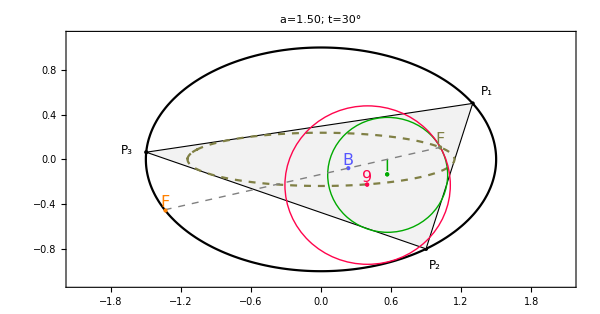

```mathematica
antiFeuerFrames[[31]]
```

```mathematica
doMitten=False;If[doMitten,makeMovie["mitten15.mov",mittenFrames];doMitten=False];
```

```mathematica
doCaustic=False;If[doCaustic,makeMovie["caustic15a.mov",causticFrames];doCaustic=False];
```

```mathematica
doExFeuer=False;If[doExFeuer,makeMovie["exfeuer15.mov",exFeuerFrames];doExFeuer=False];
```

Exporting 1083 frames to exfeuer15.mov

```mathematica
doAntiFeuer=False;If[doAntiFeuer,makeMovie["antifeuer15.mov",antiFeuerFrames];doExFeuer=False];
```

Exporting 1083 frames to antifeuer15.mov

```mathematica
doImgsConvexBarInc=False;
If[doImgsConvexBarInc,Module[{imgs},
imgs=Table[combineConvexBarInc[1.5,s],{s,0,1,.01}];makeMovie["convexBarInc.mov",Join[imgs,Reverse@imgs]]]];
```

```mathematica
(*Export["convexBarInc01.png",imgsConvexBarInc[[1]]];
Export["convexBarInc02.png",imgsConvexBarInc[[51]]];
Export["convexBarInc03.png",imgsConvexBarInc[[101]]];*)
```

```mathematica
doImgsConvexOrtCir=False;
If[doImgsConvexOrtCir,Module[{imgs},
imgs=Table[combineConvexOrtCir[1.5,s],{s,0,1,.01}];
makeMovie["convexOrtCir.mov",Join[imgs,Reverse@imgs]]]];
```

```mathematica
doImgsConvexExcFoot=False;
If[doImgsConvexExcFoot,Module[{imgs},
imgs=Table[Show[convExcTps[1.5,s],ImageSize->800],{s,0,1,.01}];makeMovie["convexExcFoot.mov",Join[imgs,Reverse@imgs]]
]];
```

Exporting 606 frames to convexExcFoot.mov

```mathematica
doImgsOrthicOrtIncFrames=False;
```

```mathematica
Clear@orthicOrtIncFrames
```

```mathematica
If[doImgsOrthicOrtIncFrames,
Module[{imgs},
imgs=Table[getOneOrthicOrtIncFrame[a],{a,1.1,3.5,0.01}];
makeMovie["orthicOrtIncFrames.mov",Join[imgs,Reverse@imgs]]]];
```

Exporting 1446 frames to orthicOrtIncFrames.mov

```mathematica
Directory[]
```

C:\Users\drezn\Dropbox\Mathematica

```mathematica
exportOrtOrtImgs=False;
If[exportOrtOrtImgs,
MapIndexed[Export["ortortinc-"<>ToString[First@#2]<>".png" ,getOneOrthicOrtIncFrame[#1]]&,
{1.01,1.25,1.5,2,2.25,2.5,3,3.5}]];
```

```mathematica
doImgsOrthicPreimages=False;
If[doImgsOrthicPreimages,
Module[{imgs,op},
op=Show[{ortPath[-1.5,1.5,1.2],Graphics[{Dotted,Blue,Line[{{-1.51,1.2},{1.51,1.2}}]}]}];
imgs=Table[Show[drawOrthic[x,1.2,op],ImageSize->800],{x,-1.351,1.351,.01}];
makeMovie["orthicPreimages.mov",Join[imgs,Reverse@imgs]]]];
```

Exporting 1626 frames to orthicPreimages.mov

#### Quadrangle

```mathematica
doImgsQuadrangle=False;
If[doImgsQuadrangle,
Module[{imgs,op},
imgs=Table[Show[showOneQuad[quadAlphaT,i,True,True],ImageSize->800],{i,Length["alphas"/.quadAlphaT]}];
makeMovie["quadrangle3.mov",imgs]]];
```

Exporting 1083 frames to quadrangle3.mov

## MakeMovies II

#### Generate Frames

```mathematica
Clear@oneImage;
oneImage[a_,t_,loci_,maxX_,maxY_]:=Show[drawSimT[a,t,loci],
PlotRange->{{-maxX,maxX},{-maxY,maxY}},
ImageSize->600];
```

```mathematica
Clear@imgsFixedA;
imgsFixedA[a_,clipExcenters_:False]:=Module[{loci,maxX,maxY,lims},
loci=precompLoci[a];
lims=excenterMax[a];
maxX=Round[lims[[1]]+.1,.1];
maxY=If[clipExcenters,Round[orthocenterMaxY[a,π/1.2]+.1,.1],
Round[lims[[2]]+.1,.1]];
Table[oneImage[a,t,loci,maxX,maxY],{t,0,2π,2π/360.}]];
Clear@imgsFixedT;
imgsFixedT[t_,aStart_,aEnd_,aStep_,clipExcenters_:False]:=Module[{loci,lims,maxX,maxY},
Table[
loci=precompLoci[a];
lims=excenterMax[a];
maxX=Round[lims[[1]]+.1,.1];
maxY=If[clipExcenters,Round[orthocenterMaxY[a,π/1.2]+.1,.1],
Round[lims[[2]]+.1,.1]];
oneImage[a,t,loci,maxX,maxY],
{a,aStart,aEnd,aStep}]];
```

```mathematica
Clear@makeAnimTransB;
makeAnimTransB[initB_,finalB_,stepB_]:=Module[{imgsInitB,imgsTransB,imgsFinalB},
imgsInitB=imgsFixedA[initB];
Print[Length[imgsInitB]];
imgsTransB=imgsFixedT[0,initB,finalB,stepB];
Print[Length[imgsTransB]];
imgsFinalB=imgsFixedA[finalB];Print[Length[imgsFinalB]];
Print["total frames = "<>ToString[Total[Length/@{imgsInitB,imgsTransB,imgsFinalB}]]];
{"initB"->imgsInitB,
"transB"->imgsTransB,
"finalB"->imgsFinalB
}
];
```

#### Generate Frames

```mathematica
doImgs=False;
```

```mathematica
If[doImgs,
(*imgs15=imgsFixedA[1.5];*)
imgs15clipped=imgsFixedA[1.5,True];
(*imgs20=imgsFixedA[2.0];*)
imgs20clipped=imgsFixedA[2.0,True];
]
```

```mathematica
Directory[]
```

C:\Users\drezn\Documents

#### Export Animated MOVs (install quicktime)

```mathematica
$PasswordFile
```

C:\ProgramData\Mathematica\Licensing\mathpass

## © 2019 Dan S. Reznik -- dan@upperwestsolucoes.com